```mathematica
SetOptions[EvaluationNotebook[],ShowGroupOpener->True]
```

## AFM Honeycomb lattice

### functions

```mathematica
FactorMatrix[(mat_)?MatrixQ]:=Module[{temp,cfactors,factors,commonfactor={}},temp=Flatten[Factor[mat]];
temp=Map[Replace[#1,0->Sequence[]]&,temp,{1}];
temp=Map[Replace[#1,HoldPattern[Times[a__]]->{a},{}]&,temp,{1}];cfactors=Map[#1/.{a_^n_->{a,n},a_->{a,1}}&,temp,{2}];
factors=(Intersection[##1,SameTest->(#1[[1]]===#2[[1]]&)]&)@@cfactors;
Do[Module[{pfactor,exp},pfactor=First[factors[[i]]];
exp=Last/@Cases[cfactors,{pfactor,_},{2}];
exp=If[First[exp]>0,Min[exp],Max[exp]];
commonfactor=Join[commonfactor,{pfactor^exp}];],{i,1,Length[factors]}];commonfactor=Times@@commonfactor;
HoldForm@@{commonfactor}*MatrixForm[Map[Cancel[#1/commonfactor]&,mat,{2}]]]

adj[m_]:=Map[Reverse,Minors[Transpose[m],Length[m]-1],{0,1}]*Table[(-1)^(i+j),{i,Length[m]},{j,Length[m]}]

MyAdj[expr_?SquareMatrixQ]:=Block[
	{l,drop,cofactors,minors},
	l = Length[expr];
	drop[mat_,row_,col_]:=Block[
		{rows,cols,slice}, 
		slice = Table[i,{i,1,l}];
		rows = Drop[slice,{row}];
		cols=Drop[slice,{col}];
		mat[[rows,cols]]];
	cofactors = Table[(-1)^(i+j),{i,Length[expr]},{j,Length[expr]}];
	minors = Table[Simplify@Det[drop[expr,i,j]],{i,l},{j,l}];
	Transpose[cofactors *minors]
]
MyInv[expr_?SquareMatrixQ]:=MyAdj[expr]/Simplify[Det[expr]]//Simplify
mysubst2={ϵR->ϵ(1+(ⅈ π α)/2),ϵA->ϵ((1-(ⅈ π α)/2)),ΔR->Δ(1-(ⅈ π α)/2),ΔA->Δ((1+(ⅈ π α)/2))}; (*haven't checked wether the + and - are in the correct places*)


IntegrateOverAngles[expr_]:=2π( (TrigToExp[expr])//TrigExpand)/.{Power[E,Times[Complex[0,n_],\[Phi]]]->0};
SetAttributes[IntegrateOverAngles,Listable]

MyResidue[expr_,{var0_,var1_}]:=Module[{func},
	func[myexpr_]:=Limit[(var0-var1)myexpr,var0->var1];
	SetAttributes[func,Listable];
	func[expr]
]

MyIntegrate[expr_]:=Block[{res,q1,q2,q1c,q2c},
	q1=-ΔR^2+ϵR^2;  	
	q1c = q1/.{ΔR->ΔA,ϵR->ϵA};
	res[x_,x0_]:=Residue[x,{q,x0}];
	1/2 1/(2π)^2 expr//IntegrateOverAngles//Simplify[#,{nx^2+nz^2==1}]&//ReplaceAll[#,p^n_->q^(n/2)]&// 2π ⅈ (res[#,q1]-res[#,q2])&//ReplaceAll[#,mysubst2]&//GetOrder[#,{α,-1}]&//Simplify[#,Assumptions->nx^2+nz^2==1]&
]
SetAttributes[MyIntegrate,Listable]

MyIntegrateλ[expr_]:=Block[{res, q1,q2,q1c,q2c},
	q1=-ΔR^2-2 ΔR λ nz+ϵR^2+2 λ ϵR;  
	q2=-ΔR^2+2 ΔR λ nz+ϵR^2-2 λ ϵR;

	q1c = q1/.{ΔR->ΔA,ϵR->ϵA};
	q2c = q2/.{ΔR->ΔA,ϵR->ϵA};
	res[x_,x0_]:=MyResidue[x,{q,x0}];
	1/2 1/(2π)^2 expr//IntegrateOverAngles//ReplaceAll[#,p^n_->q^(n/2)]&//ⅈ π (res[#,q1]+res[#,q2]-res[#,q1c]-res[#,q2c])&//ReplaceAll[#,mysubst2]&//GetOrder[#,{α,-1}]&//Simplify[#,Assumptions->nx^2+nz^2==1]&]
SetAttributes[MyIntegrateλ,Listable]

MyIntegrateλ2[expr_]:=Block[{res,q1,q2,q1c,q2c},
	q1=-ΔR^2-2 ΔR λ nz+ϵR^2+2 λ ϵR;  
	q2=-ΔR^2+2 ΔR λ nz+ϵR^2-2 λ ϵR;

	q1c = q1/.{ΔR->ΔA,ϵR->ϵA};
	q2c = q2/.{ΔR->ΔA,ϵR->ϵA};
	res[x_,x0_]:=MyResidue[x,{q,x0}];
	1/2 1/(2π)^2 expr//IntegrateOverAngles//ReplaceAll[#,p^n_->q^(n/2)]&//ⅈ π (res[#,q1]+res[#,q2]-res[#,q1c]-res[#,q2c])&//ReplaceAll[#,mysubst2]&//GetOrder[#,{α,-1}]&//Simplify[#,Assumptions->nx^2+nz^2==1]&
]
SetAttributes[MyIntegrateλ2,Listable]


LeadingOrder[expr_, p_List ]:=Module[
	{n=-10,res,func,var,var0},
	var = p[[1]];var0=p[[2]];
	func[myexpr_]:=Module[{},
		res=myexpr;
		While[myexpr=!=0&&Normal[res=Series[myexpr,{var,var0,n}]]===0,n++];
		res//Normal
	];
	SetAttributes[func,Listable];
	func[expr]
]

GetOrder[expr_,p_List]:=Module[
	{func, var, var0},
	var = p[[1]];var0=p[[2]];
	func[myexpr_]:=Coefficient[Normal[Series[myexpr,{var,0,var0}]],var,var0];
	SetAttributes[func,Listable];
	var^var0 func[expr]
]
```

### model :

```mathematica
σ=PauliMatrix;s=PauliMatrix;

Ham=ArrayFlatten[ ({p Cos[ϕ],p Sin[ϕ]}.{σ[1],σ[2]})⊗s[0]+λ (σ[1]⊗s[2]-σ[2]⊗s[1])+Δ σ[3] ⊗({nx,0,nz}.{s[1],s[2],s[3]})]

down=Det[ϵ IdentityMatrix[4]-Ham]//Simplify[#,Assumptions->nx^2+nz^2==1]&//Factor
up=adj[ϵ IdentityMatrix[4]-Ham]//Simplify[#,Assumptions->nx^2+nz^2==1]&//Simplify

Gr=up/down//ReplaceAll[#,{ϵ->ϵR,Δ->ΔR}]&
Ga=Gr//ReplaceAll[#,{ϵR->ϵA,ΔR->ΔA}]&
```

{{nz Δ,nx Δ,p Cos[ϕ]-ⅈ p Sin[ϕ],0},{nx Δ,-nz Δ,2 ⅈ λ,p Cos[ϕ]-ⅈ p Sin[ϕ]},{p Cos[ϕ]+ⅈ p Sin[ϕ],-2 ⅈ λ,-nz Δ,-nx Δ},{0,p Cos[ϕ]+ⅈ p Sin[ϕ],-nx Δ,nz Δ}}

(p^2+Δ^2-ϵ^2+2 nz Δ λ-2 ϵ λ) (p^2+Δ^2-ϵ^2-2 nz Δ λ+2 ϵ λ)

{{-nz Δ (p^2+Δ^2-ϵ^2-4 λ^2)+ϵ (-p^2-Δ^2+ϵ^2-4 λ^2)-4 nx p Δ λ Sin[ϕ],-nx Δ (p^2+Δ^2-ϵ^2)+2 ⅈ p (nz Δ-ϵ) λ Cos[ϕ]+2 p (nz Δ-ϵ) λ Sin[ϕ],-2 ⅈ nx Δ (nz Δ-ϵ) λ-p (p^2+Δ^2-ϵ^2) Cos[ϕ]+ⅈ p (p^2+Δ^2-ϵ^2) Sin[ϕ],-2 ⅈ λ (nx^2 Δ^2+p^2 Cos[ϕ]^2-2 ⅈ p^2 Cos[ϕ] Sin[ϕ]-p^2 Sin[ϕ]^2)},{-nx Δ (p^2+Δ^2-ϵ^2)-2 ⅈ p (nz Δ-ϵ) λ Cos[ϕ]+2 p (nz Δ-ϵ) λ Sin[ϕ],(nz Δ-ϵ) (p^2+Δ^2-ϵ^2),2 ⅈ (-nz Δ+ϵ)^2 λ,-p (p^2+Δ^2-ϵ^2) Cos[ϕ]+ⅈ (2 nx Δ (nz Δ-ϵ) λ+p (p^2+Δ^2-ϵ^2) Sin[ϕ])},{2 ⅈ nx Δ (nz Δ-ϵ) λ-p (p^2+Δ^2-ϵ^2) Cos[ϕ]-ⅈ p (p^2+Δ^2-ϵ^2) Sin[ϕ],-2 ⅈ (-nz Δ+ϵ)^2 λ,(nz Δ-ϵ) (p^2+Δ^2-ϵ^2),nx Δ (p^2+Δ^2-ϵ^2)+2 ⅈ p (nz Δ-ϵ) λ Cos[ϕ]+2 p (nz Δ-ϵ) λ Sin[ϕ]},{2 ⅈ λ (nx^2 Δ^2+p^2 Cos[ϕ]^2+2 ⅈ p^2 Cos[ϕ] Sin[ϕ]-p^2 Sin[ϕ]^2),-p (p^2+Δ^2-ϵ^2) Cos[ϕ]-ⅈ (2 nx Δ (nz Δ-ϵ) λ+p (p^2+Δ^2-ϵ^2) Sin[ϕ]),nx Δ (p^2+Δ^2-ϵ^2)-2 ⅈ p (nz Δ-ϵ) λ Cos[ϕ]+2 p (nz Δ-ϵ) λ Sin[ϕ],-nz Δ (p^2+Δ^2-ϵ^2-4 λ^2)+ϵ (-p^2-Δ^2+ϵ^2-4 λ^2)+4 nx p Δ λ Sin[ϕ]}}

{{(-nz ΔR (p^2+ΔR^2-ϵR^2-4 λ^2)+ϵR (-p^2-ΔR^2+ϵR^2-4 λ^2)-4 nx p ΔR λ Sin[ϕ])/((p^2+ΔR^2-ϵR^2+2 nz ΔR λ-2 ϵR λ) (p^2+ΔR^2-ϵR^2-2 nz ΔR λ+2 ϵR λ)),(-nx ΔR (p^2+ΔR^2-ϵR^2)+2 ⅈ p (nz ΔR-ϵR) λ Cos[ϕ]+2 p (nz ΔR-ϵR) λ Sin[ϕ])/((p^2+ΔR^2-ϵR^2+2 nz ΔR λ-2 ϵR λ) (p^2+ΔR^2-ϵR^2-2 nz ΔR λ+2 ϵR λ)),(-2 ⅈ nx ΔR (nz ΔR-ϵR) λ-p (p^2+ΔR^2-ϵR^2) Cos[ϕ]+ⅈ p (p^2+ΔR^2-ϵR^2) Sin[ϕ])/((p^2+ΔR^2-ϵR^2+2 nz ΔR λ-2 ϵR λ) (p^2+ΔR^2-ϵR^2-2 nz ΔR λ+2 ϵR λ)),-(2 ⅈ λ (nx^2 ΔR^2+p^2 Cos[ϕ]^2-2 ⅈ p^2 Cos[ϕ] Sin[ϕ]-p^2 Sin[ϕ]^2))/((p^2+ΔR^2-ϵR^2+2 nz ΔR λ-2 ϵR λ) (p^2+ΔR^2-ϵR^2-2 nz ΔR λ+2 ϵR λ))},{(-nx ΔR (p^2+ΔR^2-ϵR^2)-2 ⅈ p (nz ΔR-ϵR) λ Cos[ϕ]+2 p (nz ΔR-ϵR) λ Sin[ϕ])/((p^2+ΔR^2-ϵR^2+2 nz ΔR λ-2 ϵR λ) (p^2+ΔR^2-ϵR^2-2 nz ΔR λ+2 ϵR λ)),((nz ΔR-ϵR) (p^2+ΔR^2-ϵR^2))/((p^2+ΔR^2-ϵR^2+2 nz ΔR λ-2 ϵR λ) (p^2+ΔR^2-ϵR^2-2 nz ΔR λ+2 ϵR λ)),(2 ⅈ (-nz ΔR+ϵR)^2 λ)/((p^2+ΔR^2-ϵR^2+2 nz ΔR λ-2 ϵR λ) (p^2+ΔR^2-ϵR^2-2 nz ΔR λ+2 ϵR λ)),(-p (p^2+ΔR^2-ϵR^2) Cos[ϕ]+ⅈ (2 nx ΔR (nz ΔR-ϵR) λ+p (p^2+ΔR^2-ϵR^2) Sin[ϕ]))/((p^2+ΔR^2-ϵR^2+2 nz ΔR λ-2 ϵR λ) (p^2+ΔR^2-ϵR^2-2 nz ΔR λ+2 ϵR λ))},{(2 ⅈ nx ΔR (nz ΔR-ϵR) λ-p (p^2+ΔR^2-ϵR^2) Cos[ϕ]-ⅈ p (p^2+ΔR^2-ϵR^2) Sin[ϕ])/((p^2+ΔR^2-ϵR^2+2 nz ΔR λ-2 ϵR λ) (p^2+ΔR^2-ϵR^2-2 nz ΔR λ+2 ϵR λ)),-(2 ⅈ (-nz ΔR+ϵR)^2 λ)/((p^2+ΔR^2-ϵR^2+2 nz ΔR λ-2 ϵR λ) (p^2+ΔR^2-ϵR^2-2 nz ΔR λ+2 ϵR λ)),((nz ΔR-ϵR) (p^2+ΔR^2-ϵR^2))/((p^2+ΔR^2-ϵR^2+2 nz ΔR λ-2 ϵR λ) (p^2+ΔR^2-ϵR^2-2 nz ΔR λ+2 ϵR λ)),(nx ΔR (p^2+ΔR^2-ϵR^2)+2 ⅈ p (nz ΔR-ϵR) λ Cos[ϕ]+2 p (nz ΔR-ϵR) λ Sin[ϕ])/((p^2+ΔR^2-ϵR^2+2 nz ΔR λ-2 ϵR λ) (p^2+ΔR^2-ϵR^2-2 nz ΔR λ+2 ϵR λ))},{(2 ⅈ λ (nx^2 ΔR^2+p^2 Cos[ϕ]^2+2 ⅈ p^2 Cos[ϕ] Sin[ϕ]-p^2 Sin[ϕ]^2))/((p^2+ΔR^2-ϵR^2+2 nz ΔR λ-2 ϵR λ) (p^2+ΔR^2-ϵR^2-2 nz ΔR λ+2 ϵR λ)),(-p (p^2+ΔR^2-ϵR^2) Cos[ϕ]-ⅈ (2 nx ΔR (nz ΔR-ϵR) λ+p (p^2+ΔR^2-ϵR^2) Sin[ϕ]))/((p^2+ΔR^2-ϵR^2+2 nz ΔR λ-2 ϵR λ) (p^2+ΔR^2-ϵR^2-2 nz ΔR λ+2 ϵR λ)),(nx ΔR (p^2+ΔR^2-ϵR^2)-2 ⅈ p (nz ΔR-ϵR) λ Cos[ϕ]+2 p (nz ΔR-ϵR) λ Sin[ϕ])/((p^2+ΔR^2-ϵR^2+2 nz ΔR λ-2 ϵR λ) (p^2+ΔR^2-ϵR^2-2 nz ΔR λ+2 ϵR λ)),(-nz ΔR (p^2+ΔR^2-ϵR^2-4 λ^2)+ϵR (-p^2-ΔR^2+ϵR^2-4 λ^2)+4 nx p ΔR λ Sin[ϕ])/((p^2+ΔR^2-ϵR^2+2 nz ΔR λ-2 ϵR λ) (p^2+ΔR^2-ϵR^2-2 nz ΔR λ+2 ϵR λ))}}

{{(-nz ΔA (p^2+ΔA^2-ϵA^2-4 λ^2)+ϵA (-p^2-ΔA^2+ϵA^2-4 λ^2)-4 nx p ΔA λ Sin[ϕ])/((p^2+ΔA^2-ϵA^2+2 nz ΔA λ-2 ϵA λ) (p^2+ΔA^2-ϵA^2-2 nz ΔA λ+2 ϵA λ)),(-nx ΔA (p^2+ΔA^2-ϵA^2)+2 ⅈ p (nz ΔA-ϵA) λ Cos[ϕ]+2 p (nz ΔA-ϵA) λ Sin[ϕ])/((p^2+ΔA^2-ϵA^2+2 nz ΔA λ-2 ϵA λ) (p^2+ΔA^2-ϵA^2-2 nz ΔA λ+2 ϵA λ)),(-2 ⅈ nx ΔA (nz ΔA-ϵA) λ-p (p^2+ΔA^2-ϵA^2) Cos[ϕ]+ⅈ p (p^2+ΔA^2-ϵA^2) Sin[ϕ])/((p^2+ΔA^2-ϵA^2+2 nz ΔA λ-2 ϵA λ) (p^2+ΔA^2-ϵA^2-2 nz ΔA λ+2 ϵA λ)),-(2 ⅈ λ (nx^2 ΔA^2+p^2 Cos[ϕ]^2-2 ⅈ p^2 Cos[ϕ] Sin[ϕ]-p^2 Sin[ϕ]^2))/((p^2+ΔA^2-ϵA^2+2 nz ΔA λ-2 ϵA λ) (p^2+ΔA^2-ϵA^2-2 nz ΔA λ+2 ϵA λ))},{(-nx ΔA (p^2+ΔA^2-ϵA^2)-2 ⅈ p (nz ΔA-ϵA) λ Cos[ϕ]+2 p (nz ΔA-ϵA) λ Sin[ϕ])/((p^2+ΔA^2-ϵA^2+2 nz ΔA λ-2 ϵA λ) (p^2+ΔA^2-ϵA^2-2 nz ΔA λ+2 ϵA λ)),((nz ΔA-ϵA) (p^2+ΔA^2-ϵA^2))/((p^2+ΔA^2-ϵA^2+2 nz ΔA λ-2 ϵA λ) (p^2+ΔA^2-ϵA^2-2 nz ΔA λ+2 ϵA λ)),(2 ⅈ (-nz ΔA+ϵA)^2 λ)/((p^2+ΔA^2-ϵA^2+2 nz ΔA λ-2 ϵA λ) (p^2+ΔA^2-ϵA^2-2 nz ΔA λ+2 ϵA λ)),(-p (p^2+ΔA^2-ϵA^2) Cos[ϕ]+ⅈ (2 nx ΔA (nz ΔA-ϵA) λ+p (p^2+ΔA^2-ϵA^2) Sin[ϕ]))/((p^2+ΔA^2-ϵA^2+2 nz ΔA λ-2 ϵA λ) (p^2+ΔA^2-ϵA^2-2 nz ΔA λ+2 ϵA λ))},{(2 ⅈ nx ΔA (nz ΔA-ϵA) λ-p (p^2+ΔA^2-ϵA^2) Cos[ϕ]-ⅈ p (p^2+ΔA^2-ϵA^2) Sin[ϕ])/((p^2+ΔA^2-ϵA^2+2 nz ΔA λ-2 ϵA λ) (p^2+ΔA^2-ϵA^2-2 nz ΔA λ+2 ϵA λ)),-(2 ⅈ (-nz ΔA+ϵA)^2 λ)/((p^2+ΔA^2-ϵA^2+2 nz ΔA λ-2 ϵA λ) (p^2+ΔA^2-ϵA^2-2 nz ΔA λ+2 ϵA λ)),((nz ΔA-ϵA) (p^2+ΔA^2-ϵA^2))/((p^2+ΔA^2-ϵA^2+2 nz ΔA λ-2 ϵA λ) (p^2+ΔA^2-ϵA^2-2 nz ΔA λ+2 ϵA λ)),(nx ΔA (p^2+ΔA^2-ϵA^2)+2 ⅈ p (nz ΔA-ϵA) λ Cos[ϕ]+2 p (nz ΔA-ϵA) λ Sin[ϕ])/((p^2+ΔA^2-ϵA^2+2 nz ΔA λ-2 ϵA λ) (p^2+ΔA^2-ϵA^2-2 nz ΔA λ+2 ϵA λ))},{(2 ⅈ λ (nx^2 ΔA^2+p^2 Cos[ϕ]^2+2 ⅈ p^2 Cos[ϕ] Sin[ϕ]-p^2 Sin[ϕ]^2))/((p^2+ΔA^2-ϵA^2+2 nz ΔA λ-2 ϵA λ) (p^2+ΔA^2-ϵA^2-2 nz ΔA λ+2 ϵA λ)),(-p (p^2+ΔA^2-ϵA^2) Cos[ϕ]-ⅈ (2 nx ΔA (nz ΔA-ϵA) λ+p (p^2+ΔA^2-ϵA^2) Sin[ϕ]))/((p^2+ΔA^2-ϵA^2+2 nz ΔA λ-2 ϵA λ) (p^2+ΔA^2-ϵA^2-2 nz ΔA λ+2 ϵA λ)),(nx ΔA (p^2+ΔA^2-ϵA^2)-2 ⅈ p (nz ΔA-ϵA) λ Cos[ϕ]+2 p (nz ΔA-ϵA) λ Sin[ϕ])/((p^2+ΔA^2-ϵA^2+2 nz ΔA λ-2 ϵA λ) (p^2+ΔA^2-ϵA^2-2 nz ΔA λ+2 ϵA λ)),(-nz ΔA (p^2+ΔA^2-ϵA^2-4 λ^2)+ϵA (-p^2-ΔA^2+ϵA^2-4 λ^2)+4 nx p ΔA λ Sin[ϕ])/((p^2+ΔA^2-ϵA^2+2 nz ΔA λ-2 ϵA λ) (p^2+ΔA^2-ϵA^2-2 nz ΔA λ+2 ϵA λ))}}

### operators:

```mathematica
w=Flatten[Table[f[i]⊗f[j],{i,0,3},{j,0,3}]]//ReplaceAll[#,f[n_]->σ[n]]&//Map[ArrayFlatten,#,{1}]&
ww=Flatten[Table["σ["<>ToString[i]"]⊗s["<>ToString[j]<>"]",{i,0,3},{j,0,3}]]
```

{{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}},{{0,1,0,0},{1,0,0,0},{0,0,0,1},{0,0,1,0}},{{0,-ⅈ,0,0},{ⅈ,0,0,0},{0,0,0,-ⅈ},{0,0,ⅈ,0}},{{1,0,0,0},{0,-1,0,0},{0,0,1,0},{0,0,0,-1}},{{0,0,1,0},{0,0,0,1},{1,0,0,0},{0,1,0,0}},{{0,0,0,1},{0,0,1,0},{0,1,0,0},{1,0,0,0}},{{0,0,0,-ⅈ},{0,0,ⅈ,0},{0,-ⅈ,0,0},{ⅈ,0,0,0}},{{0,0,1,0},{0,0,0,-1},{1,0,0,0},{0,-1,0,0}},{{0,0,-ⅈ,0},{0,0,0,-ⅈ},{ⅈ,0,0,0},{0,ⅈ,0,0}},{{0,0,0,-ⅈ},{0,0,-ⅈ,0},{0,ⅈ,0,0},{ⅈ,0,0,0}},{{0,0,0,-1},{0,0,1,0},{0,1,0,0},{-1,0,0,0}},{{0,0,-ⅈ,0},{0,0,0,ⅈ},{ⅈ,0,0,0},{0,-ⅈ,0,0}},{{1,0,0,0},{0,1,0,0},{0,0,-1,0},{0,0,0,-1}},{{0,1,0,0},{1,0,0,0},{0,0,0,-1},{0,0,-1,0}},{{0,-ⅈ,0,0},{ⅈ,0,0,0},{0,0,0,ⅈ},{0,0,-ⅈ,0}},{{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,1}}}

{σ[0 ]⊗s[0],σ[0 ]⊗s[1],σ[0 ]⊗s[2],σ[0 ]⊗s[3],σ[1 ]⊗s[0],σ[1 ]⊗s[1],σ[1 ]⊗s[2],σ[1 ]⊗s[3],σ[2 ]⊗s[0],σ[2 ]⊗s[1],σ[2 ]⊗s[2],σ[2 ]⊗s[3],σ[3 ]⊗s[0],σ[3 ]⊗s[1],σ[3 ]⊗s[2],σ[3 ]⊗s[3]}

### Bare Tensor elements : -Graphics-

```mathematica
MyIntegrate[expr_]:=Block[{res,q1,q2,q1c,q2c},
	q1=-ΔR^2-2 ΔR λ nz+ϵR^2+2 λ ϵR;  
	q2=-ΔR^2+2 ΔR λ nz+ϵR^2-2 λ ϵR;

	q1c = q1/.{ΔR->ΔA,ϵR->ϵA};
	q2c = q2/.{ΔR->ΔA,ϵR->ϵA};
	res[x_,x0_]:=MyResidue[x,{q,x0}];
	1/2 1/(2π)^2 expr//IntegrateOverAngles//ReplaceAll[#,p^n_->q^(n/2)]&//ⅈ π (res[#,q1]+res[#,q2]-res[#,q1c]-res[#,q2c])&//ReplaceAll[#,mysubst2]&
]
SetAttributes[MyIntegrate,Listable]

T =(π α)/2 MyIntegrate[ Table[Tr[Gr.wi.Ga.wj],{wi,w},{wj,w}]]
```

{1}
 |  |  |  |

```mathematica
T//Series[#,{α,0,0},{λ,0,0}]&//Normal//Simplify[#,{nx nx+nz nz==1}]&//Map[If[#===0,0,1]&,#,{2}]&
T//Series[#,{λ,0,0},{α,0,0}]&//Normal//Simplify[#,{nx nx+nz nz==1}]&//Map[If[#===0,0,1]&,#,{2}]&
```

{{1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1},{0,1,0,1,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,1,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,1,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,1,0,1,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,1,0,1,0,0,0,0},{0,1,0,1,0,0,0,0,0,0,0,0,1,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1}}

{{1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1},{0,1,0,1,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,1,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,1,0,1,0,0,0,0},{0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,1,0,1,0,0,0,0},{0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,1,0,1,0,0,0,0},{0,1,0,1,0,0,0,0,0,0,0,0,1,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1}}

```mathematica
%1193[[{2,3,4,13},{2,3,4,13}]]
```

(1 | 0 | 1 | 1
0 | 1 | 0 | 0
1 | 0 | 1 | 1
1 | 0 | 1 | 1)

```mathematica
MMindex = {2,3,4};
T0 = T[[MMindex,MMindex]];
```

```mathematica
R = {{nx/(√(1-nz^2)),-ny/(√(1-nz^2)),0},{ny/(√(1-nz^2)),nx/(√(1-nz^2)),0},{0,0,1}};
R.{Sqrt[1-nz nz],0,nz}//Simplify[#,Assumptions->nx nx +ny ny+nz nz ==1]&
rot [mat_]:= Block[{R},
   R={{nx/(√(1-nz^2)),-ny/(√(1-nz^2)),0},{ny/(√(1-nz^2)),nx/(√(1-nz^2)),0},{0,0,1}};   
   R.(mat/.{nx->Sqrt[1-nz nz]}).Transpose[R]//Simplify[#,nx nx+ny ny +nz nz ==1]&]

irot[mat_]:=Block[{R},
           R=mat/.ny->0;
	R//Simplify[#,nx nx+nz nz ==1]&]

SecondOrderαλ[expr_]:=Block[{ωp,tmp,up,down},
				tmp=Together[expr]/.{α->ωp α,λ->ωp λ};
				down=Denominator[tmp];
				up=Numerator[tmp];
				up=Series[up,{ωp,0,2}]//Normal;
				up=up//Collect[#,{α,λ},Simplify[#,nx nx+nz nz==1]&]&;
				down=Series[down,{ωp,0,2}]//Normal;
				down=down//Collect[#,{α,λ},Simplify[#,nx nx+nz nz==1]&]&;
				up/down/.{ωp->1}
];
SetAttributes[SecondOrderαλ, Listable]

BigϵExpansion[expr_]:=Block[{exp,coeff,tmp},
	exp = Exponent[expr,ϵ];
	If[exp==-∞,
		0,
		tmp =Series[expr,{ϵ,∞,-exp}]//Normal;
		coeff=Coefficient[tmp,ϵ,exp];
		Simplify[coeff,Assumptions->nx nx+nz nz==1] ϵ^exp]
];
SetAttributes[BigϵExpansion, Listable]

smallMMmatrix = T0//Limit[#,λ->0]&//Limit[#,α->0]&//Simplify[#,Assumptions->nx nx+nz nz==1]&
rot[smallMMmatrix]//Simplify[#,nx nx+ny ny+nz nz ==1]&

%//MatrixForm
```

{nx,ny,nz}

{{(-nz^2 Δ^2+ϵ^2)/(Δ^2+ϵ^2),0,(nx nz Δ^2)/(Δ^2+ϵ^2)},{0,(-Δ^2+ϵ^2)/(Δ^2+ϵ^2),0},{(nx nz Δ^2)/(Δ^2+ϵ^2),0,((-1+nz^2) Δ^2+ϵ^2)/(Δ^2+ϵ^2)}}

{{(-ny^2 Δ^2-nz^2 Δ^2+ϵ^2)/(Δ^2+ϵ^2),(nx ny Δ^2)/(Δ^2+ϵ^2),(nx nz Δ^2)/(Δ^2+ϵ^2)},{(nx ny Δ^2)/(Δ^2+ϵ^2),((-1+ny^2) Δ^2+ϵ^2)/(Δ^2+ϵ^2),(ny nz Δ^2)/(Δ^2+ϵ^2)},{(nx nz Δ^2)/(Δ^2+ϵ^2),(ny nz Δ^2)/(Δ^2+ϵ^2),((-1+nz^2) Δ^2+ϵ^2)/(Δ^2+ϵ^2)}}

((-ny^2 Δ^2-nz^2 Δ^2+ϵ^2)/(Δ^2+ϵ^2) | (nx ny Δ^2)/(Δ^2+ϵ^2) | (nx nz Δ^2)/(Δ^2+ϵ^2)
(nx ny Δ^2)/(Δ^2+ϵ^2) | ((-1+ny^2) Δ^2+ϵ^2)/(Δ^2+ϵ^2) | (ny nz Δ^2)/(Δ^2+ϵ^2)
(nx nz Δ^2)/(Δ^2+ϵ^2) | (ny nz Δ^2)/(Δ^2+ϵ^2) | ((-1+nz^2) Δ^2+ϵ^2)/(Δ^2+ϵ^2))

```mathematica
T0[[1,1]]//Simplify//Collect[Numerator[#],{α,λ,ϵ,Δ},1&]&//Coefficient[#,λ,2]&//λ^2 Limit[#,α->0]&//Simplify
T0[[1,1]]//Simplify//Collect[Numerator[#],{α,λ,ϵ,Δ},1&]&//Coefficient[#,α,2]&//α^2 Limit[#,λ->0]&//Simplify

T0[[1,1]]//Simplify//Collect[Denominator[#],{α,λ,ϵ,Δ},1&]&//Coefficient[#,λ,2]&//λ^2 Limit[#,α->0]&//Simplify
T0[[1,1]]//Simplify//Collect[Denominator[#],{α,λ,ϵ,Δ},1&]&//Coefficient[#,α,2]&//α^2 Limit[#,λ->0]&//Simplify
```

(Δ^6+Δ^5 ϵ+Δ^4 ϵ^2+Δ^3 ϵ^3+Δ^2 ϵ^4+Δ ϵ^5+ϵ^6) λ^2

α^2 (Δ^8+Δ^6 ϵ^2+Δ^4 ϵ^4+Δ^2 ϵ^6+ϵ^8)

(Δ^6+Δ^5 ϵ+Δ^4 ϵ^2+Δ^3 ϵ^3+Δ^2 ϵ^4+Δ ϵ^5+ϵ^6) λ^2

α^2 (Δ^8+Δ^6 ϵ^2+Δ^4 ϵ^4+Δ^2 ϵ^6+ϵ^8)

```mathematica
T0//Series[#,{ϵ,∞,0},{α,0,0},{λ,0,0},{Δ,0,0}]&//Normal//Simplify[#,nx nx+nz nz==1]&//rot
T0//Series[#,{ϵ,∞,0},{λ,0,0},{α,0,0},{Δ,0,0}]&//Normal//Simplify[#,nx nx+nz nz==1]&//rot

T0//Series[#,{λ,0,0},{ϵ,∞,0},{α,0,0},{Δ,0,0}]&//Normal//Simplify[#,nx nx+nz nz==1]&//rot
T0//Series[#,{λ,0,0},{α,0,0},{ϵ,∞,0},{Δ,0,0}]&//Normal//Simplify[#,nx nx+nz nz==1]&//rot

T0//Series[#,{α,0,0},{λ,0,0},{ϵ,∞,0},{Δ,0,0}]&//Normal//Simplify[#,nx nx+nz nz==1]&//rot
T0//Series[#,{α,0,0},{ϵ,∞,0},{λ,0,0},{Δ,0,0}]&//Normal//Simplify[#,nx nx+nz nz==1]&//rot


T0//Series[#,{ϵ,∞,0},{α,0,0},{Δ,0,0},{λ,0,0}]&//Normal//Simplify[#,nx nx+nz nz==1]&//rot
T0//Series[#,{ϵ,∞,0},{λ,0,0},{Δ,0,0},{α,0,0}]&//Normal//Simplify[#,nx nx+nz nz==1]&//rot

T0//Series[#,{λ,0,0},{ϵ,∞,0},{Δ,0,0},{α,0,0}]&//Normal//Simplify[#,nx nx+nz nz==1]&//rot
T0//Series[#,{λ,0,0},{α,0,0},{Δ,0,0},{ϵ,∞,0}]&//Normal//Simplify[#,nx nx+nz nz==1]&//rot

T0//Series[#,{α,0,0},{λ,0,0},{Δ,0,0},{ϵ,∞,0}]&//Normal//Simplify[#,nx nx+nz nz==1]&//rot
T0//Series[#,{α,0,0},{ϵ,∞,0},{Δ,0,0},{λ,0,0}]&//Normal//Simplify[#,nx nx+nz nz==1]&//rot


T0//Series[#,{ϵ,∞,0},{Δ,0,0},{α,0,0},{λ,0,0}]&//Normal//Simplify[#,nx nx+nz nz==1]&//rot
T0//Series[#,{ϵ,∞,0},{Δ,0,0},{λ,0,0},{α,0,0}]&//Normal//Simplify[#,nx nx+nz nz==1]&//rot

T0//Series[#,{λ,0,0},{Δ,0,0},{ϵ,∞,0},{α,0,0}]&//Normal//Simplify[#,nx nx+nz nz==1]&//rot
T0//Series[#,{λ,0,0},{Δ,0,0},{α,0,0},{ϵ,∞,0}]&//Normal//Simplify[#,nx nx+nz nz==1]&//rot

T0//Series[#,{α,0,0},{Δ,0,0},{λ,0,0},{ϵ,∞,0}]&//Normal//Simplify[#,nx nx+nz nz==1]&//rot
T0//Series[#,{α,0,0},{Δ,0,0},{ϵ,∞,0},{λ,0,0}]&//Normal//Simplify[#,nx nx+nz nz==1]&//rot


T0//Series[#,{Δ,0,0},{ϵ,∞,0},{α,0,0},{λ,0,0}]&//Normal//Simplify[#,nx nx+nz nz==1]&//rot
T0//Series[#,{Δ,0,0},{ϵ,∞,0},{λ,0,0},{α,0,0}]&//Normal//Simplify[#,nx nx+nz nz==1]&//rot

T0//Series[#,{Δ,0,0},{λ,0,0},{ϵ,∞,0},{α,0,0}]&//Normal//Simplify[#,nx nx+nz nz==1]&//rot
T0//Series[#,{Δ,0,0},{λ,0,0},{α,0,0},{ϵ,∞,0}]&//Normal//Simplify[#,nx nx+nz nz==1]&//rot

T0//Series[#,{Δ,0,0},{α,0,0},{λ,0,0},{ϵ,∞,0}]&//Normal//Simplify[#,nx nx+nz nz==1]&//rot
T0//Series[#,{Δ,0,0},{α,0,0},{ϵ,∞,0},{λ,0,0}]&//Normal//Simplify[#,nx nx+nz nz==1]&//rot
```

{{1,0,0},{0,1,0},{0,0,1}}

{{1,0,0},{0,1,0},{0,0,1}}

{{1,0,0},{0,1,0},{0,0,1}}

«1 more identical outputs»

{{1/2,0,0},{0,1/2,0},{0,0,0}}

{{1/2,0,0},{0,1/2,0},{0,0,0}}

{{1,0,0},{0,1,0},{0,0,1}}

{{1,0,0},{0,1,0},{0,0,1}}

{{1,0,0},{0,1,0},{0,0,1}}

«1 more identical outputs»

{{1/2,0,0},{0,1/2,0},{0,0,0}}

{{1/2,0,0},{0,1/2,0},{0,0,0}}

{{1,0,0},{0,1,0},{0,0,1}}

{{1,0,0},{0,1,0},{0,0,1}}

{{1,0,0},{0,1,0},{0,0,1}}

«1 more identical outputs»

{{1/2,0,0},{0,1/2,0},{0,0,0}}

{{1/2,0,0},{0,1/2,0},{0,0,0}}

{{1,0,0},{0,1,0},{0,0,1}}

{{1,0,0},{0,1,0},{0,0,1}}

{{1,0,0},{0,1,0},{0,0,1}}

«1 more identical outputs»

{{1/2,0,0},{0,1/2,0},{0,0,0}}

{{1/2,0,0},{0,1/2,0},{0,0,0}}

### Plots Δ → 0

```mathematica
(*Export["~/T0.mx",T0]*)
(*Export["~/T.mx",T]*)
T=Import["~/T.mx"];
MMindex = {2,3,4};
T0 = T[[MMindex,MMindex]];
```

```mathematica
T0=Import["~/T0.mx"];
```

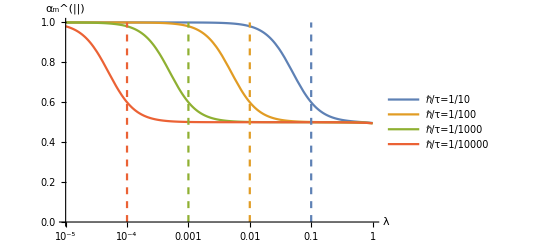

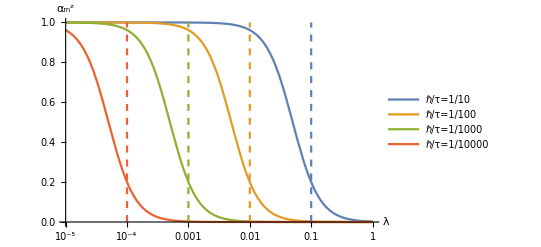

```mathematica
nsub = {Δ->0,nx->0.5,nz->Sqrt[1-nx nx],ϵ->10};
makeeven[expr_]:=(expr +(expr/.nz->-nz/.nx->-nx))/2
makeodd[expr_]:=(expr -(expr/.nz->-nz/.nx->-nx))/2

Clear[expr];
expr1=T0[[1,1]]/.Δ->0//Simplify//makeeven//ComplexExpand//Simplify;
expr2=T0[[3,3]]/.Δ->0//Simplify//makeeven//ComplexExpand//Simplify;

coeff[αp_,expr_]:=expr//.nsub/.{α->αp}
SetAttributes[coeff,Listable];

iτs = Table[10^-n,{n,{1,2,3,4}}];
iτslabels = {HoldForm[ℏ/τ = 1/10],HoldForm[ℏ/τ = 1/100],HoldForm[ℏ/τ = 1/1000],HoldForm[ℏ/τ = 1/10000]};
αs = 1/(π ϵ /.nsub)iτs;
lines =  Table[{{iτ,0.0},{iτ,1}},{iτ,iτs}];
LogLinearPlot[Evaluate@coeff[αs,expr1],{λ,10^-5,1},PlotRange->{{10^-5,1},{0,1}},PlotLegends->iτslabels,AxesLabel->{"λ","α_m^(||)"}];
ListLogLinearPlot[lines,PlotStyle->{{Dashed}},Joined->True];
Show[%%,%]

LogLinearPlot[Evaluate@coeff[αs,expr2],{λ,10^-5,1},PlotRange->{{10^-5,1},{0,1}},PlotLegends->iτslabels,AxesLabel->{"λ","α_m^z"}];
ListLogLinearPlot[lines,PlotStyle->{{Dashed}},Joined->True];
Show[%%,%]
```

#### use Λ = λ/ϵ, ϵ τ = 1/(π α), x = λ τ = Λ ϵ τ α_zz=(4-Λ^2)/(4+4 x^2)

```mathematica
expr1=T0[[1,1]]/.Δ->0//Simplify//makeeven//ComplexExpand//Simplify
%/.λ->Λ ϵ/2/.α->1/(π τ ϵ)//Simplify
%/.ϵ->x/(Λ τ)//Simplify
expr2=T0[[3,3]]/.Δ->0//Simplify//makeeven//ComplexExpand//Simplify
%/.λ->Λ ϵ/2/.α->1/(π τ ϵ)//Simplify
%/.ϵ->x/(Λ τ)
```

(π^2 α^2 ϵ^2 (2 ϵ^2-3 λ^2)+4 λ^2 (ϵ^2-2 λ^2))/(2 (ϵ-λ) (ϵ+λ) (π^2 α^2 ϵ^2+4 λ^2))

(-8+2 ϵ^2 Λ^4 τ^2+Λ^2 (3-4 ϵ^2 τ^2))/(2 (-2+Λ) (2+Λ) (1+ϵ^2 Λ^2 τ^2))

(-8+3 Λ^2+2 x^2 (-2+Λ^2))/(2 (1+x^2) (-2+Λ) (2+Λ))

(π^2 α^2 (ϵ^2-λ^2))/(π^2 α^2 ϵ^2+4 λ^2)

(4-Λ^2)/(4+4 ϵ^2 Λ^2 τ^2)

(4-Λ^2)/(4+4 x^2)

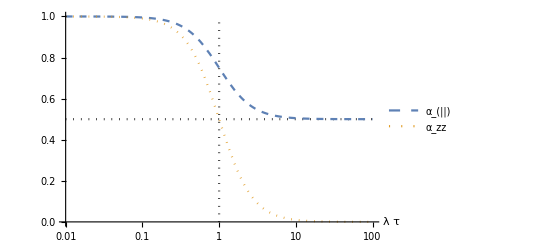

```mathematica
LogLinearPlot[Evaluate[{(-8+3 Λ^2+2 x^2 (-2+Λ^2))/(2 (1+x^2) (-2+Λ) (2+Λ)),(4-Λ^2)/(4+4 x^2)}/.Λ->0], {x,10^-2,10^2},PlotRange->{{10^-2,10^2},{0,1}},AxesLabel->{λ τ}, PlotLegends->{"α_(||)", "α_zz"},PlotStyle->{{Thick,Dashed}, {Thick,Dotted}}];
(*vertical line*)
ListLogLinearPlot[{{{1,0},{1,1}},{{0.01,0.5},{100,0.5}}},PlotStyle->{{Black, Dotted}},Joined->True,PlotRange->{{10^-2,10^2},{0,1}},AxesLabel->{λ τ}];
Show[%,%%]
```

(-π^6 α^6 ϵ^4 λ^2 (ϵ^2+λ^2)+64 λ^4 (ϵ^4-3 ϵ^2 λ^2+4 λ^4)+16 π^2 α^2 ϵ^2 λ^2 (3 ϵ^4-15 ϵ^2 λ^2+14 λ^4)+4 π^4 α^4 ϵ^2 (4 ϵ^6-14 ϵ^4 λ^2+7 ϵ^2 λ^4+λ^6))/(16 (ϵ-λ)^2 (ϵ+λ)^2 (π^2 α^2 ϵ^2+4 λ^2)^2)

(256 ϵ^2 τ^2+16 ϵ^6 Λ^8 τ^6+4 Λ^2 (-1-56 ϵ^2 τ^2+48 ϵ^4 τ^4)+Λ^6 (ϵ^2 τ^2+56 ϵ^4 τ^4-48 ϵ^6 τ^6)+Λ^4 (-1+28 ϵ^2 τ^2-240 ϵ^4 τ^4+64 ϵ^6 τ^6))/(16 ϵ^2 (-2+Λ)^2 (2+Λ)^2 τ^2 (1+ϵ^2 Λ^2 τ^2)^2)

(-Λ^4 (4+Λ^2)+16 x^6 (4-3 Λ^2+Λ^4)+8 x^4 (24-30 Λ^2+7 Λ^4)+x^2 (256-224 Λ^2+28 Λ^4+Λ^6))/(16 x^2 (1+x^2)^2 (-2+Λ)^2 (2+Λ)^2)

-(16 π^2 α^2 ϵ^2 λ^2+π^6 α^6 ϵ^2 λ^2-8 π^4 α^4 (ϵ^4-3 ϵ^2 λ^2+λ^4))/(8 (π^2 α^2 ϵ^2+4 λ^2)^2)

(32 ϵ^2 τ^2+2 ϵ^2 Λ^4 τ^2-Λ^2 (1+24 ϵ^2 τ^2+16 ϵ^4 τ^4))/(32 (ϵ τ+ϵ^3 Λ^2 τ^3)^2)

-(16 x^4+Λ^4-2 x^2 (16-12 Λ^2+Λ^4))/(32 (x+x^3)^2)

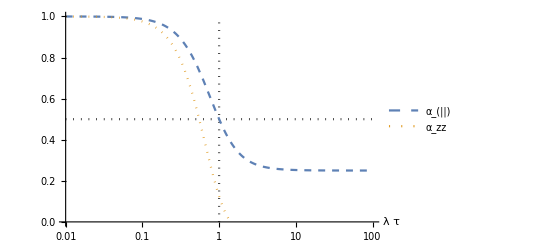

```mathematica
T1 = (T.T)[[MMindex,MMindex]];

expr1=T1[[1,1]]/.Δ->0//Simplify//makeeven//ComplexExpand//Simplify
%/.λ->Λ ϵ/2/.α->1/(π τ ϵ)//Simplify
expr1p=%/.ϵ->x/(Λ τ)//Simplify

expr2=T1[[3,3]]/.Δ->0//Simplify//makeeven//ComplexExpand//Simplify
%/.λ->Λ ϵ/2/.α->1/(π τ ϵ)//Simplify
expr2p=%/.ϵ->x/(Λ τ)//Simplify

LogLinearPlot[Evaluate[{expr1p,expr2p}/.Λ->0], {x,10^-2,10^2},PlotRange->{{10^-2,10^2},{0,1}},AxesLabel->{λ τ}, PlotLegends->{"α_(||)", "α_zz"},PlotStyle->{{Thick,Dashed}, {Thick,Dotted}}];
(*vertical line*)
ListLogLinearPlot[{{{1,0},{1,1}},{{0.01,0.5},{100,0.5}}},PlotStyle->{{Black, Dotted}},Joined->True,PlotRange->{{10^-2,10^2},{0,1}},AxesLabel->{λ τ}];
Show[%,%%]
```

```mathematica
proj = ({{1, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0}, {0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 1}})-({{nx nx, 0, nx nz, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {nx nz, 0, nz nz, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}});smallT=proj.T[[{2,3,4,5,9,13},{2,3,4,5,9,13}]]//ReplaceAll[#,ny->0]&//Simplify[#,Assumptions->nx nx+nz nz==1]&//makeeven//ComplexExpand//Simplify;
smallT//Limit[#,α->0]&//Limit[#,λ->0]&
smallTWithVertex = smallT.Inverse[IdentityMatrix[6]-smallT];
```

{{-(nz^2 (Δ^2-ϵ^2)^2)/(2 (nz Δ-ϵ) (nz Δ+ϵ) (Δ^2+ϵ^2)),0,(nx nz Δ^2 (Δ^2-ϵ^2) (ϵ^2+nz^2 (Δ^2-2 ϵ^2)))/(2 (nz Δ-ϵ)^2 (nz Δ+ϵ)^2 (Δ^2+ϵ^2)),0,0,(nx nz Δ^2 (Δ^2-ϵ^2) (ϵ^2+nz^2 (Δ^2-2 ϵ^2)))/(2 (nz Δ-ϵ)^2 (nz Δ+ϵ)^2 (Δ^2+ϵ^2))},{0,-((-nz^2 Δ^2+ϵ^2)^2 (Δ^8+2 Δ^6 ϵ^2-2 Δ^2 ϵ^6-ϵ^8))/(2 (-nz Δ+ϵ)^2 (nz Δ+ϵ)^2 (Δ^2+ϵ^2)^4),0,0,0,0},{(nx nz (nz^2 Δ^2-ϵ^2) (Δ^8-2 Δ^4 ϵ^4+ϵ^8))/(2 (-nz Δ+ϵ)^2 (nz Δ+ϵ)^2 (Δ^2+ϵ^2)^3),0,((-1+nz^2) Δ^2 (ϵ^2 (Δ^8+2 Δ^6 ϵ^2-2 Δ^2 ϵ^6-ϵ^8)+nz^2 (Δ^10-4 Δ^6 ϵ^4-2 Δ^4 ϵ^6+3 Δ^2 ϵ^8+2 ϵ^10)))/(2 (-nz Δ+ϵ)^2 (nz Δ+ϵ)^2 (Δ^2+ϵ^2)^4),0,0,((-1+nz^2) Δ^2 (ϵ^2 (Δ^8+2 Δ^6 ϵ^2-2 Δ^2 ϵ^6-ϵ^8)+nz^2 (Δ^10-4 Δ^6 ϵ^4-2 Δ^4 ϵ^6+3 Δ^2 ϵ^8+2 ϵ^10)))/(2 (-nz Δ+ϵ)^2 (nz Δ+ϵ)^2 (Δ^2+ϵ^2)^4)},{0,0,0,-((-nz^2 Δ^2+ϵ^2)^2 (Δ^8+2 Δ^6 ϵ^2-2 Δ^2 ϵ^6-ϵ^8))/(2 (-nz Δ+ϵ)^2 (nz Δ+ϵ)^2 (Δ^2+ϵ^2)^4),0,0},{0,0,0,0,-((-nz^2 Δ^2+ϵ^2)^2 (Δ^8+2 Δ^6 ϵ^2-2 Δ^2 ϵ^6-ϵ^8))/(2 (-nz Δ+ϵ)^2 (nz Δ+ϵ)^2 (Δ^2+ϵ^2)^4),0},{(nx nz Δ^2 (nz^2 Δ^2-ϵ^2) (Δ^8+2 Δ^6 ϵ^2-2 Δ^2 ϵ^6-ϵ^8))/(2 (-nz Δ+ϵ)^2 (nz Δ+ϵ)^2 (Δ^2+ϵ^2)^4),0,((-1+nz^2) Δ^2 (nz^2 Δ^2 (Δ^8+2 Δ^6 ϵ^2-2 Δ^2 ϵ^6-ϵ^8)+ϵ^2 (Δ^8+2 Δ^6 ϵ^2-2 Δ^2 ϵ^6-ϵ^8)))/(2 (-nz Δ+ϵ)^2 (nz Δ+ϵ)^2 (Δ^2+ϵ^2)^4),0,0,((-1+nz^2) Δ^2 (nz^2 Δ^2 (Δ^8+2 Δ^6 ϵ^2-2 Δ^2 ϵ^6-ϵ^8)+ϵ^2 (Δ^8+2 Δ^6 ϵ^2-2 Δ^2 ϵ^6-ϵ^8)))/(2 (-nz Δ+ϵ)^2 (nz Δ+ϵ)^2 (Δ^2+ϵ^2)^4)}}

```mathematica
smallT/.Δ->0//makeeven;
%/.λ->ϵ Λ/2/.α->1/(π τ ϵ)//Simplify;
(*%/.ϵ->x/(Λ τ);*)
mat0=%//Part[#,{1,2,3},{1,2,3}]&//Simplify[#,nx nx+nz nz==1]&
mat1=%%.Inverse[IdentityMatrix[6]-proj.%%]//Part[#,{1,2,3},{1,2,3}]&//Simplify[#,nx nx+nz nz==1]&
```

{{(nz^2 (-8+2 ϵ^2 Λ^4 τ^2+Λ^2 (3-4 ϵ^2 τ^2)))/(2 (-2+Λ) (2+Λ) (1+ϵ^2 Λ^2 τ^2)),0,(nx nz (-4+Λ^2))/(4+4 ϵ^2 Λ^2 τ^2)},{0,(-8+2 ϵ^2 Λ^4 τ^2+Λ^2 (3-4 ϵ^2 τ^2))/(2 (-2+Λ) (2+Λ) (1+ϵ^2 Λ^2 τ^2)),0},{(nx nz (8-2 ϵ^2 Λ^4 τ^2+Λ^2 (-3+4 ϵ^2 τ^2)))/(2 (-2+Λ) (2+Λ) (1+ϵ^2 Λ^2 τ^2)),0,((-1+nz^2) (-4+Λ^2))/(4+4 ϵ^2 Λ^2 τ^2)}}

{{-(2 nz^2 (-8+32 ϵ^2 τ^2+4 ϵ^4 Λ^6 τ^4+3 Λ^2 (1-4 ϵ^2 τ^2)^2+ϵ^2 Λ^4 τ^2 (7-16 ϵ^2 τ^2+16 ϵ^4 τ^4)))/(Λ^2 (1+4 ϵ^2 τ^2) (4-16 ϵ^2 τ^2-2 ϵ^2 Λ^4 τ^2-Λ^2 (1-4 ϵ^2 τ^2)^2+nz^2 (-2+8 ϵ^2 τ^2+2 ϵ^2 Λ^4 τ^2+Λ^2 (1-6 ϵ^2 τ^2+8 ϵ^4 τ^4)))),0,-(nx nz (-4+Λ^2) (-4+16 ϵ^2 τ^2+2 ϵ^2 Λ^4 τ^2+Λ^2 (1-4 ϵ^2 τ^2)^2))/(Λ^2 (1+4 ϵ^2 τ^2) (4-16 ϵ^2 τ^2-2 ϵ^2 Λ^4 τ^2-Λ^2 (1-4 ϵ^2 τ^2)^2+nz^2 (-2+8 ϵ^2 τ^2+2 ϵ^2 Λ^4 τ^2+Λ^2 (1-6 ϵ^2 τ^2+8 ϵ^4 τ^4))))},{0,(-8+32 ϵ^2 τ^2+4 ϵ^2 Λ^4 τ^2+Λ^2 (3-16 ϵ^2 τ^2+16 ϵ^4 τ^4))/(Λ^2 (-1+16 ϵ^4 τ^4)),0},{(2 nx nz (-8+32 ϵ^2 τ^2+4 ϵ^4 Λ^6 τ^4+3 Λ^2 (1-4 ϵ^2 τ^2)^2+ϵ^2 Λ^4 τ^2 (7-16 ϵ^2 τ^2+16 ϵ^4 τ^4)))/(Λ^2 (1+4 ϵ^2 τ^2) (4-16 ϵ^2 τ^2-2 ϵ^2 Λ^4 τ^2-Λ^2 (1-4 ϵ^2 τ^2)^2+nz^2 (-2+8 ϵ^2 τ^2+2 ϵ^2 Λ^4 τ^2+Λ^2 (1-6 ϵ^2 τ^2+8 ϵ^4 τ^4)))),0,-((-1+nz^2) (-4+Λ^2) (-4+16 ϵ^2 τ^2+2 ϵ^2 Λ^4 τ^2+Λ^2 (1-4 ϵ^2 τ^2)^2))/(Λ^2 (1+4 ϵ^2 τ^2) (4-16 ϵ^2 τ^2-2 ϵ^2 Λ^4 τ^2-Λ^2 (1-4 ϵ^2 τ^2)^2+nz^2 (-2+8 ϵ^2 τ^2+2 ϵ^2 Λ^4 τ^2+Λ^2 (1-6 ϵ^2 τ^2+8 ϵ^4 τ^4))))}}

```mathematica
c0=mat0[[3,3]]/.nz->0/.ϵ->x/(Λ τ)//Simplify;c0/.x->λ τ/.Λ->λ/ϵ
c1=mat1[[3,3]]/.nz->0/.ϵ->x/(Λ τ)//Simplify;c1/.x->λ τ/.Λ->λ/ϵ

LogLinearPlot[Evaluate[{c0,c1}/.Λ->0],{x,10^-2,10^2},PlotStyle->{Dashed,Dotted},PlotLegends->{"ϵτ α_zz(bare)","ϵτ α_zz(dressed)"},PlotRange->{All,{0,2}},AxesLabel->{"λ τ",None}]
```

(4-λ^2/ϵ^2)/(4+4 λ^2 τ^2)

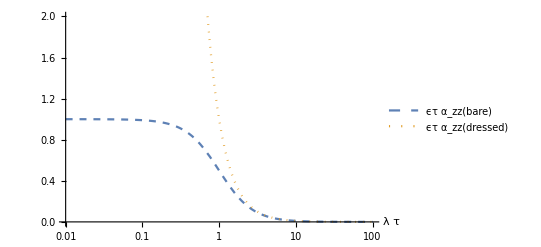

```mathematica
(4-λ^2/ϵ^2)/(λ^2/ϵ^2+4 λ^2 τ^2)
```

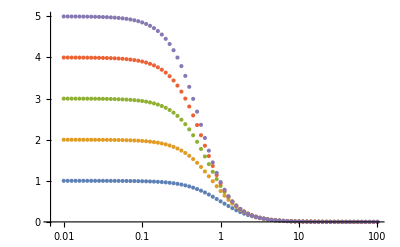

```mathematica
ClearAll[makeαzz]
makeαzz[n_]:=Block[{tmp},
tmp=smallT/.Δ->0//makeeven;
tmp=tmp/.λ->ϵ Λ/2/.α->Λ/(π x)//Simplify;
tmp=Sum[MatrixPower[tmp,i],{i,1,n}]//Part[#,3,3]&//Simplify[#,nx nx+nz nz==1]&//ReplaceAll[#,nz->0]&;
tmp/.{Λ->0}
]

αs = Table[makeαzz[n],{n,1,5}];
data = Table[Table[{x,αs[[i]]},{x,Table[10^n,{n,-2,2,0.05}]}],{i,1,5}];
Export["~/alpha1.csv",data[[1]]];
Export["~/alpha2.csv",data[[2]]];
Export["~/alpha3.csv",data[[3]]];
Export["~/alpha4.csv",data[[4]]];
Export["~/alpha5.csv",data[[5]]];

ListLogLinearPlot[data]
```

{-(-8-4 x^2)/(8 (1+x^2)),(512+640 x^2+192 x^4)/(256 (1+x^2)^2),-(-24576 x^2-49152 x^4-32768 x^6-7168 x^8)/(8192 x^2 (1+x^2)^3),(1048576 x^4+2883584 x^6+3014656 x^8+1409024 x^10+245760 x^12)/(262144 x^4 (1+x^2)^4),-(-41943040 x^6-146800640 x^8-209715200 x^10-152043520 x^12-55574528 x^14-8126464 x^16)/(8388608 x^6 (1+x^2)^5)}

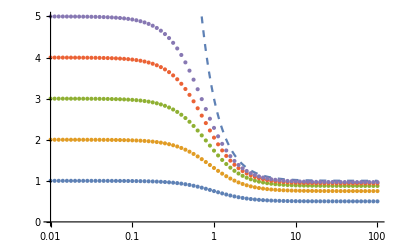

```mathematica
makeαpara[n_]:=Block[{tmp},
tmp=smallT/.Δ->0//makeeven;
tmp=tmp/.λ->ϵ Λ/2/.α->Λ/(π x)//Simplify;
tmp=Sum[MatrixPower[tmp,i],{i,1,n}]//Part[#,2,2]&//Simplify[#,nx nx+nz nz==1]&//ReplaceAll[#,nz->0]&;
tmp/.{Λ->0}
]
αs = Table[makeαpara[n],{n,1,5}]
data = Table[Table[{x,αs[[i]]},{x,Table[10^n,{n,-2,2,0.05}]}],{i,1,5}];
Export["~/alpha_p1.csv",data[[1]]];
Export["~/alpha_p2.csv",data[[2]]];
Export["~/alpha_p3.csv",data[[3]]];
Export["~/alpha_p4.csv",data[[4]]];
Export["~/alpha_p5.csv",data[[5]]];

ListLogLinearPlot[data,PlotRange->{{10^-2,10^2},{0,5}}];
LogLinearPlot[Simplify[mat1[[2,2]]/.ϵ->x/(Λ τ)]/.Λ->0,{x,10^-2,10^2},PlotRange->{{10^-2,10^2},{0,5}},PlotStyle->Dashed];
Show[%,%%]
```

```mathematica
%473//Series[#,{x,∞,3}]&
%473//Series[#,{x,0,3}]&
```

{1/2+1/(2 x^2)+O[1/x]^4,3/4+(1/x)^2+O[1/x]^4,7/8+11/(8 x^2)+O[1/x]^4,15/16+13/(8 x^2)+O[1/x]^4,31/32+57/(32 x^2)+O[1/x]^4}

{1-x^2/2+O[x]^4,2-(3 x^2)/2+O[x]^4,3-3 x^2+O[x]^4,4-5 x^2+O[x]^4,5-(15 x^2)/2+O[x]^4}

(3+2 x^2)/(2 (1+x^2))+1/(2 (-2+Λ))-1/(2 (2+Λ))

(16 x^4+Λ^2 (-8+3 Λ^2)+4 x^2 (8-4 Λ^2+Λ^4))/(16 x^4-Λ^4)

-3-4 x^2-(2 x^3)/(-2 x+Λ)+(2 x^3)/(2 x+Λ)+(8 (1+2 x^2+x^4))/(4 x^2+Λ^2)

1+Λ^3/(4 (2 x-Λ))-Λ^3/(4 (2 x+Λ))+(16-8 Λ^2+Λ^4)/(2 (4 x^2+Λ^2))

-3-4 x^2-(2 x^3)/(-2 x+Λ)+(2 x^3)/(2 x+Λ)+(8 (1+2 x^2+x^4))/(4 x^2+Λ^2)

(2+x^2)/x^2-((1+2 x^2) Λ^2)/(2 x^4)

(2+x^2)/x^2+((-8-16 x^2) Λ^2)/(16 x^4)+O[Λ]^3

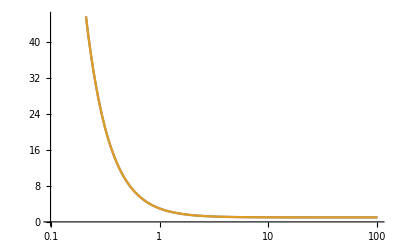

```mathematica
mat0[[2,2]]/.ϵ->x/(Λ τ)//Simplify//Apart
mat1[[2,2]]/.ϵ->x/(Λ τ)//Simplify
%//Apart
%//Apart[#,x]&
%//Apart[#,Λ]&
%//Series[#,{Λ,0,2}]&//Normal//Apart
mat1[[2,2]]/.ϵ->x/(Λ τ)//Simplify//Series[#,{Λ,0,2}]&
LogLinearPlot[Evaluate[{(mat1[[2,2]]/.ϵ->x/(Λ τ)//Simplify)/.Λ->0.01,(mat1[[2,2]]/.ϵ->x/(Λ τ)//Simplify)/.Λ->0}],{x,10^-1,10^2}]
```

```mathematica
mat1[[2,2]]/.ϵ->x/(Λ τ)//Simplify//Series[#,{x,∞,4}]&
```

1+(8-4 Λ^2+Λ^4)/(4 x^2)+(-2 Λ^2+Λ^4)/(4 x^4)+O[1/x]^5

```mathematica
(1-x^2)/(x^2+y^2)//Series[#,{x,0,2}]&
```

1/y^2+(-1/y^4-1/y^2) x^2+O[x]^3

```mathematica
(2+x^2)/x^2-((1+2 x^2) Λ^2)/(2 x^4)//Series[#,{x,0,2}]&
```

-Λ^2/(2 x^4)+(2-Λ^2)/x^2+1+O[x]^3

```mathematica
Λ^3/(4 (2 x-Λ))-Λ^3/(4 (2 x+Λ))//Simplify
```

Λ^4/(8 x^2-2 Λ^2)

```mathematica
1/(2 (-2+Λ))-1/(2 (2+Λ))//Simplify
```

2/(-4+Λ^2)

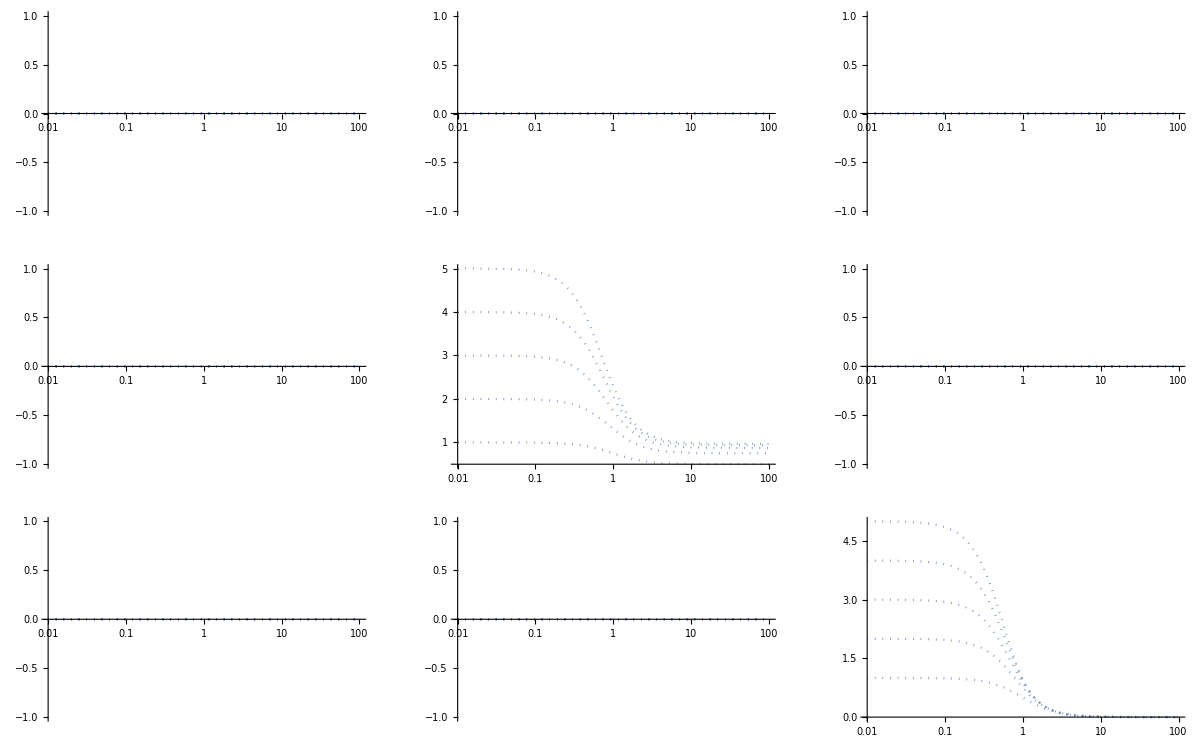

```mathematica
makeα[n_]:=Block[{tmp},
tmp=smallT/.Δ->0//makeeven;
tmp=tmp/.λ->ϵ Λ/2/.α->Λ/(π x)//Simplify;
tmp=Sum[MatrixPower[tmp,i],{i,1,n}]//Simplify[#,nx nx+nz nz==1]&//ReplaceAll[#,nz->0]&;
tmp/.{Λ->0}
]

αtens = Table[makeα[n],{n,1,5}];

GraphicsGrid@Table[LogLinearPlot[Table[αtens[[i]][[k,m]],{i,1,5}],{x,10^-2,10^2},PlotStyle->Dotted],{k,1,3},{m,1,3}]
```

```mathematica
αtens[[1,1]]
```

{0,0,0,0,0,0}

```mathematica
αs//Series[#,{x,∞,5}]&
```

{(1/x)^2-(1/x)^4+O[1/x]^6,(1/x)^2+O[1/x]^6,(1/x)^2+O[1/x]^6,(1/x)^2+O[1/x]^6,(1/x)^2+O[1/x]^6}

```mathematica
αs//Series[#,{x,0,2}]&
```

{1-x^2+O[x]^3,2-3 x^2+O[x]^3,3-6 x^2+O[x]^3,4-10 x^2+O[x]^3,5-15 x^2+O[x]^3}

-(Δ^2-ϵ^2)/(2 Δ^2)

```mathematica
smallTWithVertex[[{1,2,3},{1,2,3}]]//Limit[#,Δ->0]&//Limit[#,α->0]&//Limit[#,λ->0]&;
%[[3,3]]//Simplify
smallTWithVertex[[{1,2,3},{1,2,3}]]//Limit[#,α->0]&//Limit[#,Δ->0]&//Limit[#,λ->0]&;
%[[3,3]]//Simplify
smallTWithVertex[[{1,2,3},{1,2,3}]]//Limit[#,α->0]&//Limit[#,λ->0]&//Limit[#,Δ->0]&;
%[[3,3]]//Simplify

smallTWithVertex[[{1,2,3},{1,2,3}]]//Limit[#,Δ->0]&//Limit[#,λ->0]&//Limit[#,α->0]&;
%[[3,3]]//Simplify
smallTWithVertex[[{1,2,3},{1,2,3}]]//Limit[#,λ->0]&//Limit[#,Δ->0]&//Limit[#,α->0]&;
%[[3,3]]//Simplify
smallTWithVertex[[{1,2,3},{1,2,3}]]//Limit[#,λ->0]&//Limit[#,α->0]&//Limit[#,Δ->0]&;
%[[3,3]]//Simplify
```

0

0

0

-(1+(-2+nx^2) nz^2+nz^4)/(nz^2 (-1+nx^2+nz^2))

-(1+(-2+nx^2) nz^2+nz^4)/(nz^2 (-1+nx^2+nz^2))

-(1+(-2+nx^2) nz^2+nz^4)/(nz^2 (-1+nx^2+nz^2))

```mathematica
smallT//Limit[#,α->0]&//Limit[#,λ->0]&//Limit[#,Δ->0]&
```

{{nz^2/2,0,0,0,0,0},{0,1/2,0,0,0,0},{-(nx nz)/2,0,0,0,0,0},{0,0,0,1/2,0,0},{0,0,0,0,1/2,0},{0,0,0,0,0,0}}

```mathematica
proj =  ({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})-({{nx nx, 0, nx nz}, {0, 0, 0}, {nx nz, 0, nz nz}});
T1/.Δ->0//Simplify//makeeven//ComplexExpand//Simplify;
%/.λ->Λ ϵ/2/.α->1/(π τ ϵ)//Simplify;
%/.ϵ->x/(Λ τ)//Simplify
%/.x->0
```

{{(-Λ^4 (4+Λ^2)+16 x^6 (4-3 Λ^2+Λ^4)+8 x^4 (24-30 Λ^2+7 Λ^4)+x^2 (256-224 Λ^2+28 Λ^4+Λ^6))/(16 x^2 (1+x^2)^2 (-2+Λ)^2 (2+Λ)^2),0,0},{0,(-Λ^4 (4+Λ^2)+16 x^6 (4-3 Λ^2+Λ^4)+8 x^4 (24-30 Λ^2+7 Λ^4)+x^2 (256-224 Λ^2+28 Λ^4+Λ^6))/(16 x^2 (1+x^2)^2 (-2+Λ)^2 (2+Λ)^2),0},{0,0,-(16 x^4+Λ^4-2 x^2 (16-12 Λ^2+Λ^4))/(32 (x+x^3)^2)}}

Power::infy: Infinite expression 1/0^2 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

{{ComplexInfinity,0,0},{0,ComplexInfinity,0},{0,0,ComplexInfinity}}

### Δ → !0

```mathematica
T0[[3,3]]/.Δ->0//Simplify//makeeven//ComplexExpand//Simplify
%/.λ->Λ ϵ/2/.α->1/(π τ ϵ)//Simplify
%/.ϵ->x/(Λ τ)//Simplify
```

(π^2 α^2 (ϵ^2-λ^2))/(π^2 α^2 ϵ^2+4 λ^2)

(4-Λ^2)/(4+4 ϵ^2 Λ^2 τ^2)

(4-Λ^2)/(4+4 x^2)

```mathematica
expr1=T0[[1,1]]//Simplify//makeeven//ComplexExpand//Simplify[#,Assumptions->nx nx+nz nz==1]&;
expr1/.λ->Λ ϵ/2/.α->1/(π τ ϵ)//Simplify;
expr1p=%/.ϵ->x/(Λ τ)//Simplify;
%/.Δ->0//Simplify
expr2=T0[[3,3]]//Simplify//makeeven//ComplexExpand//Simplify[#,Assumptions->nx nx+nz nz==1]&;
expr2/.λ->Λ ϵ/2/.α->1/(π τ ϵ)//Simplify;
expr2p=%/.ϵ->x/(Λ τ)//Simplify;
%/.Δ->0//Simplify
```

(-8+3 Λ^2+2 x^2 (-2+Λ^2))/(2 (1+x^2) (-2+Λ) (2+Λ))

(4-Λ^2)/(4+4 x^2)

```mathematica
expr1p
```

-((nz^8 x^8 Δ^8 Λ^12 τ^8 (4 x^4+4 x^6+Δ^2 Λ^4 τ^2+x^2 Λ^2 (1+4 Δ^2 τ^2))+nz^6 x^4 Δ^6 Λ^8 τ^6 (Λ^4 (x^2+Δ^2 Λ^2 τ^2)^3-x^2 Λ^2 (x^2+Δ^2 Λ^2 τ^2)^2 (x^2 (4+Λ^2)+4 Δ^2 Λ^2 τ^2)-8 x^8 (x^4 (1+Λ^2)+4 x^2 Δ^2 Λ^2 τ^2+3 Δ^4 Λ^4 τ^4)-2 x^4 (x^2+Δ^2 Λ^2 τ^2) (x^4 (16+3 Λ^2)+x^2 Δ^2 Λ^2 (32-3 Λ^2) τ^2+16 Δ^4 Λ^4 τ^4))-(-x^4 (-4+Λ^2)+8 x^2 Δ^2 Λ^2 τ^2+4 Δ^4 Λ^4 τ^4) (-4 x^18 (-2+Λ^2)-8 x^14 Δ^4 Λ^4 τ^4+Δ^2 Λ^4 τ^2 (x^2+Δ^2 Λ^2 τ^2)^3 (-x^4 (-4+Λ^2)+8 x^2 Δ^2 Λ^2 τ^2+4 Δ^4 Λ^4 τ^4)+2 x^8 (x^2+Δ^2 Λ^2 τ^2) (x^6 (12-5 Λ^2)-x^4 Δ^2 Λ^2 (-20+Λ^2) τ^2+4 x^2 Δ^4 Λ^4 τ^4-4 Δ^6 Λ^6 τ^6)+x^4 (x^2+Δ^2 Λ^2 τ^2) (x^8 (16-6 Λ^2)-x^6 Δ^2 Λ^2 (-64+6 Λ^2+Λ^4) τ^2+6 x^4 Δ^4 Λ^4 (16+Λ^2) τ^4+2 x^2 Δ^6 Λ^6 (32+3 Λ^2) τ^6+16 Δ^8 Λ^8 τ^8))+nz^2 Δ^2 Λ^2 τ^2 (8 x^12 (x^8 (8-7 Λ^2+Λ^4)+4 x^6 Δ^2 Λ^2 (4-3 Λ^2) τ^2-5 x^4 Δ^4 Λ^6 τ^4-16 x^2 Δ^6 Λ^6 τ^6-8 Δ^8 Λ^8 τ^8)+Λ^2 (x^2+Δ^2 Λ^2 τ^2)^3 (x^8 (-4+Λ^2)^2+2 x^6 Δ^2 Λ^2 (32-4 Λ^2+Λ^4) τ^2+8 x^4 Δ^4 Λ^4 (12+Λ^2) τ^4+8 x^2 Δ^6 Λ^6 (8+Λ^2) τ^6+16 Δ^8 Λ^8 τ^8)-2 x^6 (x^2+Δ^2 Λ^2 τ^2) (x^10 (16-32 Λ^2+5 Λ^4)+x^8 Δ^2 Λ^2 (48-48 Λ^2+11 Λ^4) τ^2+32 x^6 Δ^4 Λ^4 τ^4+16 x^4 Δ^6 Λ^6 (-2+Λ^2) τ^6-48 x^2 Δ^8 Λ^8 τ^8-16 Δ^10 Λ^10 τ^10)+(x^3+x Δ^2 Λ^2 τ^2)^2 (x^10 (64+24 Λ^2-8 Λ^4+Λ^6)+4 x^8 Δ^2 Λ^2 (80+12 Λ^2+5 Λ^4) τ^2+4 x^6 Δ^4 Λ^4 (160+7 Λ^4) τ^4+16 x^4 Δ^6 Λ^6 (40-3 Λ^2) τ^6+8 x^2 Δ^8 Λ^8 (40-3 Λ^2) τ^8+64 Δ^10 Λ^10 τ^10))-nz^4 x^2 Δ^4 Λ^4 τ^4 (x^2+Δ^2 Λ^2 τ^2) (-8 x^14 (-4+5 Λ^2)+8 Δ^8 Λ^12 τ^8+x^2 Δ^6 Λ^10 τ^6 (32+Λ^2+16 Δ^2 τ^2)+x^12 (-64+32 Λ^2 (1+Δ^2 τ^2)-2 Λ^4 (11+28 Δ^2 τ^2))+x^10 Λ^2 (16-256 Δ^2 τ^2+Λ^4 (1-18 Δ^2 τ^2)+Λ^2 (30+96 Δ^2 τ^2-32 Δ^4 τ^4))+2 x^4 Δ^4 Λ^8 τ^4 (Λ^2 (2-5 Δ^2 τ^2)+8 (3+4 Δ^2 τ^2-4 Δ^4 τ^4))+x^6 Δ^2 Λ^6 τ^2 (32 (1+3 Δ^2 τ^2-8 Δ^4 τ^4)+Λ^2 (5+10 Δ^2 τ^2+32 Δ^4 τ^4))+x^8 Λ^4 (8+64 Δ^2 τ^2-Δ^2 Λ^4 τ^2-384 Δ^4 τ^4+Λ^2 (2+50 Δ^2 τ^2+96 Δ^4 τ^4-32 Δ^6 τ^6))))/(4 x^2 (x^2 (-2+Λ)-nz x Δ Λ^2 τ-2 Δ^2 Λ^2 τ^2) (x^2 (-2+Λ)+nz x Δ Λ^2 τ-2 Δ^2 Λ^2 τ^2) (x^2 (2+Λ)-nz x Δ Λ^2 τ+2 Δ^2 Λ^2 τ^2) (x^2 (2+Λ)+nz x Δ Λ^2 τ+2 Δ^2 Λ^2 τ^2) (x^6-2 nz x^5 Δ Λ τ+2 x^2 Δ^2 Λ^2 τ^2+Δ^4 Λ^4 τ^4+x^4 (1+nz^2 Δ^2 Λ^2 τ^2)) (x^6+2 nz x^5 Δ Λ τ+2 x^2 Δ^2 Λ^2 τ^2+Δ^4 Λ^4 τ^4+x^4 (1+nz^2 Δ^2 Λ^2 τ^2))))

```mathematica
{expr1p,expr2p}/.Δ->{δ x/Λ τ}/.nz->0//Simplify
```

{{(4 x^4 (-2+Λ^2+2 δ^4 τ^8)+δ^2 Λ^2 τ^4 (1+δ^2 τ^4) (Λ^2-4 (1+δ^2 τ^4)^2)-2 x^2 (1+δ^2 τ^4) (Λ^2 (-3+δ^2 τ^4)+8 (1+δ^2 τ^4)^2))/(4 x^2 (-2+Λ-2 δ^2 τ^4) (2+Λ+2 δ^2 τ^4) (x^2+(1+δ^2 τ^4)^2))},{(-Λ^4 (1+δ^2 τ^4)+8 (-1+δ^4 τ^8) (2+(4+x^2) δ^2 τ^4+2 δ^4 τ^8)+2 Λ^2 (4+(7+2 x^2) δ^2 τ^4+4 δ^4 τ^8+δ^6 τ^12))/(4 (-2+Λ-2 δ^2 τ^4) (2+Λ+2 δ^2 τ^4) (x^2+(1+δ^2 τ^4)^2))}}

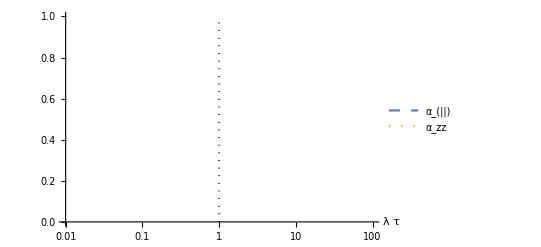

```mathematica
LogLinearPlot[Evaluate[{expr1p,expr2p}/.Δ->{δ x/Λ τ}/.Λ->0.01/.δ->0.01], {x,10^-2,10^2},PlotRange->{{10^-2,10^2},{0,1}},AxesLabel->{λ τ}, PlotLegends->{"α_(||)", "α_zz"},PlotStyle->{{Thick,Dashed}, {Thick,Dotted}}];
(*vertical line*)
ListLogLinearPlot[{{1,0},{1,1}},PlotStyle->{{Black,Dotted}},Joined->True,PlotRange->{{10^-2,10^2},{0,1}},AxesLabel->{λ τ}];
Show[%,%%]
```

```mathematica
smallT//Simplify[#,nx nx+nz nz==1]&
```

smallT

```mathematica
Simplify[({{f[1,1], 0, f[1,3], f[1,4]}, {0, f[2,2], 0, 0}, {f[1,3], 0, f[3,3], f[3,4]}, {f[1,4], 0, f[3,4], f[4,4]}}).Inverse[IdentityMatrix[4]-({{f[1,1], 0, f[1,3], f[1,4]}, {0, f[2,2], 0, 0}, {f[1,3], 0, f[3,3], f[3,4]}, {f[1,4], 0, f[3,4], f[4,4]}})]]
%/.f[i_,j_]->%1223[[i,j]]//Simplify[#,nx nx+nz nz==1]&
```

(1)
 |  |  |  |

(((f(4,4)-1) (f(1,3))^2-2 f(1,4) f(3,4) f(1,3)+(f(1,4))^2 (f(3,3)-1)+f(1,1) ((f(3,4))^2-f(3,3) (f(4,4)-1)+f(4,4)-1))/(-(f(4,4)-1) (f(1,3))^2+2 f(1,4) f(3,4) f(1,3)+(f(1,4))^2+(f(3,4))^2-(f(1,4))^2 f(3,3)+f(3,3)-f(3,3) f(4,4)+f(4,4)-f(1,1) ((f(3,4))^2-f(3,3) (f(4,4)-1)+f(4,4)-1)-1) | 0 | (f(1,3) (f(4,4)-1)-f(1,4) f(3,4))/(-(f(4,4)-1) (f(1,3))^2+2 f(1,4) f(3,4) f(1,3)+(f(1,4))^2+(f(3,4))^2-(f(1,4))^2 f(3,3)+f(3,3)-f(3,3) f(4,4)+f(4,4)-f(1,1) ((f(3,4))^2-f(3,3) (f(4,4)-1)+f(4,4)-1)-1) | (f(1,4) (f(3,3)-1)-f(1,3) f(3,4))/(-(f(4,4)-1) (f(1,3))^2+2 f(1,4) f(3,4) f(1,3)+(f(1,4))^2+(f(3,4))^2-(f(1,4))^2 f(3,3)+f(3,3)-f(3,3) f(4,4)+f(4,4)-f(1,1) ((f(3,4))^2-f(3,3) (f(4,4)-1)+f(4,4)-1)-1)
0 | (f(2,2))/(1-f(2,2)) | 0 | 0
(f(1,3) (f(4,4)-1)-f(1,4) f(3,4))/(-(f(4,4)-1) (f(1,3))^2+2 f(1,4) f(3,4) f(1,3)+(f(1,4))^2+(f(3,4))^2-(f(1,4))^2 f(3,3)+f(3,3)-f(3,3) f(4,4)+f(4,4)-f(1,1) ((f(3,4))^2-f(3,3) (f(4,4)-1)+f(4,4)-1)-1) | 0 | ((f(4,4)-1) (f(1,3))^2-2 f(1,4) f(3,4) f(1,3)+(f(1,1)-1) (f(3,4))^2+f(3,3) ((f(1,4))^2+f(1,1)-f(1,1) f(4,4)+f(4,4)-1))/(-(f(4,4)-1) (f(1,3))^2+2 f(1,4) f(3,4) f(1,3)+(f(1,4))^2+(f(3,4))^2-(f(1,4))^2 f(3,3)+f(3,3)-f(3,3) f(4,4)+f(4,4)-f(1,1) ((f(3,4))^2-f(3,3) (f(4,4)-1)+f(4,4)-1)-1) | ((f(1,1)-1) f(3,4)-f(1,3) f(1,4))/(-(f(4,4)-1) (f(1,3))^2+2 f(1,4) f(3,4) f(1,3)+(f(1,4))^2+(f(3,4))^2-(f(1,4))^2 f(3,3)+f(3,3)-f(3,3) f(4,4)+f(4,4)-f(1,1) ((f(3,4))^2-f(3,3) (f(4,4)-1)+f(4,4)-1)-1)
(f(1,4) (f(3,3)-1)-f(1,3) f(3,4))/(-(f(4,4)-1) (f(1,3))^2+2 f(1,4) f(3,4) f(1,3)+(f(1,4))^2+(f(3,4))^2-(f(1,4))^2 f(3,3)+f(3,3)-f(3,3) f(4,4)+f(4,4)-f(1,1) ((f(3,4))^2-f(3,3) (f(4,4)-1)+f(4,4)-1)-1) | 0 | ((f(1,1)-1) f(3,4)-f(1,3) f(1,4))/(-(f(4,4)-1) (f(1,3))^2+2 f(1,4) f(3,4) f(1,3)+(f(1,4))^2+(f(3,4))^2-(f(1,4))^2 f(3,3)+f(3,3)-f(3,3) f(4,4)+f(4,4)-f(1,1) ((f(3,4))^2-f(3,3) (f(4,4)-1)+f(4,4)-1)-1) | ((f(3,3)-1) (f(1,4))^2-2 f(1,3) f(3,4) f(1,4)+(f(1,1)-1) (f(3,4))^2+((f(1,3))^2+f(1,1)-f(1,1) f(3,3)+f(3,3)-1) f(4,4))/(-(f(4,4)-1) (f(1,3))^2+2 f(1,4) f(3,4) f(1,3)+(f(1,4))^2+(f(3,4))^2-(f(1,4))^2 f(3,3)+f(3,3)-f(3,3) f(4,4)+f(4,4)-f(1,1) ((f(3,4))^2-f(3,3) (f(4,4)-1)+f(4,4)-1)-1))

Part::pkspec1: The expression i cannot be used as a part specification.

Part::partd: Part specification %1223⟦1,4⟧ is longer than depth of object.

Part::partw: Part 3 of %1223 does not exist.

Part::partd: Part specification %1223⟦1,4⟧ is longer than depth of object.

Part::partw: Part 3 of %1223 does not exist.

Part::partd: Part specification %1223⟦1,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 3 of %1223 does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

(((%1223⟦4,4⟧-1) (%1223⟦1,3⟧)^2-2 %1223⟦1,4⟧ %1223⟦3,4⟧ %1223⟦1,3⟧+(%1223⟦1,4⟧)^2 (%1223⟦3,3⟧-1)+%1223⟦1,1⟧ ((%1223⟦3,4⟧)^2-%1223⟦3,3⟧ (%1223⟦4,4⟧-1)+%1223⟦4,4⟧-1))/(-(%1223⟦4,4⟧-1) (%1223⟦1,3⟧)^2+2 %1223⟦1,4⟧ %1223⟦3,4⟧ %1223⟦1,3⟧+(%1223⟦1,4⟧)^2+(%1223⟦3,4⟧)^2-(%1223⟦1,4⟧)^2 %1223⟦3,3⟧+%1223⟦3,3⟧-%1223⟦3,3⟧ %1223⟦4,4⟧+%1223⟦4,4⟧-%1223⟦1,1⟧ ((%1223⟦3,4⟧)^2-%1223⟦3,3⟧ (%1223⟦4,4⟧-1)+%1223⟦4,4⟧-1)-1) | 0 | (%1223⟦1,3⟧ (%1223⟦4,4⟧-1)-%1223⟦1,4⟧ %1223⟦3,4⟧)/(-(%1223⟦4,4⟧-1) (%1223⟦1,3⟧)^2+2 %1223⟦1,4⟧ %1223⟦3,4⟧ %1223⟦1,3⟧+(%1223⟦1,4⟧)^2+(%1223⟦3,4⟧)^2-(%1223⟦1,4⟧)^2 %1223⟦3,3⟧+%1223⟦3,3⟧-%1223⟦3,3⟧ %1223⟦4,4⟧+%1223⟦4,4⟧-%1223⟦1,1⟧ ((%1223⟦3,4⟧)^2-%1223⟦3,3⟧ (%1223⟦4,4⟧-1)+%1223⟦4,4⟧-1)-1) | (%1223⟦1,4⟧ (%1223⟦3,3⟧-1)-%1223⟦1,3⟧ %1223⟦3,4⟧)/(-(%1223⟦4,4⟧-1) (%1223⟦1,3⟧)^2+2 %1223⟦1,4⟧ %1223⟦3,4⟧ %1223⟦1,3⟧+(%1223⟦1,4⟧)^2+(%1223⟦3,4⟧)^2-(%1223⟦1,4⟧)^2 %1223⟦3,3⟧+%1223⟦3,3⟧-%1223⟦3,3⟧ %1223⟦4,4⟧+%1223⟦4,4⟧-%1223⟦1,1⟧ ((%1223⟦3,4⟧)^2-%1223⟦3,3⟧ (%1223⟦4,4⟧-1)+%1223⟦4,4⟧-1)-1)
0 | (%1223⟦2,2⟧)/(1-%1223⟦2,2⟧) | 0 | 0
(%1223⟦1,3⟧ (%1223⟦4,4⟧-1)-%1223⟦1,4⟧ %1223⟦3,4⟧)/(-(%1223⟦4,4⟧-1) (%1223⟦1,3⟧)^2+2 %1223⟦1,4⟧ %1223⟦3,4⟧ %1223⟦1,3⟧+(%1223⟦1,4⟧)^2+(%1223⟦3,4⟧)^2-(%1223⟦1,4⟧)^2 %1223⟦3,3⟧+%1223⟦3,3⟧-%1223⟦3,3⟧ %1223⟦4,4⟧+%1223⟦4,4⟧-%1223⟦1,1⟧ ((%1223⟦3,4⟧)^2-%1223⟦3,3⟧ (%1223⟦4,4⟧-1)+%1223⟦4,4⟧-1)-1) | 0 | ((%1223⟦4,4⟧-1) (%1223⟦1,3⟧)^2-2 %1223⟦1,4⟧ %1223⟦3,4⟧ %1223⟦1,3⟧+(%1223⟦1,1⟧-1) (%1223⟦3,4⟧)^2+%1223⟦3,3⟧ ((%1223⟦1,4⟧)^2-%1223⟦1,1⟧ (%1223⟦4,4⟧-1)+%1223⟦4,4⟧-1))/(-(%1223⟦4,4⟧-1) (%1223⟦1,3⟧)^2+2 %1223⟦1,4⟧ %1223⟦3,4⟧ %1223⟦1,3⟧+(%1223⟦1,4⟧)^2+(%1223⟦3,4⟧)^2-(%1223⟦1,4⟧)^2 %1223⟦3,3⟧+%1223⟦3,3⟧-%1223⟦3,3⟧ %1223⟦4,4⟧+%1223⟦4,4⟧-%1223⟦1,1⟧ ((%1223⟦3,4⟧)^2-%1223⟦3,3⟧ (%1223⟦4,4⟧-1)+%1223⟦4,4⟧-1)-1) | ((%1223⟦1,1⟧-1) %1223⟦3,4⟧-%1223⟦1,3⟧ %1223⟦1,4⟧)/(-(%1223⟦4,4⟧-1) (%1223⟦1,3⟧)^2+2 %1223⟦1,4⟧ %1223⟦3,4⟧ %1223⟦1,3⟧+(%1223⟦1,4⟧)^2+(%1223⟦3,4⟧)^2-(%1223⟦1,4⟧)^2 %1223⟦3,3⟧+%1223⟦3,3⟧-%1223⟦3,3⟧ %1223⟦4,4⟧+%1223⟦4,4⟧-%1223⟦1,1⟧ ((%1223⟦3,4⟧)^2-%1223⟦3,3⟧ (%1223⟦4,4⟧-1)+%1223⟦4,4⟧-1)-1)
(%1223⟦1,4⟧ (%1223⟦3,3⟧-1)-%1223⟦1,3⟧ %1223⟦3,4⟧)/(-(%1223⟦4,4⟧-1) (%1223⟦1,3⟧)^2+2 %1223⟦1,4⟧ %1223⟦3,4⟧ %1223⟦1,3⟧+(%1223⟦1,4⟧)^2+(%1223⟦3,4⟧)^2-(%1223⟦1,4⟧)^2 %1223⟦3,3⟧+%1223⟦3,3⟧-%1223⟦3,3⟧ %1223⟦4,4⟧+%1223⟦4,4⟧-%1223⟦1,1⟧ ((%1223⟦3,4⟧)^2-%1223⟦3,3⟧ (%1223⟦4,4⟧-1)+%1223⟦4,4⟧-1)-1) | 0 | ((%1223⟦1,1⟧-1) %1223⟦3,4⟧-%1223⟦1,3⟧ %1223⟦1,4⟧)/(-(%1223⟦4,4⟧-1) (%1223⟦1,3⟧)^2+2 %1223⟦1,4⟧ %1223⟦3,4⟧ %1223⟦1,3⟧+(%1223⟦1,4⟧)^2+(%1223⟦3,4⟧)^2-(%1223⟦1,4⟧)^2 %1223⟦3,3⟧+%1223⟦3,3⟧-%1223⟦3,3⟧ %1223⟦4,4⟧+%1223⟦4,4⟧-%1223⟦1,1⟧ ((%1223⟦3,4⟧)^2-%1223⟦3,3⟧ (%1223⟦4,4⟧-1)+%1223⟦4,4⟧-1)-1) | ((%1223⟦3,3⟧-1) (%1223⟦1,4⟧)^2-2 %1223⟦1,3⟧ %1223⟦3,4⟧ %1223⟦1,4⟧+(%1223⟦1,1⟧-1) (%1223⟦3,4⟧)^2+((%1223⟦1,3⟧)^2-%1223⟦1,1⟧ (%1223⟦3,3⟧-1)+%1223⟦3,3⟧-1) %1223⟦4,4⟧)/(-(%1223⟦4,4⟧-1) (%1223⟦1,3⟧)^2+2 %1223⟦1,4⟧ %1223⟦3,4⟧ %1223⟦1,3⟧+(%1223⟦1,4⟧)^2+(%1223⟦3,4⟧)^2-(%1223⟦1,4⟧)^2 %1223⟦3,3⟧+%1223⟦3,3⟧-%1223⟦3,3⟧ %1223⟦4,4⟧+%1223⟦4,4⟧-%1223⟦1,1⟧ ((%1223⟦3,4⟧)^2-%1223⟦3,3⟧ (%1223⟦4,4⟧-1)+%1223⟦4,4⟧-1)-1))

```mathematica
T//Series[#,{ϵ,∞,2}]&
```

(1+(4 nx^2 Δ^2+4 nz^2 Δ^2+nx^2 π^2 α^2 Δ^2+nz^2 π^2 α^2 Δ^2+π^2 α^2 Δ^2-12 Δ^2)/(8 ϵ^2)+O((1/ϵ)^3) | 0 | O((1/ϵ)^3) | 0 | O((1/ϵ)^3) | 0 | (nz π^2 Δ λ α^2+4 nz Δ λ)/(8 ϵ^2)+O((1/ϵ)^3) | 0 | 0 | (-1/8 nz π^2 Δ λ α^2-(nz Δ λ)/2)/ϵ^2+O((1/ϵ)^3) | 0 | (nx π^2 Δ λ α^2+4 nx Δ λ)/(8 ϵ^2)+O((1/ϵ)^3) | 0 | (nx Δ-1/4 nx π^2 α^2 Δ)/ϵ+O((1/ϵ)^3) | 0 | (nz Δ-1/4 nz π^2 α^2 Δ)/ϵ+O((1/ϵ)^3)
0 | 1+((nx^2 Δ^2)/2-(nz^2 Δ^2)/2+1/8 nx^2 π^2 α^2 Δ^2-1/8 nz^2 π^2 α^2 Δ^2+1/8 π^2 α^2 Δ^2-(3 Δ^2)/2-(2 λ^2)/(π^2 α^2)-λ^2/2)/ϵ^2+O((1/ϵ)^3) | 0 | (1/4 nx nz π^2 α^2 Δ^2+nx nz Δ^2)/ϵ^2+O((1/ϵ)^3) | 0 | O((1/ϵ)^3) | 0 | (-1/4 π α λ-λ/(π α))/ϵ+(1/4 nz π α Δ λ+(nz Δ λ)/(π α))/ϵ^2+O((1/ϵ)^3) | -(2 (nz Δ λ))/ϵ^2+O((1/ϵ)^3) | 0 | (1/2 nx π α Δ λ-(2 nx Δ λ)/(π α))/ϵ^2+O((1/ϵ)^3) | 0 | (nx Δ-1/4 nx π^2 α^2 Δ)/ϵ+O((1/ϵ)^3) | 0 | (nz π α Δ)/ϵ+(-1/4 π α λ^2-λ^2/(π α))/ϵ^2+O((1/ϵ)^3) | 0
O((1/ϵ)^3) | 0 | 1+(-1/2 nx^2 Δ^2-(nz^2 Δ^2)/2-1/8 nx^2 π^2 α^2 Δ^2-1/8 nz^2 π^2 α^2 Δ^2+1/8 π^2 α^2 Δ^2-(3 Δ^2)/2-(2 λ^2)/(π^2 α^2)-λ^2/2)/ϵ^2+O((1/ϵ)^3) | 0 | (2 nz Δ λ)/ϵ^2+O((1/ϵ)^3) | 0 | ((nx Δ λ)/(π α)-3/4 nx π α Δ λ)/ϵ^2+O((1/ϵ)^3) | 0 | 0 | (1/4 nx π α Δ λ+(nx Δ λ)/(π α))/ϵ^2+O((1/ϵ)^3) | 0 | (-1/4 π α λ-λ/(π α))/ϵ+(1/4 nz π α Δ λ+(nz Δ λ)/(π α))/ϵ^2+O((1/ϵ)^3) | 0 | -(nz π α Δ)/ϵ+(1/4 π α λ^2+λ^2/(π α))/ϵ^2+O((1/ϵ)^3) | 0 | (nx π α Δ)/ϵ+O((1/ϵ)^3)
0 | (1/4 nx nz π^2 α^2 Δ^2+nx nz Δ^2)/ϵ^2+O((1/ϵ)^3) | 0 | 1+(-1/2 nx^2 Δ^2+(nz^2 Δ^2)/2-1/8 nx^2 π^2 α^2 Δ^2+1/8 nz^2 π^2 α^2 Δ^2+1/8 π^2 α^2 Δ^2-(3 Δ^2)/2-(4 λ^2)/(π^2 α^2)-λ^2)/ϵ^2+O((1/ϵ)^3) | 0 | ((π α λ)/4+λ/(π α))/ϵ+(1/2 nz π α Δ λ-(2 nz Δ λ)/(π α))/ϵ^2+O((1/ϵ)^3) | 0 | ((nx Δ λ)/(π α)-3/4 nx π α Δ λ)/ϵ^2+O((1/ϵ)^3) | (2 nx Δ λ)/ϵ^2+O((1/ϵ)^3) | 0 | ((π α λ)/4+λ/(π α))/ϵ+(1/2 nz π α Δ λ-(2 nz Δ λ)/(π α))/ϵ^2+O((1/ϵ)^3) | 0 | (nz Δ-1/4 nz π^2 α^2 Δ)/ϵ+O((1/ϵ)^3) | 0 | -(nx π α Δ)/ϵ+O((1/ϵ)^3) | 0
O((1/ϵ)^3) | 0 | (2 nz Δ λ)/ϵ^2+O((1/ϵ)^3) | 0 | 1/8 (π^2 α^2+4)+(-4 nx^2 Δ^2-4 nz^2 Δ^2-nx^2 π^2 α^2 Δ^2-nz^2 π^2 α^2 Δ^2-π^2 α^2 Δ^2-4 Δ^2)/(8 ϵ^2)+O((1/ϵ)^3) | 0 | O((1/ϵ)^3) | 0 | 0 | (nx π α Δ)/ϵ+O((1/ϵ)^3) | 0 | (nz π α Δ)/ϵ+(-1/4 π α λ^2-λ^2/(π α))/ϵ^2+O((1/ϵ)^3) | 0 | -(nz π α Δ λ)/ϵ^2+O((1/ϵ)^3) | 0 | (nx π α Δ λ)/ϵ^2+O((1/ϵ)^3)
0 | O((1/ϵ)^3) | 0 | (-1/4 π α λ-λ/(π α))/ϵ+((2 nz Δ λ)/(π α)-1/2 nz π α Δ λ)/ϵ^2+O((1/ϵ)^3) | 0 | 1/8 (π^2 α^2+4)+(-1/2 nx^2 Δ^2+(nz^2 Δ^2)/2-1/8 nx^2 π^2 α^2 Δ^2+1/8 nz^2 π^2 α^2 Δ^2-1/8 π^2 α^2 Δ^2-Δ^2/2+1/32 π^2 α^2 λ^2-(3 λ^2)/(2 π^2 α^2)-λ^2/4)/ϵ^2+O((1/ϵ)^3) | 0 | (-1/4 nx nz π^2 α^2 Δ^2-nx nz Δ^2)/ϵ^2+O((1/ϵ)^3) | (nx π α Δ)/ϵ+O((1/ϵ)^3) | 0 | (1/4 nz π^2 α^2 Δ-nz Δ)/ϵ+(-1/32 π^2 α^2 λ^2-λ^2/(2 π^2 α^2)-λ^2/4)/ϵ^2+O((1/ϵ)^3) | 0 | (-1/4 nz π α Δ λ-(nz Δ λ)/(π α))/ϵ^2+O((1/ϵ)^3) | 0 | (nx π^2 Δ λ α^2+4 nx Δ λ)/(8 ϵ^2)+O((1/ϵ)^3) | 0
(nz π^2 Δ λ α^2+4 nz Δ λ)/(8 ϵ^2)+O((1/ϵ)^3) | 0 | (3/4 nx π α Δ λ-(nx Δ λ)/(π α))/ϵ^2+O((1/ϵ)^3) | 0 | O((1/ϵ)^3) | 0 | 1/8 (π^2 α^2+4)+((nx^2 Δ^2)/2+(nz^2 Δ^2)/2+1/8 nx^2 π^2 α^2 Δ^2+1/8 nz^2 π^2 α^2 Δ^2-1/8 π^2 α^2 Δ^2-Δ^2/2+3/32 π^2 α^2 λ^2-λ^2/(2 π^2 α^2)+λ^2/4)/ϵ^2+O((1/ϵ)^3) | 0 | 0 | (nz Δ-1/4 nz π^2 α^2 Δ)/ϵ+(-1/32 π^2 α^2 λ^2-λ^2/(2 π^2 α^2)-λ^2/4)/ϵ^2+O((1/ϵ)^3) | 0 | (1/4 nx π^2 α^2 Δ-nx Δ)/ϵ+O((1/ϵ)^3) | 0 | (nx Δ λ-1/4 nx π^2 α^2 Δ λ)/ϵ^2+O((1/ϵ)^3) | 0 | (-1/8 π^2 λ α^2-λ/2)/ϵ+(nz Δ λ-1/4 nz π^2 α^2 Δ λ)/ϵ^2+O((1/ϵ)^3)
0 | ((π α λ)/4+λ/(π α))/ϵ+(-1/4 nz π α Δ λ-(nz Δ λ)/(π α))/ϵ^2+O((1/ϵ)^3) | 0 | (3/4 nx π α Δ λ-(nx Δ λ)/(π α))/ϵ^2+O((1/ϵ)^3) | 0 | (-1/4 nx nz π^2 α^2 Δ^2-nx nz Δ^2)/ϵ^2+O((1/ϵ)^3) | 0 | 1/8 (π^2 α^2+4)+((nx^2 Δ^2)/2-(nz^2 Δ^2)/2+1/8 nx^2 π^2 α^2 Δ^2-1/8 nz^2 π^2 α^2 Δ^2-1/8 π^2 α^2 Δ^2-Δ^2/2+1/8 π^2 α^2 λ^2-(2 λ^2)/(π^2 α^2))/ϵ^2+O((1/ϵ)^3) | (nz π α Δ)/ϵ+(-1/4 π α λ^2-λ^2/(π α))/ϵ^2+O((1/ϵ)^3) | 0 | (nx Δ-1/4 nx π^2 α^2 Δ)/ϵ+O((1/ϵ)^3) | 0 | (1/4 nx π α Δ λ+(nx Δ λ)/(π α))/ϵ^2+O((1/ϵ)^3) | 0 | (π^2 λ α^2+4 λ)/(8 ϵ)+(nz π^2 Δ λ α^2+4 nz Δ λ)/(8 ϵ^2)+O((1/ϵ)^3) | 0
0 | -(2 (nz Δ λ))/ϵ^2+O((1/ϵ)^3) | 0 | (2 nx Δ λ)/ϵ^2+O((1/ϵ)^3) | 0 | -(nx π α Δ)/ϵ+O((1/ϵ)^3) | 0 | -(nz π α Δ)/ϵ+(1/4 π α λ^2+λ^2/(π α))/ϵ^2+O((1/ϵ)^3) | 1/8 (π^2 α^2+4)+(-4 nx^2 Δ^2-4 nz^2 Δ^2-nx^2 π^2 α^2 Δ^2-nz^2 π^2 α^2 Δ^2-π^2 α^2 Δ^2-4 Δ^2)/(8 ϵ^2)+O((1/ϵ)^3) | 0 | O((1/ϵ)^3) | 0 | O((1/ϵ)^3) | 0 | -(nz π α Δ λ)/ϵ^2+O((1/ϵ)^3) | 0
(-1/8 nz π^2 Δ λ α^2-(nz Δ λ)/2)/ϵ^2+O((1/ϵ)^3) | 0 | (-1/4 nx π α Δ λ-(nx Δ λ)/(π α))/ϵ^2+O((1/ϵ)^3) | 0 | -(nx π α Δ)/ϵ+O((1/ϵ)^3) | 0 | (nz Δ-1/4 nz π^2 α^2 Δ)/ϵ+(-1/32 π^2 α^2 λ^2-λ^2/(2 π^2 α^2)-λ^2/4)/ϵ^2+O((1/ϵ)^3) | 0 | 0 | 1/8 (π^2 α^2+4)+(-1/2 nx^2 Δ^2+(nz^2 Δ^2)/2-1/8 nx^2 π^2 α^2 Δ^2+1/8 nz^2 π^2 α^2 Δ^2-1/8 π^2 α^2 Δ^2-Δ^2/2+3/32 π^2 α^2 λ^2-λ^2/(2 π^2 α^2)+λ^2/4)/ϵ^2+O((1/ϵ)^3) | 0 | (-1/4 nx nz π^2 α^2 Δ^2-nx nz Δ^2)/ϵ^2+O((1/ϵ)^3) | 0 | O((1/ϵ)^3) | 0 | (π^2 λ α^2+4 λ)/(8 ϵ)+(1/4 nz π^2 α^2 Δ λ-nz Δ λ)/ϵ^2+O((1/ϵ)^3)
0 | ((2 nx Δ λ)/(π α)-1/2 nx π α Δ λ)/ϵ^2+O((1/ϵ)^3) | 0 | (-1/4 π α λ-λ/(π α))/ϵ+((2 nz Δ λ)/(π α)-1/2 nz π α Δ λ)/ϵ^2+O((1/ϵ)^3) | 0 | (1/4 nz π^2 α^2 Δ-nz Δ)/ϵ+(-1/32 π^2 α^2 λ^2-λ^2/(2 π^2 α^2)-λ^2/4)/ϵ^2+O((1/ϵ)^3) | 0 | (nx Δ-1/4 nx π^2 α^2 Δ)/ϵ+O((1/ϵ)^3) | O((1/ϵ)^3) | 0 | 1/8 (π^2 α^2+4)+((nx^2 Δ^2)/2+(nz^2 Δ^2)/2+1/8 nx^2 π^2 α^2 Δ^2+1/8 nz^2 π^2 α^2 Δ^2-1/8 π^2 α^2 Δ^2-Δ^2/2+1/32 π^2 α^2 λ^2-(3 λ^2)/(2 π^2 α^2)-λ^2/4)/ϵ^2+O((1/ϵ)^3) | 0 | (-1/4 nz π α Δ λ-(nz Δ λ)/(π α))/ϵ^2+O((1/ϵ)^3) | 0 | ((3 nx Δ λ)/2-1/8 nx π^2 α^2 Δ λ)/ϵ^2+O((1/ϵ)^3) | 0
(nx π^2 Δ λ α^2+4 nx Δ λ)/(8 ϵ^2)+O((1/ϵ)^3) | 0 | ((π α λ)/4+λ/(π α))/ϵ+(-1/4 nz π α Δ λ-(nz Δ λ)/(π α))/ϵ^2+O((1/ϵ)^3) | 0 | -(nz π α Δ)/ϵ+(1/4 π α λ^2+λ^2/(π α))/ϵ^2+O((1/ϵ)^3) | 0 | (1/4 nx π^2 α^2 Δ-nx Δ)/ϵ+O((1/ϵ)^3) | 0 | 0 | (-1/4 nx nz π^2 α^2 Δ^2-nx nz Δ^2)/ϵ^2+O((1/ϵ)^3) | 0 | 1/8 (π^2 α^2+4)+((nx^2 Δ^2)/2-(nz^2 Δ^2)/2+1/8 nx^2 π^2 α^2 Δ^2-1/8 nz^2 π^2 α^2 Δ^2-1/8 π^2 α^2 Δ^2-Δ^2/2+1/8 π^2 α^2 λ^2-(2 λ^2)/(π^2 α^2))/ϵ^2+O((1/ϵ)^3) | 0 | (-1/8 π^2 λ α^2-λ/2)/ϵ+(-1/8 nz π^2 Δ λ α^2-(nz Δ λ)/2)/ϵ^2+O((1/ϵ)^3) | 0 | ((3 nx Δ λ)/2-1/8 nx π^2 α^2 Δ λ)/ϵ^2+O((1/ϵ)^3)
0 | (nx Δ-1/4 nx π^2 α^2 Δ)/ϵ+O((1/ϵ)^3) | 0 | (nz Δ-1/4 nz π^2 α^2 Δ)/ϵ+O((1/ϵ)^3) | 0 | (1/4 nz π α Δ λ+(nz Δ λ)/(π α))/ϵ^2+O((1/ϵ)^3) | 0 | (-1/4 nx π α Δ λ-(nx Δ λ)/(π α))/ϵ^2+O((1/ϵ)^3) | O((1/ϵ)^3) | 0 | (1/4 nz π α Δ λ+(nz Δ λ)/(π α))/ϵ^2+O((1/ϵ)^3) | 0 | (π^2 α^2)/4+(4 nx^2 Δ^2+4 nz^2 Δ^2+nx^2 π^2 α^2 Δ^2+nz^2 π^2 α^2 Δ^2-3 π^2 α^2 Δ^2+4 Δ^2)/(8 ϵ^2)+O((1/ϵ)^3) | 0 | O((1/ϵ)^3) | 0
(nx Δ-1/4 nx π^2 α^2 Δ)/ϵ+O((1/ϵ)^3) | 0 | (nz π α Δ)/ϵ+(-1/4 π α λ^2-λ^2/(π α))/ϵ^2+O((1/ϵ)^3) | 0 | (nz π α Δ λ)/ϵ^2+O((1/ϵ)^3) | 0 | (nx Δ λ-1/4 nx π^2 α^2 Δ λ)/ϵ^2+O((1/ϵ)^3) | 0 | 0 | O((1/ϵ)^3) | 0 | (-1/8 π^2 λ α^2-λ/2)/ϵ+(-1/8 nz π^2 Δ λ α^2-(nz Δ λ)/2)/ϵ^2+O((1/ϵ)^3) | 0 | (π^2 α^2)/4+(4 nx^2 Δ^2-4 nz^2 Δ^2+nx^2 π^2 α^2 Δ^2-nz^2 π^2 α^2 Δ^2-3 π^2 α^2 Δ^2+4 Δ^2+π^2 α^2 λ^2+4 λ^2)/(8 ϵ^2)+O((1/ϵ)^3) | 0 | (1/4 nx nz π^2 α^2 Δ^2+nx nz Δ^2)/ϵ^2+O((1/ϵ)^3)
0 | -(nz π α Δ)/ϵ+(1/4 π α λ^2+λ^2/(π α))/ϵ^2+O((1/ϵ)^3) | 0 | (nx π α Δ)/ϵ+O((1/ϵ)^3) | 0 | (nx π^2 Δ λ α^2+4 nx Δ λ)/(8 ϵ^2)+O((1/ϵ)^3) | 0 | (π^2 λ α^2+4 λ)/(8 ϵ)+(nz π^2 Δ λ α^2+4 nz Δ λ)/(8 ϵ^2)+O((1/ϵ)^3) | (nz π α Δ λ)/ϵ^2+O((1/ϵ)^3) | 0 | ((3 nx Δ λ)/2-1/8 nx π^2 α^2 Δ λ)/ϵ^2+O((1/ϵ)^3) | 0 | O((1/ϵ)^3) | 0 | (π^2 α^2)/4+(-4 nx^2 Δ^2-4 nz^2 Δ^2-nx^2 π^2 α^2 Δ^2-nz^2 π^2 α^2 Δ^2-3 π^2 α^2 Δ^2+4 Δ^2+π^2 α^2 λ^2+4 λ^2)/(8 ϵ^2)+O((1/ϵ)^3) | 0
(nz Δ-1/4 nz π^2 α^2 Δ)/ϵ+O((1/ϵ)^3) | 0 | -(nx π α Δ)/ϵ+O((1/ϵ)^3) | 0 | -(nx π α Δ λ)/ϵ^2+O((1/ϵ)^3) | 0 | (-1/8 π^2 λ α^2-λ/2)/ϵ+(nz Δ λ-1/4 nz π^2 α^2 Δ λ)/ϵ^2+O((1/ϵ)^3) | 0 | 0 | (π^2 λ α^2+4 λ)/(8 ϵ)+(1/4 nz π^2 α^2 Δ λ-nz Δ λ)/ϵ^2+O((1/ϵ)^3) | 0 | ((3 nx Δ λ)/2-1/8 nx π^2 α^2 Δ λ)/ϵ^2+O((1/ϵ)^3) | 0 | (1/4 nx nz π^2 α^2 Δ^2+nx nz Δ^2)/ϵ^2+O((1/ϵ)^3) | 0 | (π^2 α^2)/4+(-4 nx^2 Δ^2+4 nz^2 Δ^2-nx^2 π^2 α^2 Δ^2+nz^2 π^2 α^2 Δ^2-3 π^2 α^2 Δ^2+4 Δ^2+2 π^2 α^2 λ^2+8 λ^2)/(8 ϵ^2)+O((1/ϵ)^3))

```mathematica
%//Normal//Simplify[#, nx nx +nz nz==1]&
```

(((π^2 α^2-4) Δ^2)/(4 ϵ^2)+1 | 0 | 0 | 0 | 0 | 0 | (nz (π^2 α^2+4) Δ λ)/(8 ϵ^2) | 0 | 0 | -(nz (π^2 α^2+4) Δ λ)/(8 ϵ^2) | 0 | (nx (π^2 α^2+4) Δ λ)/(8 ϵ^2) | 0 | -(nx (π^2 α^2-4) Δ)/(4 ϵ) | 0 | -(nz (π^2 α^2-4) Δ)/(4 ϵ)
0 | -((nz^2-1) π^4 Δ^2 α^4+2 π^2 (2 (nz^2+1) Δ^2-2 ϵ^2+λ^2) α^2+8 λ^2)/(4 π^2 α^2 ϵ^2) | 0 | (nx nz (π^2 α^2+4) Δ^2)/(4 ϵ^2) | 0 | 0 | 0 | ((π^2 α^2+4) (nz Δ-ϵ) λ)/(4 π α ϵ^2) | -(2 nz Δ λ)/ϵ^2 | 0 | (nx (π^2 α^2-4) Δ λ)/(2 π α ϵ^2) | 0 | -(nx (π^2 α^2-4) Δ)/(4 ϵ) | 0 | (-1/4 π α λ^2-λ^2/(π α)+nz π α Δ ϵ)/ϵ^2 | 0
0 | 0 | -(2 Δ^2)/ϵ^2+((-1-4/(π^2 α^2)) λ^2)/(2 ϵ^2)+1 | 0 | (2 nz Δ λ)/ϵ^2 | 0 | (nx ((Δ λ)/(π α)-3/4 π α Δ λ))/ϵ^2 | 0 | 0 | (nx (1/4 π α Δ λ+(Δ λ)/(π α)))/ϵ^2 | 0 | ((π^2 α^2+4) (nz Δ-ϵ) λ)/(4 π α ϵ^2) | 0 | (1/4 π α λ^2+λ^2/(π α)-nz π α Δ ϵ)/ϵ^2 | 0 | (nx π α Δ)/ϵ
0 | (nx nz (π^2 α^2+4) Δ^2)/(4 ϵ^2) | 0 | ((nz^2 (π^2 α^2+4)-8) Δ^2+4 (ϵ^2+(-1-4/(π^2 α^2)) λ^2))/(4 ϵ^2) | 0 | ((2 nz (π^2 α^2-4) Δ+(π^2 α^2+4) ϵ) λ)/(4 π α ϵ^2) | 0 | (nx ((Δ λ)/(π α)-3/4 π α Δ λ))/ϵ^2 | (2 nx Δ λ)/ϵ^2 | 0 | ((2 nz (π^2 α^2-4) Δ+(π^2 α^2+4) ϵ) λ)/(4 π α ϵ^2) | 0 | -(nz (π^2 α^2-4) Δ)/(4 ϵ) | 0 | -(nx π α Δ)/ϵ | 0
0 | 0 | (2 nz Δ λ)/ϵ^2 | 0 | ((π^2 α^2+4) (ϵ^2-2 Δ^2))/(8 ϵ^2) | 0 | 0 | 0 | 0 | (nx π α Δ)/ϵ | 0 | (-1/4 π α λ^2-λ^2/(π α)+nz π α Δ ϵ)/ϵ^2 | 0 | -(nz π α Δ λ)/ϵ^2 | 0 | (nx π α Δ λ)/ϵ^2
0 | 0 | 0 | -((2 nz (π^2 α^2-4) Δ+(π^2 α^2+4) ϵ) λ)/(4 π α ϵ^2) | 0 | ((π^2 α^2+4) (π^2 α^2 (8 (nz^2-1) Δ^2+4 ϵ^2+λ^2)-12 λ^2))/(32 π^2 α^2 ϵ^2) | 0 | -(nx nz (π^2 α^2+4) Δ^2)/(4 ϵ^2) | (nx π α Δ)/ϵ | 0 | (8 nz (π^2 α^2-4) Δ ϵ-((π^2 α^2+4)^2 λ^2)/(π^2 α^2))/(32 ϵ^2) | 0 | -(nz (π^2 α^2+4) Δ λ)/(4 π α ϵ^2) | 0 | (nx (π^2 α^2+4) Δ λ)/(8 ϵ^2) | 0
(nz (π^2 α^2+4) Δ λ)/(8 ϵ^2) | 0 | (nx (3/4 π α Δ λ-(Δ λ)/(π α)))/ϵ^2 | 0 | 0 | 0 | ((π^2 α^2+4) (π^2 α^2 (4 ϵ^2+3 λ^2)-4 λ^2))/(32 π^2 α^2 ϵ^2) | 0 | 0 | -(((π^2 α^2+4)^2 λ^2)/(π^2 α^2)+8 nz (π^2 α^2-4) Δ ϵ)/(32 ϵ^2) | 0 | (nx (π^2 α^2-4) Δ)/(4 ϵ) | 0 | -(nx (π^2 α^2-4) Δ λ)/(4 ϵ^2) | 0 | -((2 nz (π^2 α^2-4) Δ+(π^2 α^2+4) ϵ) λ)/(8 ϵ^2)
0 | -((π^2 α^2+4) (nz Δ-ϵ) λ)/(4 π α ϵ^2) | 0 | (nx (3/4 π α Δ λ-(Δ λ)/(π α)))/ϵ^2 | 0 | -(nx nz (π^2 α^2+4) Δ^2)/(4 ϵ^2) | 0 | ((π^2 α^2+4) (-2 nz^2 π^2 Δ^2 α^2+π^2 (ϵ^2+λ^2) α^2-4 λ^2))/(8 π^2 α^2 ϵ^2) | (-1/4 π α λ^2-λ^2/(π α)+nz π α Δ ϵ)/ϵ^2 | 0 | -(nx (π^2 α^2-4) Δ)/(4 ϵ) | 0 | (nx (1/4 π α Δ λ+(Δ λ)/(π α)))/ϵ^2 | 0 | ((π^2 α^2+4) (nz Δ+ϵ) λ)/(8 ϵ^2) | 0
0 | -(2 nz Δ λ)/ϵ^2 | 0 | (2 nx Δ λ)/ϵ^2 | 0 | -(nx π α Δ)/ϵ | 0 | (1/4 π α λ^2+λ^2/(π α)-nz π α Δ ϵ)/ϵ^2 | ((π^2 α^2+4) (ϵ^2-2 Δ^2))/(8 ϵ^2) | 0 | 0 | 0 | 0 | 0 | -(nz π α Δ λ)/ϵ^2 | 0
-(nz (π^2 α^2+4) Δ λ)/(8 ϵ^2) | 0 | -(nx (π^2 α^2+4) Δ λ)/(4 π α ϵ^2) | 0 | -(nx π α Δ)/ϵ | 0 | -(((π^2 α^2+4)^2 λ^2)/(π^2 α^2)+8 nz (π^2 α^2-4) Δ ϵ)/(32 ϵ^2) | 0 | 0 | ((π^2 α^2+4) (π^2 α^2 (8 (nz^2-1) Δ^2+4 ϵ^2+3 λ^2)-4 λ^2))/(32 π^2 α^2 ϵ^2) | 0 | -(nx nz (π^2 α^2+4) Δ^2)/(4 ϵ^2) | 0 | 0 | 0 | ((2 nz (π^2 α^2-4) Δ+(π^2 α^2+4) ϵ) λ)/(8 ϵ^2)
0 | (nx ((2 Δ λ)/(π α)-1/2 π α Δ λ))/ϵ^2 | 0 | -((2 nz (π^2 α^2-4) Δ+(π^2 α^2+4) ϵ) λ)/(4 π α ϵ^2) | 0 | (8 nz (π^2 α^2-4) Δ ϵ-((π^2 α^2+4)^2 λ^2)/(π^2 α^2))/(32 ϵ^2) | 0 | -(nx (π^2 α^2-4) Δ)/(4 ϵ) | 0 | 0 | ((π^2 α^2+4) (π^2 α^2 (4 ϵ^2+λ^2)-12 λ^2))/(32 π^2 α^2 ϵ^2) | 0 | -(nz (π^2 α^2+4) Δ λ)/(4 π α ϵ^2) | 0 | -(nx (π^2 α^2-12) Δ λ)/(8 ϵ^2) | 0
(nx (π^2 α^2+4) Δ λ)/(8 ϵ^2) | 0 | -((π^2 α^2+4) (nz Δ-ϵ) λ)/(4 π α ϵ^2) | 0 | (1/4 π α λ^2+λ^2/(π α)-nz π α Δ ϵ)/ϵ^2 | 0 | (nx (π^2 α^2-4) Δ)/(4 ϵ) | 0 | 0 | -(nx nz (π^2 α^2+4) Δ^2)/(4 ϵ^2) | 0 | ((π^2 α^2+4) (-2 nz^2 π^2 Δ^2 α^2+π^2 (ϵ^2+λ^2) α^2-4 λ^2))/(8 π^2 α^2 ϵ^2) | 0 | -((π^2 α^2+4) (nz Δ+ϵ) λ)/(8 ϵ^2) | 0 | -(nx (π^2 α^2-12) Δ λ)/(8 ϵ^2)
0 | -(nx (π^2 α^2-4) Δ)/(4 ϵ) | 0 | -(nz (π^2 α^2-4) Δ)/(4 ϵ) | 0 | (nz (1/4 π α Δ λ+(Δ λ)/(π α)))/ϵ^2 | 0 | -(nx (π^2 α^2+4) Δ λ)/(4 π α ϵ^2) | 0 | 0 | (nz (1/4 π α Δ λ+(Δ λ)/(π α)))/ϵ^2 | 0 | 1/4 (π^2 α^2+((4-π^2 α^2) Δ^2)/ϵ^2) | 0 | 0 | 0
-(nx (π^2 α^2-4) Δ)/(4 ϵ) | 0 | (-1/4 π α λ^2-λ^2/(π α)+nz π α Δ ϵ)/ϵ^2 | 0 | (nz π α Δ λ)/ϵ^2 | 0 | -(nx (π^2 α^2-4) Δ λ)/(4 ϵ^2) | 0 | 0 | 0 | 0 | -((π^2 α^2+4) (nz Δ+ϵ) λ)/(8 ϵ^2) | 0 | (π^2 (2 ϵ^2+λ^2) α^2-2 ((π^2 α^2+4) nz^2+π^2 α^2-4) Δ^2+4 λ^2)/(8 ϵ^2) | 0 | (nx nz (π^2 α^2+4) Δ^2)/(4 ϵ^2)
0 | (1/4 π α λ^2+λ^2/(π α)-nz π α Δ ϵ)/ϵ^2 | 0 | (nx π α Δ)/ϵ | 0 | (nx (π^2 α^2+4) Δ λ)/(8 ϵ^2) | 0 | ((π^2 α^2+4) (nz Δ+ϵ) λ)/(8 ϵ^2) | (nz π α Δ λ)/ϵ^2 | 0 | -(nx (π^2 α^2-12) Δ λ)/(8 ϵ^2) | 0 | 0 | 0 | (π^2 (-4 Δ^2+2 ϵ^2+λ^2) α^2+4 λ^2)/(8 ϵ^2) | 0
-(nz (π^2 α^2-4) Δ)/(4 ϵ) | 0 | -(nx π α Δ)/ϵ | 0 | -(nx π α Δ λ)/ϵ^2 | 0 | -((2 nz (π^2 α^2-4) Δ+(π^2 α^2+4) ϵ) λ)/(8 ϵ^2) | 0 | 0 | ((2 nz (π^2 α^2-4) Δ+(π^2 α^2+4) ϵ) λ)/(8 ϵ^2) | 0 | -(nx (π^2 α^2-12) Δ λ)/(8 ϵ^2) | 0 | (nx nz (π^2 α^2+4) Δ^2)/(4 ϵ^2) | 0 | (π^2 (-2 Δ^2+ϵ^2+λ^2) α^2+nz^2 (π^2 α^2+4) Δ^2+4 λ^2)/(4 ϵ^2))

```mathematica
T//Series[#,{α,0,0}]&//Normal//Simplify[#,nx nx+nz nz==1]&
```

((ϵ^4-λ^2 ϵ^2-2 nz Δ λ^2 ϵ+Δ^2 (ϵ^2+λ^2))/((Δ^2-nz λ Δ+ϵ (ϵ-λ)) (Δ^2+nz λ Δ+ϵ (ϵ+λ))) | 0 | 0 | 0 | 0 | 0 | -(Δ (Δ^3-3 nz ϵ Δ^2+(2 nz^2+1) ϵ^2 Δ-nz ϵ^3) λ)/(2 (nz Δ-ϵ) (-Δ^2+nz λ Δ+ϵ (λ-ϵ)) (Δ^2+nz λ Δ+ϵ (ϵ+λ))) | 0 | 0 | (Δ ((2 nz^2-1) Δ^3-(2 nz^3+nz) ϵ Δ^2+(2 nz^2+1) ϵ^2 Δ-nz ϵ^3) λ)/(2 (nz Δ-ϵ) (-Δ^2+nz λ Δ+ϵ (λ-ϵ)) (Δ^2+nz λ Δ+ϵ (ϵ+λ))) | 0 | (nx Δ^2 (Δ-nz ϵ) λ)/((Δ^2-nz λ Δ+ϵ (ϵ-λ)) (Δ^2+nz λ Δ+ϵ (ϵ+λ))) | 0 | (nx Δ (ϵ^3+Δ^2 ϵ-λ^2 ϵ-nz Δ λ^2))/((Δ^2-nz λ Δ+ϵ (ϵ-λ)) (Δ^2+nz λ Δ+ϵ (ϵ+λ))) | 0 | (Δ (-nz^2 Δ λ^2+Δ λ^2+nz ϵ (Δ^2+ϵ^2-2 λ^2)))/((Δ^2-nz λ Δ+ϵ (ϵ-λ)) (Δ^2+nz λ Δ+ϵ (ϵ+λ)))
0 | (-Δ^4+2 nz^2 λ^2 Δ^2+ϵ^4-2 ϵ^2 λ^2)/(2 (Δ^2-nz λ Δ+ϵ (ϵ-λ)) (Δ^2+nz λ Δ+ϵ (ϵ+λ))) | 0 | (nx Δ (Δ^4-2 nz^2 λ^2 Δ^2-ϵ^4+2 ϵ^2 λ^2))/(2 (nz Δ-ϵ) (Δ^2-nz λ Δ+ϵ (ϵ-λ)) (Δ^2+nz λ Δ+ϵ (ϵ+λ))) | 0 | 0 | 0 | 0 | ((ϵ^3+3 Δ^2 ϵ-nz (Δ^3+3 ϵ^2 Δ)) λ)/(2 (Δ^2-nz λ Δ+ϵ (ϵ-λ)) (Δ^2+nz λ Δ+ϵ (ϵ+λ))) | 0 | 0 | 0 | (nx Δ (Δ^4-2 nz^2 λ^2 Δ^2-ϵ^4+2 ϵ^2 λ^2))/(2 (nz Δ-ϵ) (Δ^2-nz λ Δ+ϵ (ϵ-λ)) (Δ^2+nz λ Δ+ϵ (ϵ+λ))) | 0 | 0 | 0
0 | 0 | (-Δ^4+2 nz^2 λ^2 Δ^2+ϵ^4-2 ϵ^2 λ^2)/(2 (Δ^2-nz λ Δ+ϵ (ϵ-λ)) (Δ^2+nz λ Δ+ϵ (ϵ+λ))) | 0 | ((nz (Δ^3+3 ϵ^2 Δ)-ϵ (3 Δ^2+ϵ^2)) λ)/(2 (Δ^2-nz λ Δ+ϵ (ϵ-λ)) (Δ^2+nz λ Δ+ϵ (ϵ+λ))) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (nx Δ (Δ^4-2 nz^2 λ^2 Δ^2-ϵ^4+2 ϵ^2 λ^2))/(2 (nz Δ-ϵ) (Δ^2-nz λ Δ+ϵ (ϵ-λ)) (Δ^2+nz λ Δ+ϵ (ϵ+λ))) | 0 | ((nz^2-1) Δ^2 (-Δ^4+2 nz^2 λ^2 Δ^2+ϵ^4-2 ϵ^2 λ^2))/(2 (ϵ-nz Δ)^2 (-Δ^2+nz λ Δ+ϵ (λ-ϵ)) (Δ^2+nz λ Δ+ϵ (ϵ+λ))) | 0 | 0 | 0 | 0 | (nx Δ (ϵ^3+3 Δ^2 ϵ-nz (Δ^3+3 ϵ^2 Δ)) λ)/(2 (nz Δ-ϵ) (-Δ^2+nz λ Δ+ϵ (λ-ϵ)) (Δ^2+nz λ Δ+ϵ (ϵ+λ))) | 0 | 0 | 0 | ((nz^2-1) Δ^2 (-Δ^4+2 nz^2 λ^2 Δ^2+ϵ^4-2 ϵ^2 λ^2))/(2 (ϵ-nz Δ)^2 (-Δ^2+nz λ Δ+ϵ (λ-ϵ)) (Δ^2+nz λ Δ+ϵ (ϵ+λ))) | 0 | 0 | 0
0 | 0 | ((nz (Δ^3+3 ϵ^2 Δ)-ϵ (3 Δ^2+ϵ^2)) λ)/(2 (Δ^2-nz λ Δ+ϵ (ϵ-λ)) (Δ^2+nz λ Δ+ϵ (ϵ+λ))) | 0 | (-Δ^4+2 nz^2 λ^2 Δ^2+ϵ^4-2 ϵ^2 λ^2)/(2 (Δ^2-nz λ Δ+ϵ (ϵ-λ)) (Δ^2+nz λ Δ+ϵ (ϵ+λ))) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | (-Δ^6+ϵ^2 Δ^4+8 nz ϵ λ^2 Δ^3+(ϵ^4-8 (nz^2+1) ϵ^2 λ^2) Δ^2+8 nz ϵ^3 λ^2 Δ-ϵ^6)/(8 (ϵ-nz Δ)^2 (-Δ^2+nz λ Δ+ϵ (λ-ϵ)) (Δ^2+nz λ Δ+ϵ (ϵ+λ))) | 0 | 0 | 0 | 0 | (Δ^6-ϵ^2 Δ^4-8 nz ϵ λ^2 Δ^3+(8 (nz^2+1) ϵ^2 λ^2-ϵ^4) Δ^2-8 nz ϵ^3 λ^2 Δ+ϵ^6)/(8 (ϵ-nz Δ)^2 (-Δ^2+nz λ Δ+ϵ (λ-ϵ)) (Δ^2+nz λ Δ+ϵ (ϵ+λ))) | 0 | 0 | 0 | 0 | 0
-(Δ (Δ^3-3 nz ϵ Δ^2+(2 nz^2+1) ϵ^2 Δ-nz ϵ^3) λ)/(2 (nz Δ-ϵ) (-Δ^2+nz λ Δ+ϵ (λ-ϵ)) (Δ^2+nz λ Δ+ϵ (ϵ+λ))) | 0 | 0 | 0 | 0 | 0 | -(3 Δ^6+5 ϵ^2 Δ^4+5 ϵ^4 Δ^2+8 ϵ^2 λ^2 Δ^2+8 nz^2 ϵ^2 (Δ^2+ϵ^2+λ^2) Δ^2-8 nz ϵ (Δ^2+ϵ^2) (Δ^2+ϵ^2+λ^2) Δ+3 ϵ^6)/(8 (ϵ-nz Δ)^2 (-Δ^2+nz λ Δ+ϵ (λ-ϵ)) (Δ^2+nz λ Δ+ϵ (ϵ+λ))) | 0 | 0 | (-3 Δ^6-ϵ^2 Δ^4-8 nz^3 ϵ (Δ^2+ϵ^2) Δ^3+3 ϵ^4 Δ^2-8 ϵ^2 λ^2 Δ^2+4 nz^2 (Δ^4+4 ϵ^2 Δ^2+3 ϵ^4-2 ϵ^2 λ^2) Δ^2-8 nz ϵ (Δ^2+ϵ^2) (ϵ^2-λ^2) Δ+ϵ^6)/(8 (ϵ-nz Δ)^2 (-Δ^2+nz λ Δ+ϵ (λ-ϵ)) (Δ^2+nz λ Δ+ϵ (ϵ+λ))) | 0 | (nx Δ (Δ^2+ϵ^2) (Δ^2-2 nz ϵ Δ+ϵ^2))/(2 (nz Δ-ϵ) (Δ^2-nz λ Δ+ϵ (ϵ-λ)) (Δ^2+nz λ Δ+ϵ (ϵ+λ))) | 0 | (nx Δ (ϵ^3-2 nz^2 Δ^2 ϵ+Δ^2 ϵ+nz (Δ^3-Δ ϵ^2)) λ)/(2 (nz Δ-ϵ) (-Δ^2+nz λ Δ+ϵ (λ-ϵ)) (Δ^2+nz λ Δ+ϵ (ϵ+λ))) | 0 | (((nz^2-1) Δ^4+nz (3-2 nz^2) ϵ Δ^3-(nz^2+2) ϵ^2 Δ^2+3 nz ϵ^3 Δ-ϵ^4) λ)/(2 (nz Δ-ϵ) (-Δ^2+nz λ Δ+ϵ (λ-ϵ)) (Δ^2+nz λ Δ+ϵ (ϵ+λ)))
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ((ϵ^3+3 Δ^2 ϵ-nz (Δ^3+3 ϵ^2 Δ)) λ)/(2 (Δ^2-nz λ Δ+ϵ (ϵ-λ)) (Δ^2+nz λ Δ+ϵ (ϵ+λ))) | 0 | (nx Δ (ϵ^3+3 Δ^2 ϵ-nz (Δ^3+3 ϵ^2 Δ)) λ)/(2 (nz Δ-ϵ) (-Δ^2+nz λ Δ+ϵ (λ-ϵ)) (Δ^2+nz λ Δ+ϵ (ϵ+λ))) | 0 | 0 | 0 | 0 | (-Δ^4+2 nz^2 λ^2 Δ^2+ϵ^4-2 ϵ^2 λ^2)/(2 (Δ^2-nz λ Δ+ϵ (ϵ-λ)) (Δ^2+nz λ Δ+ϵ (ϵ+λ))) | 0 | 0 | 0 | (nx Δ (ϵ^3+3 Δ^2 ϵ-nz (Δ^3+3 ϵ^2 Δ)) λ)/(2 (nz Δ-ϵ) (-Δ^2+nz λ Δ+ϵ (λ-ϵ)) (Δ^2+nz λ Δ+ϵ (ϵ+λ))) | 0 | 0 | 0
(Δ ((2 nz^2-1) Δ^3-(2 nz^3+nz) ϵ Δ^2+(2 nz^2+1) ϵ^2 Δ-nz ϵ^3) λ)/(2 (nz Δ-ϵ) (-Δ^2+nz λ Δ+ϵ (λ-ϵ)) (Δ^2+nz λ Δ+ϵ (ϵ+λ))) | 0 | 0 | 0 | 0 | 0 | (-3 Δ^6-ϵ^2 Δ^4-8 nz^3 ϵ (Δ^2+ϵ^2) Δ^3+3 ϵ^4 Δ^2-8 ϵ^2 λ^2 Δ^2+4 nz^2 (Δ^4+4 ϵ^2 Δ^2+3 ϵ^4-2 ϵ^2 λ^2) Δ^2-8 nz ϵ (Δ^2+ϵ^2) (ϵ^2-λ^2) Δ+ϵ^6)/(8 (ϵ-nz Δ)^2 (-Δ^2+nz λ Δ+ϵ (λ-ϵ)) (Δ^2+nz λ Δ+ϵ (ϵ+λ))) | 0 | 0 | ((-8 nz^4+8 nz^2-3) Δ^6+8 nz (2 nz^2-1) ϵ Δ^5+(-8 nz^4-8 nz^2+3) ϵ^2 Δ^4+8 nz ϵ (2 nz^2 ϵ^2+λ^2) Δ^3-ϵ^2 ((16 nz^2-3) ϵ^2+8 (nz^2+1) λ^2) Δ^2+8 nz ϵ^3 (ϵ^2+λ^2) Δ-3 ϵ^6)/(8 (ϵ-nz Δ)^2 (-Δ^2+nz λ Δ+ϵ (λ-ϵ)) (Δ^2+nz λ Δ+ϵ (ϵ+λ))) | 0 | (nx Δ (Δ^2+ϵ^2) ((2 nz^2-1) Δ^2-2 nz ϵ Δ+ϵ^2))/(2 (nz Δ-ϵ) (-Δ^2+nz λ Δ+ϵ (λ-ϵ)) (Δ^2+nz λ Δ+ϵ (ϵ+λ))) | 0 | (nx Δ (-2 nz^3 Δ^3+ϵ Δ^2+nz (Δ^2+ϵ^2) Δ-ϵ^3) λ)/(2 (nz Δ-ϵ) (-Δ^2+nz λ Δ+ϵ (λ-ϵ)) (Δ^2+nz λ Δ+ϵ (ϵ+λ))) | 0 | -((2 nz^4 Δ^4+Δ^4-3 nz^2 (Δ^2+ϵ^2) Δ^2+nz ϵ (Δ^2+3 ϵ^2) Δ-ϵ^4) λ)/(2 (nz Δ-ϵ) (-Δ^2+nz λ Δ+ϵ (λ-ϵ)) (Δ^2+nz λ Δ+ϵ (ϵ+λ)))
0 | 0 | 0 | 0 | 0 | (Δ^6-ϵ^2 Δ^4-8 nz ϵ λ^2 Δ^3+(8 (nz^2+1) ϵ^2 λ^2-ϵ^4) Δ^2-8 nz ϵ^3 λ^2 Δ+ϵ^6)/(8 (ϵ-nz Δ)^2 (-Δ^2+nz λ Δ+ϵ (λ-ϵ)) (Δ^2+nz λ Δ+ϵ (ϵ+λ))) | 0 | 0 | 0 | 0 | (-Δ^6+ϵ^2 Δ^4+8 nz ϵ λ^2 Δ^3+(ϵ^4-8 (nz^2+1) ϵ^2 λ^2) Δ^2+8 nz ϵ^3 λ^2 Δ-ϵ^6)/(8 (ϵ-nz Δ)^2 (-Δ^2+nz λ Δ+ϵ (λ-ϵ)) (Δ^2+nz λ Δ+ϵ (ϵ+λ))) | 0 | 0 | 0 | 0 | 0
(nx Δ^2 (Δ-nz ϵ) λ)/((Δ^2-nz λ Δ+ϵ (ϵ-λ)) (Δ^2+nz λ Δ+ϵ (ϵ+λ))) | 0 | 0 | 0 | 0 | 0 | (nx Δ (Δ^2+ϵ^2) (Δ^2-2 nz ϵ Δ+ϵ^2))/(2 (nz Δ-ϵ) (Δ^2-nz λ Δ+ϵ (ϵ-λ)) (Δ^2+nz λ Δ+ϵ (ϵ+λ))) | 0 | 0 | (nx Δ (Δ^2+ϵ^2) ((2 nz^2-1) Δ^2-2 nz ϵ Δ+ϵ^2))/(2 (nz Δ-ϵ) (-Δ^2+nz λ Δ+ϵ (λ-ϵ)) (Δ^2+nz λ Δ+ϵ (ϵ+λ))) | 0 | -((nz^2-1) Δ^2 (Δ^2+ϵ^2))/((Δ^2-nz λ Δ+ϵ (ϵ-λ)) (Δ^2+nz λ Δ+ϵ (ϵ+λ))) | 0 | ((nz^2-1) Δ^2 (nz Δ+ϵ) λ)/((Δ^2-nz λ Δ+ϵ (ϵ-λ)) (Δ^2+nz λ Δ+ϵ (ϵ+λ))) | 0 | (nx Δ (-(nz^2-1) Δ^2-nz ϵ Δ+ϵ^2) λ)/((Δ^2-nz λ Δ+ϵ (ϵ-λ)) (Δ^2+nz λ Δ+ϵ (ϵ+λ)))
0 | (nx Δ (Δ^4-2 nz^2 λ^2 Δ^2-ϵ^4+2 ϵ^2 λ^2))/(2 (nz Δ-ϵ) (Δ^2-nz λ Δ+ϵ (ϵ-λ)) (Δ^2+nz λ Δ+ϵ (ϵ+λ))) | 0 | ((nz^2-1) Δ^2 (-Δ^4+2 nz^2 λ^2 Δ^2+ϵ^4-2 ϵ^2 λ^2))/(2 (ϵ-nz Δ)^2 (-Δ^2+nz λ Δ+ϵ (λ-ϵ)) (Δ^2+nz λ Δ+ϵ (ϵ+λ))) | 0 | 0 | 0 | 0 | (nx Δ (ϵ^3+3 Δ^2 ϵ-nz (Δ^3+3 ϵ^2 Δ)) λ)/(2 (nz Δ-ϵ) (-Δ^2+nz λ Δ+ϵ (λ-ϵ)) (Δ^2+nz λ Δ+ϵ (ϵ+λ))) | 0 | 0 | 0 | ((nz^2-1) Δ^2 (-Δ^4+2 nz^2 λ^2 Δ^2+ϵ^4-2 ϵ^2 λ^2))/(2 (ϵ-nz Δ)^2 (-Δ^2+nz λ Δ+ϵ (λ-ϵ)) (Δ^2+nz λ Δ+ϵ (ϵ+λ))) | 0 | 0 | 0
(nx Δ (ϵ^3+Δ^2 ϵ-λ^2 ϵ-nz Δ λ^2))/((Δ^2-nz λ Δ+ϵ (ϵ-λ)) (Δ^2+nz λ Δ+ϵ (ϵ+λ))) | 0 | 0 | 0 | 0 | 0 | (nx Δ (ϵ^3-2 nz^2 Δ^2 ϵ+Δ^2 ϵ+nz (Δ^3-Δ ϵ^2)) λ)/(2 (nz Δ-ϵ) (-Δ^2+nz λ Δ+ϵ (λ-ϵ)) (Δ^2+nz λ Δ+ϵ (ϵ+λ))) | 0 | 0 | (nx Δ (-2 nz^3 Δ^3+ϵ Δ^2+nz (Δ^2+ϵ^2) Δ-ϵ^3) λ)/(2 (nz Δ-ϵ) (-Δ^2+nz λ Δ+ϵ (λ-ϵ)) (Δ^2+nz λ Δ+ϵ (ϵ+λ))) | 0 | ((nz^2-1) Δ^2 (nz Δ+ϵ) λ)/((Δ^2-nz λ Δ+ϵ (ϵ-λ)) (Δ^2+nz λ Δ+ϵ (ϵ+λ))) | 0 | -((nz^2-1) Δ^2 (Δ^2+ϵ^2))/((Δ^2-nz λ Δ+ϵ (ϵ-λ)) (Δ^2+nz λ Δ+ϵ (ϵ+λ))) | 0 | (nx Δ (nz Δ (Δ^2+ϵ^2-λ^2)-ϵ λ^2))/((Δ^2-nz λ Δ+ϵ (ϵ-λ)) (Δ^2+nz λ Δ+ϵ (ϵ+λ)))
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(Δ (-nz^2 Δ λ^2+Δ λ^2+nz ϵ (Δ^2+ϵ^2-2 λ^2)))/((Δ^2-nz λ Δ+ϵ (ϵ-λ)) (Δ^2+nz λ Δ+ϵ (ϵ+λ))) | 0 | 0 | 0 | 0 | 0 | (((nz^2-1) Δ^4+nz (3-2 nz^2) ϵ Δ^3-(nz^2+2) ϵ^2 Δ^2+3 nz ϵ^3 Δ-ϵ^4) λ)/(2 (nz Δ-ϵ) (-Δ^2+nz λ Δ+ϵ (λ-ϵ)) (Δ^2+nz λ Δ+ϵ (ϵ+λ))) | 0 | 0 | -((2 nz^4 Δ^4+Δ^4-3 nz^2 (Δ^2+ϵ^2) Δ^2+nz ϵ (Δ^2+3 ϵ^2) Δ-ϵ^4) λ)/(2 (nz Δ-ϵ) (-Δ^2+nz λ Δ+ϵ (λ-ϵ)) (Δ^2+nz λ Δ+ϵ (ϵ+λ))) | 0 | (nx Δ (-(nz^2-1) Δ^2-nz ϵ Δ+ϵ^2) λ)/((Δ^2-nz λ Δ+ϵ (ϵ-λ)) (Δ^2+nz λ Δ+ϵ (ϵ+λ))) | 0 | (nx Δ (nz Δ (Δ^2+ϵ^2-λ^2)-ϵ λ^2))/((Δ^2-nz λ Δ+ϵ (ϵ-λ)) (Δ^2+nz λ Δ+ϵ (ϵ+λ))) | 0 | (nz^2 (Δ^2+ϵ^2-2 λ^2) Δ^2-2 nz ϵ λ^2 Δ+(Δ^2+ϵ^2) λ^2)/((Δ^2-nz λ Δ+ϵ (ϵ-λ)) (Δ^2+nz λ Δ+ϵ (ϵ+λ))))

```mathematica
u = ({{0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1}});
```

```mathematica
%1286//Map[If[#===0,0,1]&,#,{2}]&
```

%1286

```mathematica
u.%1288.Transpose[u]
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1).%1288.(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
smallT//Map[If[#===0,0,1]&,#,{2}]&
```

smallT

```mathematica
smallT=T[[{2,3,4,5,9,13},{2,3,4,5,9,13}]]//Simplify[#,nx nx+nz nz==1]&;
smallTWithVertex = smallT.Inverse[IdentityMatrix[6]-smallT];
smallTWithVertex = smallTWithVertex+(smallTWithVertex/.nz->-nz);
```

```mathematica
T1=smallTWithVertex//Series[#,{α,0,0},{λ,0,0}]&//Normal//Simplify[#,{nx nx+nz nz==1}]&
(*T2=smallTWithVertex//Series[#,{λ,0,0},{α,0,0}]&//Normal//Simplify[#,{nx nx+nz nz==1}]&*)
```

(-(2 (Δ^2-ϵ^2) (ϵ^6+Δ^2 ϵ^4+2 Δ^4 ϵ^2+2 nz^2 (Δ^6-5 Δ^4 ϵ^2)+nz^4 (Δ^6+3 ϵ^2 Δ^4)))/((nz^2+2)^2 Δ^8+2 (3 nz^4-11 nz^2+2) ϵ^2 Δ^6+(9 nz^4-16 nz^2+5) ϵ^4 Δ^4+2 (nz^2+1) ϵ^6 Δ^2+ϵ^8) | 0 | (2 nx ϵ (Δ ϵ^2-Δ^3) ((2-5 nz^2) Δ^4+(nz^2+1) ϵ^2 Δ^2+ϵ^4))/((nz^2+2)^2 Δ^8+2 (3 nz^4-11 nz^2+2) ϵ^2 Δ^6+(9 nz^4-16 nz^2+5) ϵ^4 Δ^4+2 (nz^2+1) ϵ^6 Δ^2+ϵ^8) | 0 | 0 | (2 nx ϵ (Δ ϵ^2-Δ^3) ((2-5 nz^2) Δ^4+(nz^2+1) ϵ^2 Δ^2+ϵ^4))/((nz^2+2)^2 Δ^8+2 (3 nz^4-11 nz^2+2) ϵ^2 Δ^6+(9 nz^4-16 nz^2+5) ϵ^4 Δ^4+2 (nz^2+1) ϵ^6 Δ^2+ϵ^8)
0 | -(2 (Δ^2-ϵ^2))/(3 Δ^2+ϵ^2) | 0 | 0 | 0 | 0
(2 nx ϵ (Δ ϵ^2-Δ^3) ((2-5 nz^2) Δ^4+(nz^2+1) ϵ^2 Δ^2+ϵ^4))/((nz^2+2)^2 Δ^8+2 (3 nz^4-11 nz^2+2) ϵ^2 Δ^6+(9 nz^4-16 nz^2+5) ϵ^4 Δ^4+2 (nz^2+1) ϵ^6 Δ^2+ϵ^8) | 0 | (2 (nz^2-1) Δ^2 (Δ^2-ϵ^2) ((nz^2+2) Δ^4+(3 nz^2+1) ϵ^2 Δ^2+ϵ^4))/((nz^2+2)^2 Δ^8+2 (3 nz^4-11 nz^2+2) ϵ^2 Δ^6+(9 nz^4-16 nz^2+5) ϵ^4 Δ^4+2 (nz^2+1) ϵ^6 Δ^2+ϵ^8) | 0 | 0 | (2 (nz^2-1) Δ^2 (Δ^2-ϵ^2) ((nz^2+2) Δ^4+(3 nz^2+1) ϵ^2 Δ^2+ϵ^4))/((nz^2+2)^2 Δ^8+2 (3 nz^4-11 nz^2+2) ϵ^2 Δ^6+(9 nz^4-16 nz^2+5) ϵ^4 Δ^4+2 (nz^2+1) ϵ^6 Δ^2+ϵ^8)
0 | 0 | 0 | -(2 (Δ^2-ϵ^2))/(3 Δ^2+ϵ^2) | 0 | 0
0 | 0 | 0 | 0 | (2 (ϵ^2-Δ^2))/(3 Δ^2+ϵ^2) | 0
(2 nx ϵ (Δ ϵ^2-Δ^3) ((2-5 nz^2) Δ^4+(nz^2+1) ϵ^2 Δ^2+ϵ^4))/((nz^2+2)^2 Δ^8+2 (3 nz^4-11 nz^2+2) ϵ^2 Δ^6+(9 nz^4-16 nz^2+5) ϵ^4 Δ^4+2 (nz^2+1) ϵ^6 Δ^2+ϵ^8) | 0 | (2 (nz^2-1) Δ^2 (Δ^2-ϵ^2) ((nz^2+2) Δ^4+(3 nz^2+1) ϵ^2 Δ^2+ϵ^4))/((nz^2+2)^2 Δ^8+2 (3 nz^4-11 nz^2+2) ϵ^2 Δ^6+(9 nz^4-16 nz^2+5) ϵ^4 Δ^4+2 (nz^2+1) ϵ^6 Δ^2+ϵ^8) | 0 | 0 | (2 (nz^2-1) Δ^2 (Δ^2-ϵ^2) ((nz^2+2) Δ^4+(3 nz^2+1) ϵ^2 Δ^2+ϵ^4))/((nz^2+2)^2 Δ^8+2 (3 nz^4-11 nz^2+2) ϵ^2 Δ^6+(9 nz^4-16 nz^2+5) ϵ^4 Δ^4+2 (nz^2+1) ϵ^6 Δ^2+ϵ^8))

### Conductivity Mine vs Misha’s (nz → 0)

My σyy = σxx+(16 Δ^2 λ^2 ϵ^2)/((3 Δ^2+ϵ^2) (2 Δ^4+Δ^2 ϵ^2+ϵ^4))
Mishas σyy = σxx+(8 Δ^2 λ^2 ϵ^2)/(( Δ^2+ϵ^2) (2 Δ^4+Δ^2 ϵ^2+ϵ^4))

:( :( :( :( :(

My Anisotropy: (4 Δ^2 λ^2 (1-nz^2))/ϵ^4
Misha’s Anisotropy: (4 Δ^2 λ^2(1- nz^2))/ϵ^4

```mathematica
smallT=T[[{2,3,4,5,9,13},{2,3,4,5,9,13}]]//Limit[#,α->0]&//Simplify[#,nx nx+nz nz==1]&;
smallTWithVertex = smallT.Inverse[IdentityMatrix[6]-smallT];
```

```mathematica
tmp=smallTWithVertex[[4;;5,4;;5]];
tmp=%//ArrayPad[#,{{0,1},{0,1}}]&//rot;
tmp=tmp+(tmp/.{nx->-nx,ny->-ny,nz->-nz});
tmp/.ny->0//Simplify[#,nx nx+nz nz==1]&
conductivitymatrix=%/.nz->0/.nx->1/.α->0//Simplify//Factor
```

((2 (-3 Δ^4+2 (ϵ^2+4 nz^2 λ^2) Δ^2+ϵ^4))/(9 Δ^4+2 (3 ϵ^2-8 nz^2 λ^2) Δ^2+ϵ^4) | 0 | 0
0 | (2 (-3 (nz^2+2)^2 Δ^12-2 ((8 nz^4-37 nz^2+2) ϵ^2-20 nz^2 (nz^2+2) λ^2) Δ^10-((14 nz^4-8 nz^2+3) ϵ^4+16 (4 nz^4+13 nz^2-3) λ^2 ϵ^2+128 nz^4 λ^4) Δ^8+4 ϵ^2 ((6 nz^4-15 nz^2+2) ϵ^4+2 (17 nz^4-12 nz^2+5) λ^2 ϵ^2+32 nz^2 (nz^4+1) λ^4) Δ^6+ϵ^4 (3 (3 nz^4-4 nz^2+2) ϵ^4+16 (nz^4-nz^2+2) λ^2 ϵ^2-128 nz^4 λ^4) Δ^4+2 ϵ^8 ((nz^2+2) ϵ^2+4 (1-2 nz^2) λ^2) Δ^2+ϵ^12))/((3 (nz^2+2) Δ^6+18 nz ϵ Δ^5+(5 (2 nz^2+1) ϵ^2-16 nz^2 λ^2) Δ^4-4 nz ϵ (4 (nz^2+1) λ^2-3 ϵ^2) Δ^3+ϵ^2 ((3 nz^2+4) ϵ^2-16 nz^2 λ^2) Δ^2+2 nz ϵ^5 Δ+ϵ^6) (3 (nz^2+2) Δ^6-18 nz ϵ Δ^5+(5 (2 nz^2+1) ϵ^2-16 nz^2 λ^2) Δ^4+4 nz ϵ (4 (nz^2+1) λ^2-3 ϵ^2) Δ^3+ϵ^2 ((3 nz^2+4) ϵ^2-16 nz^2 λ^2) Δ^2-2 nz ϵ^5 Δ+ϵ^6)) | 0
0 | 0 | 0)

(-(2 (Δ-ϵ) (Δ+ϵ))/(3 Δ^2+ϵ^2) | 0 | 0
0 | -(2 (2 Δ^6-ϵ^2 Δ^4-8 ϵ^2 λ^2 Δ^2-ϵ^6))/((3 Δ^2+ϵ^2) (2 Δ^4+ϵ^2 Δ^2+ϵ^4)) | 0
0 | 0 | 0)

```mathematica
conductivitymatrix[[2,2]]-conductivitymatrix[[1,1]]//Simplify//Factor//ReplaceAll[#,λ->λp/2]&

t = conductivitymatrix//Simplify;
(1/%[[1,1]]-1/%[[2,2]])/(1/%[[1,1]]+1/%[[2,2]])//Series[#,{ϵ,∞,4}]&//Normal//Simplify//Factor
```

(4 Δ^2 λp^2 ϵ^2)/((3 Δ^2+ϵ^2) (2 Δ^4+Δ^2 ϵ^2+ϵ^4))

(4 Δ^2 λ^2)/ϵ^4

### Spin orbit torque misha vs me (nz → 0)

```mathematica
smallT=T[[{2,3,4,5,9,13},{2,3,4,5,9,13}]]//Limit[#,α->0]&//Simplify[#,nx nx+nz nz==1]&;
smallTWithVertex = smallT.Inverse[IdentityMatrix[6]-smallT];

tmp=smallTWithVertex[[1;;3,4;;5]]//Simplify[#,nx nx+nz nz==1]&;
tmp=%//ArrayPad[#,{{0,0},{0,1}}]&
tmp=tmp+(tmp/.{nx->-nx,ny->-ny,nz->-nz});
tmp/.ny->0//Simplify[#,nx nx+nz nz==1]&
%/.nz->0/.nx->1//Simplify
```

(0 | -(2 (ϵ-nz Δ)^2 (nz (Δ^3+3 ϵ^2 Δ)-ϵ (3 Δ^2+ϵ^2)) λ)/(3 (nz^2+2) Δ^6-18 nz ϵ Δ^5+(5 (2 nz^2+1) ϵ^2-16 nz^2 λ^2) Δ^4+4 nz ϵ (4 (nz^2+1) λ^2-3 ϵ^2) Δ^3+ϵ^2 ((3 nz^2+4) ϵ^2-16 nz^2 λ^2) Δ^2-2 nz ϵ^5 Δ+ϵ^6) | 0
-(2 (ϵ^3+3 Δ^2 ϵ-nz (Δ^3+3 ϵ^2 Δ)) λ)/(9 Δ^4+2 (3 ϵ^2-8 nz^2 λ^2) Δ^2+ϵ^4) | 0 | 0
0 | (2 nx Δ (nz Δ-ϵ) (nz (Δ^3+3 ϵ^2 Δ)-ϵ (3 Δ^2+ϵ^2)) λ)/(3 (nz^2+2) Δ^6-18 nz ϵ Δ^5+(5 (2 nz^2+1) ϵ^2-16 nz^2 λ^2) Δ^4+4 nz ϵ (4 (nz^2+1) λ^2-3 ϵ^2) Δ^3+ϵ^2 ((3 nz^2+4) ϵ^2-16 nz^2 λ^2) Δ^2-2 nz ϵ^5 Δ+ϵ^6) | 0)

(0 | (2 (nz Δ+ϵ)^2 (ϵ^3+3 Δ^2 ϵ+nz (Δ^3+3 ϵ^2 Δ)) λ)/(3 (nz^2+2) Δ^6+18 nz ϵ Δ^5+(5 (2 nz^2+1) ϵ^2-16 nz^2 λ^2) Δ^4-4 nz ϵ (4 (nz^2+1) λ^2-3 ϵ^2) Δ^3+ϵ^2 ((3 nz^2+4) ϵ^2-16 nz^2 λ^2) Δ^2+2 nz ϵ^5 Δ+ϵ^6)-(2 (ϵ-nz Δ)^2 (nz (Δ^3+3 ϵ^2 Δ)-ϵ (3 Δ^2+ϵ^2)) λ)/(3 (nz^2+2) Δ^6-18 nz ϵ Δ^5+(5 (2 nz^2+1) ϵ^2-16 nz^2 λ^2) Δ^4+4 nz ϵ (4 (nz^2+1) λ^2-3 ϵ^2) Δ^3+ϵ^2 ((3 nz^2+4) ϵ^2-16 nz^2 λ^2) Δ^2-2 nz ϵ^5 Δ+ϵ^6) | 0
-(4 ϵ (3 Δ^2+ϵ^2) λ)/(9 Δ^4+2 (3 ϵ^2-8 nz^2 λ^2) Δ^2+ϵ^4) | 0 | 0
0 | 2 nx Δ λ (((nz Δ-ϵ) (nz (Δ^3+3 ϵ^2 Δ)-ϵ (3 Δ^2+ϵ^2)))/(3 (nz^2+2) Δ^6-18 nz ϵ Δ^5+(5 (2 nz^2+1) ϵ^2-16 nz^2 λ^2) Δ^4+4 nz ϵ (4 (nz^2+1) λ^2-3 ϵ^2) Δ^3+ϵ^2 ((3 nz^2+4) ϵ^2-16 nz^2 λ^2) Δ^2-2 nz ϵ^5 Δ+ϵ^6)-((nz Δ+ϵ) (ϵ^3+3 Δ^2 ϵ+nz (Δ^3+3 ϵ^2 Δ)))/(3 (nz^2+2) Δ^6+18 nz ϵ Δ^5+(5 (2 nz^2+1) ϵ^2-16 nz^2 λ^2) Δ^4-4 nz ϵ (4 (nz^2+1) λ^2-3 ϵ^2) Δ^3+ϵ^2 ((3 nz^2+4) ϵ^2-16 nz^2 λ^2) Δ^2+2 nz ϵ^5 Δ+ϵ^6)) | 0)

(0 | (4 ϵ^3 λ)/(2 Δ^4+ϵ^2 Δ^2+ϵ^4) | 0
-(4 ϵ λ)/(3 Δ^2+ϵ^2) | 0 | 0
0 | 0 | 0)

```mathematica
Clear[a1,a2,a3]
z={0,0,1};
j = {jx,jy,0};
npara = {nx,0,0};
nperp = {0,0,nz};
({{0, a1, 0}, {a2, 0, 0}, {0, a3, 0}}).j
sol=Solve[%==a z×j + b npara×(npara × (z×j))+c npara×(nperp×(z×j)),{a,b,c}]//Simplify
a1 = %87[[1,2]];a2=%87[[2,1]];a3=%87[[3,2]];

ap=a/.sol//Limit[#,nz->0]&//Simplify
bp=b/.sol//Limit[#,nz->0]&//Limit[#,nx->1]&//Simplify
cp=c/.sol//Limit[#,nz->0]&//Simplify
```

{a1 jy,a2 jx,a3 jy}

{{a→-a1,b→-(a1+a2)/nx^2,c→-a3/(nx nz)}}

{-(4 λ ϵ^3)/(2 Δ^4+Δ^2 ϵ^2+ϵ^4)}

{(8 Δ^2 λ ϵ (Δ^2-ϵ^2))/(6 Δ^6+5 Δ^4 ϵ^2+4 Δ^2 ϵ^4+ϵ^6)}

{(8 Δ^2 λ (4 Δ^6 ϵ-3 Δ^4 ϵ^3-2 Δ^2 (ϵ^5-4 λ^2 ϵ^3)+ϵ^7))/((3 Δ^2+ϵ^2) (2 Δ^4+Δ^2 ϵ^2+ϵ^4)^2)}

```mathematica
a0=λ/ϵ;
ap/a0/.nz->0/.Δ->ϵ δ/.λ->Λ ϵ/2//Simplify//Factor
bp/(2ap δ^2)/.nz->0/.Δ->ϵ δ/.λ->Λ ϵ/2//Simplify//Factor
cp/(-2ap δ^2)/.nz->0/.Δ->ϵ δ/.λ->Λ ϵ/2//Simplify//Together
```

{-4/(2 δ^4+δ^2+1)}

{-((δ-1) (δ+1))/(3 δ^2+1)}

{(4 δ^6-3 δ^4+2 δ^2 Λ^2-2 δ^2+1)/(6 δ^6+5 δ^4+4 δ^2+1)}

a,b,c coefficient

```mathematica
a0=λ/ϵ;
a/a0/.nz->0/.Δ->ϵ δ/.λ->Λ ϵ/2//Simplify//Factor
b/(2a δ^2)/.nz->0/.Δ->ϵ δ/.λ->Λ ϵ/2//Simplify//Factor
c/(-2a δ^2)/.nz->0/.Δ->ϵ δ/.λ->Λ ϵ/2//Simplify//Together
```

-4/(2 δ^4+δ^2+1)

-((δ-1) (δ+1))/(3 δ^2+1)

(4 δ^6-3 δ^4+2 δ^2 Λ^2-2 δ^2+1)/(6 δ^6+5 δ^4+4 δ^2+1)

```mathematica
({{0, α, 0}, {0, 0, 0}, {0, 0, 0}})//rot

({{0, 0, 0}, {β, 0, 0}, {0, 0, 0}})//rot
(nz^2-1)(%+%%)//Simplify
```

((nx ny α)/(nz^2-1) | (nx^2 α)/(1-nz^2) | 0
(ny^2 α)/(nz^2-1) | (nx ny α)/(1-nz^2) | 0
0 | 0 | 0)

((nx ny β)/(nz^2-1) | (ny^2 β)/(nz^2-1) | 0
(nx^2 β)/(1-nz^2) | (nx ny β)/(1-nz^2) | 0
0 | 0 | 0)

(nx ny (α+β) | ny^2 β-nx^2 α | 0
ny^2 α-nx^2 β | -nx ny (α+β) | 0
0 | 0 | 0)

```mathematica
(nz^2-1)({{0, 1, 0}, {1, 0, 0}, {0, 0, 0}})//rot
({{0, 1, 0}, {-1, 0, 0}, {0, 0, 0}})//rot
```

(2 nx ny | ny^2-nx^2 | 0
ny^2-nx^2 | -2 nx ny | 0
0 | 0 | 0)

(0 | 1 | 0
-1 | 0 | 0
0 | 0 | 0)

```mathematica
smallTWithVertex[[1;;3,4;;5]]/.nz->0/.nx->1//Simplify[#,nx nx+nz nz==1]&
%//Series[#,{ϵ,∞,3}]&//Normal
```

(0 | (4 ϵ^3 λ)/(2 Δ^4+ϵ^2 Δ^2+ϵ^4)
-(4 ϵ λ)/(3 Δ^2+ϵ^2) | 0
0 | 0)

(0 | (4 λ)/ϵ-(4 Δ^2 λ)/ϵ^3
(12 Δ^2 λ)/ϵ^3-(4 λ)/ϵ | 0
0 | 0)

### αm: Limit λ → 0, α → 0 (without vertex-corrections)

(2 (-Δ^2+ϵ^2))/(Δ^2+ϵ^2) (1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)+(2 Δ^2)/(Δ^2+ϵ^2) (nx^2 | nx ny | nx nz
nx ny | ny^2 | ny nz
nx nz | ny nz | nz^2)

```mathematica
smallMMmatrix = T0//Limit[#,λ->0]&//Limit[#,α->0]&//Simplify[#,Assumptions->nx nx+nz nz==1]&;

tmp=rot@smallMMmatrix;
tmp=tmp+(tmp/.{nx->-nx,ny->-ny,nz->-nz});
tmp=tmp/.ny->0//Simplify[#,nx nx+nz nz==1]&

tmp-2 Δ^2/(Δ^2+ϵ^2)({{nx nx, 0, nx nz}, {0, 0, 0}, {nx nz, 0, nz nz}})-2(ϵ^2-Δ^2)/(Δ^2+ϵ^2)({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})//Simplify[#,nx nx+nz nz==1]&
```

((2 (ϵ^2-nz^2 Δ^2))/(Δ^2+ϵ^2) | 0 | (2 nx nz Δ^2)/(Δ^2+ϵ^2)
0 | (2 (ϵ^2-Δ^2))/(Δ^2+ϵ^2) | 0
(2 nx nz Δ^2)/(Δ^2+ϵ^2) | 0 | (2 ((nz^2-1) Δ^2+ϵ^2))/(Δ^2+ϵ^2))

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

```mathematica
smallMMmatrix = T0//Limit[#,λ->0]&//Limit[#,α->0]&//Simplify[#,Assumptions->nx nx+nz nz==1]&
smallMMmatrix = smallMMmatrix + (smallMMmatrix/.{nz->-nz,nx->-nx})//Simplify[#,nx nx+nz nz==1]&
smallMMmatrix-2 Δ^2/(Δ^2+ϵ^2)({{nx nx, 0, nx nz}, {0, 0, 0}, {nx nz, 0, nz nz}})-2(ϵ^2-Δ^2)/(Δ^2+ϵ^2)({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})//Simplify[#,nx nx+nz nz==1]&
pprint[const_,mat_]:=Block[{p},With[{p=mat},HoldForm[ HoldForm[const]HoldForm[p]]]]

pprint[2 Δ^2/(Δ^2+ϵ^2),rot@({{nx nx, 0, nx nz}, {0, 0, 0}, {nx nz, 0, nz nz}})]+
pprint[2(ϵ^2-Δ^2)/(Δ^2+ϵ^2),rot@({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})]
```

((ϵ^2-nz^2 Δ^2)/(Δ^2+ϵ^2) | 0 | (nx nz Δ^2)/(Δ^2+ϵ^2)
0 | (ϵ^2-Δ^2)/(Δ^2+ϵ^2) | 0
(nx nz Δ^2)/(Δ^2+ϵ^2) | 0 | ((nz^2-1) Δ^2+ϵ^2)/(Δ^2+ϵ^2))

((2 (ϵ^2-nz^2 Δ^2))/(Δ^2+ϵ^2) | 0 | (2 nx nz Δ^2)/(Δ^2+ϵ^2)
0 | (2 (ϵ^2-Δ^2))/(Δ^2+ϵ^2) | 0
(2 nx nz Δ^2)/(Δ^2+ϵ^2) | 0 | (2 ((nz^2-1) Δ^2+ϵ^2))/(Δ^2+ϵ^2))

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

(2 (-Δ^2+ϵ^2))/(Δ^2+ϵ^2) (1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)+(2 Δ^2)/(Δ^2+ϵ^2) (nx^2 | nx ny | nx nz
nx ny | ny^2 | ny nz
nx nz | ny nz | nz^2)

### αm: Limit α -> 0 λ -> 0 (without vertex-corrections)

(-Δ^2+ϵ^2)/(Δ^2+ϵ^2) (1 | 0 | 0
0 | 1 | 0
0 | 0 | 0)+(Δ^2 (Δ^2-ϵ^2))/((nz Δ-ϵ) (nz Δ+ϵ) (Δ^2+ϵ^2)) (0 | 0 | nx nz
0 | 0 | ny nz
nx nz | ny nz | 0)+((-1+nz^2) Δ^2 (Δ^2-ϵ^2) (nz^2 Δ^2+ϵ^2))/((Δ^2+ϵ^2) (-nz^2 Δ^2+ϵ^2)^2) (0 | 0 | 0
0 | 0 | 0
0 | 0 | 1)

```mathematica
smallMMmatrix = T0//Limit[#,α->0]&//Limit[#,λ->0]&//Simplify[#,Assumptions->nx nx+nz nz==1]&;

tmp=rot@smallMMmatrix;
tmp=tmp+(tmp/.{nx->-nx,ny->-ny,nz->-nz});
tmp=tmp/.ny->0//Simplify[#,nx nx+nz nz==1]&

tmp-(ϵ^2-Δ^2)/(Δ^2+ϵ^2)({{1, 0, 0}, {0, 1, 0}, {0, 0, 0}})-(Δ^2 (Δ^2-ϵ^2))/((nz Δ-ϵ) (nz Δ+ϵ) (Δ^2+ϵ^2))({{0, 0, nx nz}, {0, 0, 0}, {nx nz, 0, 0}})-((nz^2-1) Δ^2 (Δ^2-ϵ^2) (nz^2 Δ^2+ϵ^2))/((Δ^2+ϵ^2) (ϵ^2-nz^2 Δ^2)^2)({{0, 0, 0}, {0, 0, 0}, {0, 0, 1}})//Simplify[#,nx nx+nz nz==1]&

pprint[(ϵ^2-Δ^2)/(Δ^2+ϵ^2),rot@({{1, 0, 0}, {0, 1, 0}, {0, 0, 0}})]+pprint[(Δ^2 (Δ^2-ϵ^2))/((nz Δ-ϵ) (nz Δ+ϵ) (Δ^2+ϵ^2)),rot@({{0, 0, nx nz}, {0, 0, 0}, {nx nz, 0, 0}})]+pprint[((nz^2-1) Δ^2 (Δ^2-ϵ^2) (nz^2 Δ^2+ϵ^2))/((Δ^2+ϵ^2) (ϵ^2-nz^2 Δ^2)^2),rot@({{0, 0, 0}, {0, 0, 0}, {0, 0, 1}})]
```

((ϵ^2-Δ^2)/(Δ^2+ϵ^2) | 0 | (nx nz Δ^2 (Δ^2-ϵ^2))/((nz Δ-ϵ) (nz Δ+ϵ) (Δ^2+ϵ^2))
0 | (ϵ^2-Δ^2)/(Δ^2+ϵ^2) | 0
(nx nz Δ^2 (Δ^2-ϵ^2))/((nz Δ-ϵ) (nz Δ+ϵ) (Δ^2+ϵ^2)) | 0 | ((nz^2-1) Δ^2 (Δ^2-ϵ^2) (nz^2 Δ^2+ϵ^2))/((Δ^2+ϵ^2) (ϵ^2-nz^2 Δ^2)^2))

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

(-Δ^2+ϵ^2)/(Δ^2+ϵ^2) (1 | 0 | 0
0 | 1 | 0
0 | 0 | 0)+(Δ^2 (Δ^2-ϵ^2))/((nz Δ-ϵ) (nz Δ+ϵ) (Δ^2+ϵ^2)) (0 | 0 | nx nz
0 | 0 | ny nz
nx nz | ny nz | 0)+((-1+nz^2) Δ^2 (Δ^2-ϵ^2) (nz^2 Δ^2+ϵ^2))/((Δ^2+ϵ^2) (-nz^2 Δ^2+ϵ^2)^2) (0 | 0 | 0
0 | 0 | 0
0 | 0 | 1)

```mathematica
rot@tmp
```

((ϵ^2-Δ^2)/(Δ^2+ϵ^2) | 0 | (nx nz Δ^2 (Δ^2-ϵ^2))/((nz Δ-ϵ) (nz Δ+ϵ) (Δ^2+ϵ^2))
0 | (ϵ^2-Δ^2)/(Δ^2+ϵ^2) | (ny nz Δ^2 (Δ^2-ϵ^2))/((nz Δ-ϵ) (nz Δ+ϵ) (Δ^2+ϵ^2))
(nx nz Δ^2 (Δ^2-ϵ^2))/((nz Δ-ϵ) (nz Δ+ϵ) (Δ^2+ϵ^2)) | (ny nz Δ^2 (Δ^2-ϵ^2))/((nz Δ-ϵ) (nz Δ+ϵ) (Δ^2+ϵ^2)) | ((nz^2-1) Δ^2 (Δ^2-ϵ^2) (nz^2 Δ^2+ϵ^2))/((Δ^2+ϵ^2) (ϵ^2-nz^2 Δ^2)^2))

```mathematica
rot@smallMMmatrix
```

((ϵ^2-Δ^2)/(2 (Δ^2+ϵ^2)) | 0 | (nx (Δ^3-Δ ϵ^2))/(2 (nz Δ-ϵ) (Δ^2+ϵ^2))
0 | (ϵ^2-Δ^2)/(2 (Δ^2+ϵ^2)) | (ny (Δ^3-Δ ϵ^2))/(2 (nz Δ-ϵ) (Δ^2+ϵ^2))
(nx (Δ^3-Δ ϵ^2))/(2 (nz Δ-ϵ) (Δ^2+ϵ^2)) | (ny (Δ^3-Δ ϵ^2))/(2 (nz Δ-ϵ) (Δ^2+ϵ^2)) | ((nz^2-1) Δ^2 (Δ^2-ϵ^2))/(2 (ϵ-nz Δ)^2 (Δ^2+ϵ^2)))

```mathematica
smallMMmatrix = T0//Limit[#,α->0]&//Limit[#,λ->0]&//Simplify[#,Assumptions->nx nx+nz nz==1]&;
smallMMmatrix = smallMMmatrix + (smallMMmatrix/.{nz->-nz,nx->-nx})//Simplify[#,nx nx+nz nz==1]&

smallMMmatrix-(ϵ^2-Δ^2)/(Δ^2+ϵ^2)({{1, 0, 0}, {0, 1, 0}, {0, 0, 0}})-(Δ^2 (Δ^2-ϵ^2))/((nz Δ-ϵ) (nz Δ+ϵ) (Δ^2+ϵ^2))({{0, 0, nx nz}, {0, 0, 0}, {nx nz, 0, 0}})-((nz^2-1) Δ^2 (Δ^2-ϵ^2) (nz^2 Δ^2+ϵ^2))/((Δ^2+ϵ^2) (ϵ^2-nz^2 Δ^2)^2)({{0, 0, 0}, {0, 0, 0}, {0, 0, 1}})//Simplify[#,nx nx+nz nz==1]&
pprint[(ϵ^2-Δ^2)/(Δ^2+ϵ^2),rot@({{1, 0, 0}, {0, 1, 0}, {0, 0, 0}})]+
pprint[(Δ^2 (Δ^2-ϵ^2))/((nz Δ-ϵ) (nz Δ+ϵ) (Δ^2+ϵ^2)),rot@({{0, 0, nx nz}, {0, 0, 0}, {nx nz, 0, 0}})]+
pprint[((nz^2-1) Δ^2 (Δ^2-ϵ^2) (nz^2 Δ^2+ϵ^2))/((Δ^2+ϵ^2) (ϵ^2-nz^2 Δ^2)^2),rot@({{0, 0, 0}, {0, 0, 0}, {0, 0, 1}})]
```

((ϵ^2-Δ^2)/(Δ^2+ϵ^2) | 0 | (nx nz Δ^2 (Δ^2-ϵ^2))/((nz Δ-ϵ) (nz Δ+ϵ) (Δ^2+ϵ^2))
0 | (ϵ^2-Δ^2)/(Δ^2+ϵ^2) | 0
(nx nz Δ^2 (Δ^2-ϵ^2))/((nz Δ-ϵ) (nz Δ+ϵ) (Δ^2+ϵ^2)) | 0 | ((nz^2-1) Δ^2 (Δ^2-ϵ^2) (nz^2 Δ^2+ϵ^2))/((Δ^2+ϵ^2) (ϵ^2-nz^2 Δ^2)^2))

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

(-Δ^2+ϵ^2)/(Δ^2+ϵ^2) (1 | 0 | 0
0 | 1 | 0
0 | 0 | 0)+(Δ^2 (Δ^2-ϵ^2))/((nz Δ-ϵ) (nz Δ+ϵ) (Δ^2+ϵ^2)) (0 | 0 | nx nz
0 | 0 | ny nz
nx nz | ny nz | 0)+((-1+nz^2) Δ^2 (Δ^2-ϵ^2) (nz^2 Δ^2+ϵ^2))/((Δ^2+ϵ^2) (-nz^2 Δ^2+ϵ^2)^2) (0 | 0 | 0
0 | 0 | 0
0 | 0 | 1)

### αm with vertex corrections

```mathematica
smallT=proj.T[[{2,3,4,5,9,13},{2,3,4,5,9,13}]]//Limit[#,α->0]&//Limit[#,λ->0]&//ReplaceAll[#,ny->0]&//Simplify[#,Assumptions->nx nx+nz nz==1]&;
smallTWithVertex = smallT.Inverse[IdentityMatrix[6]-smallT];

tmp=smallTWithVertex[[1;;3,1;;3]];

tmp=tmp+(tmp/.{nx->-nx,ny->-ny,nz->-nz});
tmp=tmp/.ny->0;
tmp = tmp//Simplify[#,nx nx+nz nz==1]&

smallT=proj.T[[{2,3,4,5,9,13},{2,3,4,5,9,13}]]//Limit[#,λ->0]&//Limit[#,α->0]&//Simplify[#,Assumptions->nx nx+nz nz==1]&;
smallTWithVertex = smallT.Inverse[IdentityMatrix[6]-smallT];

tmp=smallTWithVertex[[1;;3,1;;3]];

tmp=tmp+(tmp/.{nx->-nx,ny->-ny,nz->-nz});
tmp=tmp/.ny->0;
tmp = tmp//Simplify[#,nx nx+nz nz==1]&
tmp-(ϵ^2/Δ^2-1)({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})
```

(-(2 nz^2 (Δ^2-ϵ^2)^2 ((nz^2+2) Δ^4-2 ϵ^2 Δ^2+(nz^2-2) ϵ^4))/((nz^2+2)^2 Δ^8+4 nz^2 (2 nz^2-5) ϵ^2 Δ^6+2 (7 nz^4-12 nz^2+4) ϵ^4 Δ^4+4 nz^2 (3-2 nz^2) ϵ^6 Δ^2+(nz^2-2)^2 ϵ^8) | 0 | (2 nx nz Δ^2 (Δ^2-ϵ^2) ((nz^2+2) Δ^4-2 nz^2 ϵ^2 Δ^2+(2-3 nz^2) ϵ^4))/((nz^2+2)^2 Δ^8+4 nz^2 (2 nz^2-5) ϵ^2 Δ^6+2 (7 nz^4-12 nz^2+4) ϵ^4 Δ^4+4 nz^2 (3-2 nz^2) ϵ^6 Δ^2+(nz^2-2)^2 ϵ^8)
0 | -(2 (Δ^2-ϵ^2))/(3 Δ^2+ϵ^2) | 0
(2 nx nz (Δ^2-ϵ^2)^2 ((nz^2+2) Δ^4-2 ϵ^2 Δ^2+(nz^2-2) ϵ^4))/((nz^2+2)^2 Δ^8+4 nz^2 (2 nz^2-5) ϵ^2 Δ^6+2 (7 nz^4-12 nz^2+4) ϵ^4 Δ^4+4 nz^2 (3-2 nz^2) ϵ^6 Δ^2+(nz^2-2)^2 ϵ^8) | 0 | (2 (nz^2-1) Δ^2 (Δ^2-ϵ^2) ((nz^2+2) Δ^4-2 nz^2 ϵ^2 Δ^2+(2-3 nz^2) ϵ^4))/((nz^2+2)^2 Δ^8+4 nz^2 (2 nz^2-5) ϵ^2 Δ^6+2 (7 nz^4-12 nz^2+4) ϵ^4 Δ^4+4 nz^2 (3-2 nz^2) ϵ^6 Δ^2+(nz^2-2)^2 ϵ^8))

((nz^2 (ϵ^2-Δ^2))/Δ^2 | 0 | nx nz (1-ϵ^2/Δ^2)
0 | ϵ^2/Δ^2-1 | 0
nx nz (1-ϵ^2/Δ^2) | 0 | ((nz^2-1) (Δ^2-ϵ^2))/Δ^2)

(((ϵ^2-Δ^2) nz^2)/Δ^2-ϵ^2/Δ^2+1 | 0 | nx nz (1-ϵ^2/Δ^2)
0 | 0 | 0
nx nz (1-ϵ^2/Δ^2) | 0 | -ϵ^2/Δ^2+((nz^2-1) (Δ^2-ϵ^2))/Δ^2+1)

```mathematica
tmp-(ϵ^2/Δ^2-1)({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})- (1-ϵ^2/Δ^2)({{nx nx, 0, nx nz}, {0, 0, 0}, {nx nz, 0, nz nz}})//Simplify[#,nx nx+nz nz==1]&
%162//Series[#,{ϵ,∞,0}]&//Normal//Collect[#,ϵ,FullSimplify]&
%-({{2, 0, 0}, {0, 2, 0}, {0, 0, 0}})//Simplify
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

(-(2 nz^2)/(nz^2-2) | 0 | 0
0 | 2 | 0
(2 nx nz)/(nz^2-2) | 0 | 0)

(-(4 (nz^2-1))/(nz^2-2) | 0 | 0
0 | 0 | 0
(2 nx nz)/(nz^2-2) | 0 | 0)

```mathematica
({{-(2 nz^2 (Δ^2-ϵ^2)^2 ((nz^2+2) Δ^4-2 ϵ^2 Δ^2+(nz^2-2) ϵ^4))/((nz^2+2)^2 Δ^8+4 nz^2 (2 nz^2-5) ϵ^2 Δ^6+2 (7 nz^4-12 nz^2+4) ϵ^4 Δ^4+4 nz^2 (3-2 nz^2) ϵ^6 Δ^2+(nz^2-2)^2 ϵ^8), 0, (2 nx nz Δ^2 (Δ^2-ϵ^2) ((nz^2+2) Δ^4-2 nz^2 ϵ^2 Δ^2+(2-3 nz^2) ϵ^4))/((nz^2+2)^2 Δ^8+4 nz^2 (2 nz^2-5) ϵ^2 Δ^6+2 (7 nz^4-12 nz^2+4) ϵ^4 Δ^4+4 nz^2 (3-2 nz^2) ϵ^6 Δ^2+(nz^2-2)^2 ϵ^8)}, {0, -(2 (Δ^2-ϵ^2))/(3 Δ^2+ϵ^2), 0}, {(2 nx nz (Δ^2-ϵ^2)^2 ((nz^2+2) Δ^4-2 ϵ^2 Δ^2+(nz^2-2) ϵ^4))/((nz^2+2)^2 Δ^8+4 nz^2 (2 nz^2-5) ϵ^2 Δ^6+2 (7 nz^4-12 nz^2+4) ϵ^4 Δ^4+4 nz^2 (3-2 nz^2) ϵ^6 Δ^2+(nz^2-2)^2 ϵ^8), 0, (2 (nz^2-1) Δ^2 (Δ^2-ϵ^2) ((nz^2+2) Δ^4-2 nz^2 ϵ^2 Δ^2+(2-3 nz^2) ϵ^4))/((nz^2+2)^2 Δ^8+4 nz^2 (2 nz^2-5) ϵ^2 Δ^6+2 (7 nz^4-12 nz^2+4) ϵ^4 Δ^4+4 nz^2 (3-2 nz^2) ϵ^6 Δ^2+(nz^2-2)^2 ϵ^8)}}).mdot
%//Series[#,{ϵ,∞,0}]&//Normal//Simplify
%%//Series[#,{ϵ,∞,2}]&//Normal//Simplify;
%-%%//Simplify
```

{(2 Δ^2 dmz nx nz (Δ^2-ϵ^2) (Δ^4 (nz^2+2)-2 Δ^2 nz^2 ϵ^2+(2-3 nz^2) ϵ^4))/(Δ^8 (nz^2+2)^2+4 Δ^6 nz^2 (2 nz^2-5) ϵ^2+4 Δ^2 nz^2 (3-2 nz^2) ϵ^6+(nz^2-2)^2 ϵ^8+2 Δ^4 (7 nz^4-12 nz^2+4) ϵ^4)-(2 dmx nz^2 (Δ^2-ϵ^2)^2 (-2 Δ^2 ϵ^2+Δ^4 (nz^2+2)+(nz^2-2) ϵ^4))/(Δ^8 (nz^2+2)^2+4 Δ^6 nz^2 (2 nz^2-5) ϵ^2+4 Δ^2 nz^2 (3-2 nz^2) ϵ^6+(nz^2-2)^2 ϵ^8+2 Δ^4 (7 nz^4-12 nz^2+4) ϵ^4),-(2 dmy (Δ^2-ϵ^2))/(3 Δ^2+ϵ^2),(2 dmx nx nz (Δ^2-ϵ^2)^2 (-2 Δ^2 ϵ^2+Δ^4 (nz^2+2)+(nz^2-2) ϵ^4))/(Δ^8 (nz^2+2)^2+4 Δ^6 nz^2 (2 nz^2-5) ϵ^2+4 Δ^2 nz^2 (3-2 nz^2) ϵ^6+(nz^2-2)^2 ϵ^8+2 Δ^4 (7 nz^4-12 nz^2+4) ϵ^4)+(2 Δ^2 dmz (nz^2-1) (Δ^2-ϵ^2) (Δ^4 (nz^2+2)-2 Δ^2 nz^2 ϵ^2+(2-3 nz^2) ϵ^4))/(Δ^8 (nz^2+2)^2+4 Δ^6 nz^2 (2 nz^2-5) ϵ^2+4 Δ^2 nz^2 (3-2 nz^2) ϵ^6+(nz^2-2)^2 ϵ^8+2 Δ^4 (7 nz^4-12 nz^2+4) ϵ^4)}

{-(2 dmx nz^2)/(nz^2-2),2 dmy,(2 dmx nx nz)/(nz^2-2)}

{(2 Δ^2 nz (2 dmx nz (-3 nz^4+3 nz^2+2)+dmz nx (3 nz^4-8 nz^2+4)))/((nz^2-2)^3 ϵ^2),-(8 Δ^2 dmy)/ϵ^2,(2 Δ^2 (2 dmx nx nz (3 nz^4-3 nz^2-2)+dmz (3 nz^6-11 nz^4+12 nz^2-4)))/((nz^2-2)^3 ϵ^2)}

```mathematica
n = {nx,ny,nz};mdot={dmx,dmy,dmz};npara={nx,ny,0};nperp={0,0,nz};mparadot={dmx,dmy,0};mperpdot={0,0,dmz};
Γmm = n×(n×mdot)+npara×(npara×mparadot)-2npara×(npara×mperpdot);Γmm/.ny->0//Simplify[#,Assumptions->nx nx+nz nz==1]&
mparadot

(-2/(2-nz^2)Γmm/.ny->0)-%251//Simplify[#,Assumptions->nx nx+nz nz==1]&
(-(8 Δ^2)/((nz^2-2) ϵ^2)Γmm/.ny->0)-%253//Simplify[#,Assumptions->nx nx+nz nz==1]&

(*Solve[%251==a mparadot+b Γmm,{a,b}]*)
```

{nz (dmz nx-dmx nz),dmy (nz^2-2),nx (dmx nz+dmz nx)}

{dmx,dmy,0}

{(2 nz (dmz nx-dmx nz))/(nz^2-2)-%251,2 dmy-%251,(2 nx (dmx nz+dmz nx))/(nz^2-2)-%251}

{(8 Δ^2 nz (dmx nz-dmz nx))/((nz^2-2) ϵ^2)-%253,-%253-(8 Δ^2 dmy)/ϵ^2,-%253-(8 Δ^2 nx (dmx nz+dmz nx))/((nz^2-2) ϵ^2)}

```mathematica
(*DumpSave["/vol/tcm02/sokolewicz_robert/Tmat_1812.mx",T];*)
Get["/vol/tcm02/sokolewicz_robert/Tmat_1812.mx"]
```

```mathematica
proj = ({{1, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0}, {0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 1}})-({{nx nx, 0, nx nz, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {nx nz, 0, nz nz, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}});
```

```mathematica
smallT=proj.T[[{2,3,4,5,9,13},{2,3,4,5,9,13}]]//ReplaceAll[#,ny->0]&//Simplify[#,nx nx+nz nz==1]&;
smallTWithVertex = smallT.Inverse[IdentityMatrix[6]-smallT];

tmp=smallTWithVertex[[1;;3,1;;3]];

tmp=tmp+(tmp/.{nx->-nx,ny->-ny,nz->-nz});
tmp=tmp/.ny->0;
tmp = tmp;
```

```mathematica
tmp//Limit[#,α->0]&//Limit[#,λ->0]&//Simplify[#,Assumptions->nx nx+nz nz==1]&;
%//Series[#,{ϵ,∞,2}]&//Normal//Simplify[#,Assumptions->nx nx+nz nz==1]&
%//Series[#,{ϵ,∞,0}]&//Normal//Simplify[#,Assumptions->nx nx+nz nz==1]&

tmp//Limit[#,λ->0]&//Limit[#,α->0]&//Simplify[#,Assumptions->nx nx+nz nz==1]&;
%//Series[#,{ϵ,∞,2}]&//Normal//Simplify[#,Assumptions->nx nx+nz nz==1]&
%//Series[#,{ϵ,∞,0}]&//Normal//Simplify[#,Assumptions->nx nx+nz nz==1]&
```

((nz^2 ((-12 nz^4+12 nz^2+8) Δ^2-2 (nz^2-2)^2 ϵ^2))/((nz^2-2)^3 ϵ^2) | 0 | (2 nx nz (3 nz^2-2) Δ^2)/((nz^2-2)^2 ϵ^2)
0 | 2-(8 Δ^2)/ϵ^2 | 0
(2 nx nz ((6 nz^4-6 nz^2-4) Δ^2+(nz^2-2)^2 ϵ^2))/((nz^2-2)^3 ϵ^2) | 0 | (2 (3 nz^4-5 nz^2+2) Δ^2)/((nz^2-2)^2 ϵ^2))

(-(2 nz^2)/(nz^2-2) | 0 | 0
0 | 2 | 0
(2 nx nz)/(nz^2-2) | 0 | 0)

(nz^2 (ϵ^2/Δ^2-1) | 0 | nx nz (1-ϵ^2/Δ^2)
0 | ϵ^2/Δ^2-1 | 0
nx nz (1-ϵ^2/Δ^2) | 0 | ((nz^2-1) (Δ^2-ϵ^2))/Δ^2)

(nz^2 (ϵ^2/Δ^2-1) | 0 | nx nz (1-ϵ^2/Δ^2)
0 | ϵ^2/Δ^2-1 | 0
nx nz (1-ϵ^2/Δ^2) | 0 | ((nz^2-1) (Δ^2-ϵ^2))/Δ^2)

```mathematica
({{-(2 nz^2)/(nz^2-2), 0, 0}, {0, 2, 0}, {(2 nx nz)/(nz^2-2), 0, 0}})-2/(nz^2-2)({{-2(nz^2-1), 0, 0}, {0, 0, 0}, {nx nz, 0, 0}})-2({{1, 0, 0}, {0, 1, 0}, {0, 0, 0}})//Simplify[#,nx nx+nz nz==1]&

pprint[2/(nz^2-2),rot@({{-2(nz^2-1), 0, 0}, {0, 0, 0}, {nx nz, 0, 0}})]+pprint[2,rot@({{1, 0, 0}, {0, 1, 0}, {0, 0, 0}})]
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

2/(-2+nz^2) (2 nx^2 | 2 nx ny | 0
2 nx ny | 2 ny^2 | 0
nx nz | ny nz | 0)+2 (1 | 0 | 0
0 | 1 | 0
0 | 0 | 0)

```mathematica
p
```

```mathematica
%142-%143//Simplify
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

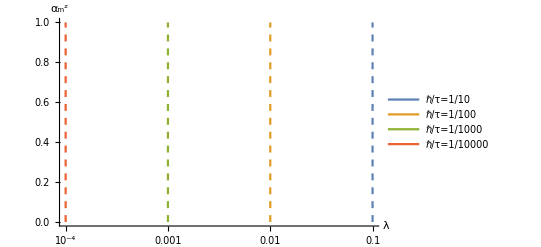

Power::infy: Infinite expression 1/0^2 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

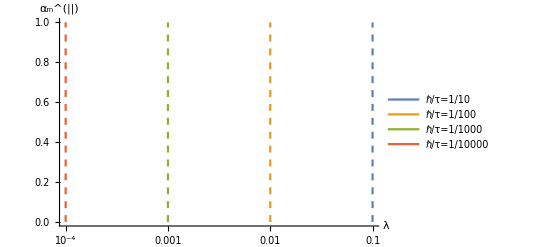

Power::infy: Infinite expression 1/0^2 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

-Graphics-

(0.+0. ⅈ)-(3.70019 λ^2)/((λ^2-100.) (λ^2+0.024674)^2)-0.0608807/((λ^2-100.) (λ^2+0.024674)^2)+λ^6/((λ^2-100.) (λ^2+0.024674)^2)-(49.9383 λ^4)/((λ^2-100.) (λ^2+0.024674)^2)

```mathematica
nsub = {Δ->0,nx->0.5,nz->Sqrt[1-nx nx],ϵ->4};

expr1=tmp[[1,1]];
expr2=tmp[[3,3]];

coeff[αp_,expr_]:=expr//.nsub/.{α->αp}
SetAttributes[coeff,Listable];

iτs = Table[10^-n,{n,{1,2,3,4}}];
iτslabels = {HoldForm[ℏ/τ = 1/10],HoldForm[ℏ/τ = 1/100],HoldForm[ℏ/τ = 1/1000],HoldForm[ℏ/τ = 1/10000]};
αs = 1/(π ϵ /.nsub)iτs;
lines =  Table[{{iτ,0.0},{iτ,1}},{iτ,iτs}];
LogLinearPlot[Evaluate@coeff[αs,expr1],{λ,10^-5,1},PlotLegends->iτslabels,AxesLabel->{"λ","α_m^(||)"}];
ListLogLinearPlot[lines,PlotStyle->{{Dashed}},Joined->True];
Show[%%,%]

LogLinearPlot[Evaluate@coeff[αs,expr2],{λ,10^-5,1},PlotLegends->iτslabels,AxesLabel->{"λ","α_m^z"}];
ListLogLinearPlot[lines,PlotStyle->{{Dashed}},Joined->True];
Show[%%,%]
```

```mathematica
smallMMmatrix =SecondOrderαλ[T0]

rot@({{0, 0, nx}, {0, 0, 0}, {nx, 0, 0}})
rot@({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})
rot@({{0, 0, 0}, {0, 0, 0}, {0, 0, 1}})
```

((-16 π^2 α^2 (nz^2 Δ^2-ϵ^2) (Δ^2+ϵ^2)^3-32 (ϵ-nz Δ)^2 (Δ^4-ϵ^4) λ^2)/(16 π^2 α^2 (Δ^2+ϵ^2)^4+64 (ϵ-nz Δ)^2 λ^2 (Δ^2+ϵ^2)^2) | 0 | (16 nx nz π^2 α^2 Δ^2 (Δ^2+ϵ^2)^3+32 nx Δ (nz Δ-ϵ) (Δ^4-ϵ^4) λ^2)/(16 π^2 α^2 (Δ^2+ϵ^2)^4+64 (ϵ-nz Δ)^2 λ^2 (Δ^2+ϵ^2)^2)
0 | (-16 π^2 α^2 (Δ^2-ϵ^2) (Δ^2+ϵ^2)^3-32 (ϵ-nz Δ)^2 (Δ^4-ϵ^4) λ^2)/(16 π^2 α^2 (Δ^2+ϵ^2)^4+64 (ϵ-nz Δ)^2 λ^2 (Δ^2+ϵ^2)^2) | 0
(16 nx nz π^2 α^2 Δ^2 (Δ^2+ϵ^2)^3+32 nx Δ (nz Δ-ϵ) (Δ^4-ϵ^4) λ^2)/(16 π^2 α^2 (Δ^2+ϵ^2)^4+64 (ϵ-nz Δ)^2 λ^2 (Δ^2+ϵ^2)^2) | 0 | (32 π^2 α^2 ((nz^2-1) Δ^2+ϵ^2) (Δ^2+ϵ^2)^3+64 (nz^2-1) Δ^2 (Δ^4-ϵ^4) λ^2)/(32 π^2 α^2 (Δ^2+ϵ^2)^4+128 (ϵ-nz Δ)^2 λ^2 (Δ^2+ϵ^2)^2))

(0 | 0 | nx
0 | 0 | ny
nx | ny | 0)

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 1)

```mathematica
(nx nz π^2 α^2 Δ^2 ϵ^6)/((Δ^2+ϵ^2)^2 (π^2 α^2 (Δ^2+ϵ^2)^2+4 (ϵ-nz Δ)^2 λ^2))//Coefficient[#,ϵ,2]&
```

(π^2 α^2 Δ^2 nx nz)/((Δ^2+ϵ^2)^2 (π^2 α^2 (Δ^2+ϵ^2)^2+4 λ^2 (ϵ-Δ nz)^2))

```mathematica
({{(Δ^2 (-ny^2)-Δ^2 nz^2+ϵ^2)/(Δ^2+ϵ^2), (Δ^2 nx ny)/(Δ^2+ϵ^2), (Δ^2 nx nz)/(Δ^2+ϵ^2)}, {(Δ^2 nx ny)/(Δ^2+ϵ^2), (Δ^2 (ny^2-1)+ϵ^2)/(Δ^2+ϵ^2), (Δ^2 ny nz)/(Δ^2+ϵ^2)}, {(Δ^2 nx nz)/(Δ^2+ϵ^2), (Δ^2 ny nz)/(Δ^2+ϵ^2), (Δ^2 (nz^2-1)+ϵ^2)/(Δ^2+ϵ^2)}})
```

```mathematica
T2[[MMindex,MMindex]]//SecondOrderαλ
%//rot 
%- (π^2 α^2 Δ^2)/(π^2 α^2 Δ^2+4 nz^2 λ^2)({{nx nx, nx ny, nx nz}, {nx ny, ny ny, ny nz}, {nz nx, nz ny, nz nz}})-(2  λ^2)/(π^2 α^2 Δ^2+4 nz^2 λ^2)({{0, 0, nx nz}, {0, 0, ny nz}, {nx nz, ny nz, nz nz}})+(π^2 α^2 Δ^2+2 λ^2)/(π^2 α^2 Δ^2+4 nz^2 λ^2)({{0, 0, 0}, {0, 0, 0}, {0, 0, 1}})+(π^2 α^2 Δ^2+2 λ^2 nz^2)/(π^2 α^2 Δ^2+4 nz^2 λ^2)({{1, 0, 0}, {0, 1, 0}, {0, 0, 0}})//Simplify [#,Assumptions->nx nx +ny ny+nz nz==1]&
%%- (π^2 α^2 Δ^2+2  λ^2)/(π^2 α^2 Δ^2+4 nz^2 λ^2)({{nx nx, nx ny, nx nz}, {nx ny, ny ny, ny nz}, {nz nx, nz ny, nz nz}})-(-2  λ^2)/(π^2 α^2 Δ^2+4 nz^2 λ^2)({{nx nx, nx ny, 0}, {nx ny, ny ny, 0}, {0, 0, 0}})+(π^2 α^2 Δ^2+2 λ^2)/(π^2 α^2 Δ^2+4 nz^2 λ^2)({{0, 0, 0}, {0, 0, 0}, {0, 0, 1}})+(π^2 α^2 Δ^2+2 λ^2 nz^2)/(π^2 α^2 Δ^2+4 nz^2 λ^2)({{1, 0, 0}, {0, 1, 0}, {0, 0, 0}})//Simplify [#,Assumptions->nx nx +ny ny+nz nz==1]&;
```

((-4 nz^2 π^2 α^2 Δ^4-8 nz^2 λ^2 Δ^2)/(4 π^2 α^2 Δ^4+16 nz^2 λ^2 Δ^2) | 0 | (4 nx nz π^2 α^2 Δ^4+8 nx nz λ^2 Δ^2)/(4 π^2 α^2 Δ^4+16 nz^2 λ^2 Δ^2)
0 | (-2 π^2 α^2 Δ^4-4 nz^2 λ^2 Δ^2)/(2 π^2 α^2 Δ^4+8 nz^2 λ^2 Δ^2) | 0
(4 nx nz π^2 α^2 Δ^4+8 nx nz λ^2 Δ^2)/(4 π^2 α^2 Δ^4+16 nz^2 λ^2 Δ^2) | 0 | (4 (nz^2-1) π^2 α^2 Δ^4+8 (nz^2-1) λ^2 Δ^2)/(4 π^2 α^2 Δ^4+16 nz^2 λ^2 Δ^2))

(-((π^2 α^2 Δ^2+2 λ^2) nz^2+ny^2 π^2 α^2 Δ^2)/(π^2 α^2 Δ^2+4 nz^2 λ^2) | (nx ny π^2 α^2 Δ^2)/(π^2 α^2 Δ^2+4 nz^2 λ^2) | (nx nz (π^2 α^2 Δ^2+2 λ^2))/(π^2 α^2 Δ^2+4 nz^2 λ^2)
(nx ny π^2 α^2 Δ^2)/(π^2 α^2 Δ^2+4 nz^2 λ^2) | ((ny^2-1) π^2 α^2 Δ^2-2 nz^2 λ^2)/(π^2 α^2 Δ^2+4 nz^2 λ^2) | (ny nz (π^2 α^2 Δ^2+2 λ^2))/(π^2 α^2 Δ^2+4 nz^2 λ^2)
(nx nz (π^2 α^2 Δ^2+2 λ^2))/(π^2 α^2 Δ^2+4 nz^2 λ^2) | (ny nz (π^2 α^2 Δ^2+2 λ^2))/(π^2 α^2 Δ^2+4 nz^2 λ^2) | ((nz^2-1) (π^2 α^2 Δ^2+2 λ^2))/(π^2 α^2 Δ^2+4 nz^2 λ^2))

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

```mathematica
(π α)/2 T[[MMindex,MMindex]][[1,3]]//Simplify//Together;
%//Numerator[#]&//Collect[#,ϵ,1&]&
%%//Denominator[#]&//Collect[#,ϵ,1&]&
%%/%//Exponent[#,ϵ]&
%%%%//Exponent[#,ϵ]&
```

ϵ^6+ϵ^5+ϵ^4+ϵ^3+ϵ^2+ϵ+1

ϵ^8+ϵ^6+ϵ^5+ϵ^4+ϵ^3+ϵ^2+ϵ+1

-2

-2

```mathematica
(π α)/2 T[[MMindex,MMindex]]//BigϵExpansion//SecondOrderαλ
```

((-16 nz^2 π^2 α^2 Δ^4-32 nz^2 λ^2 Δ^2)/(16 π^2 α^2 Δ^4+64 nz^2 λ^2 Δ^2) | 0 | (32 nx Δ (ϵ-nz Δ)^2 (Δ^2+ϵ^2) λ^2-16 nx nz π^2 α^2 Δ^2 (nz Δ-ϵ) (Δ^2+ϵ^2)^2)/(64 ϵ^2 (Δ^2+ϵ^2)^2 λ^2 (ϵ-nz Δ)^4+16 π^2 α^2 ϵ^2 (Δ^2+ϵ^2)^4 (ϵ-nz Δ)^2)
0 | (-16 π^2 α^2 Δ^4-32 nz^2 λ^2 Δ^2)/(16 π^2 α^2 Δ^4+64 nz^2 λ^2 Δ^2) | 0
(32 nx Δ (ϵ-nz Δ)^2 (Δ^2+ϵ^2) λ^2-16 nx nz π^2 α^2 Δ^2 (nz Δ-ϵ) (Δ^2+ϵ^2)^2)/(64 ϵ^2 (Δ^2+ϵ^2)^2 λ^2 (ϵ-nz Δ)^4+16 π^2 α^2 ϵ^2 (Δ^2+ϵ^2)^4 (ϵ-nz Δ)^2) | 0 | (32 (nz^2-1) π^2 α^2 Δ^4+64 (nz^2-1) λ^2 Δ^2)/(32 π^2 α^2 Δ^4+128 nz^2 λ^2 Δ^2))

```mathematica
T3[[MMindex,MMindex]]//SecondOrderαλ
%//rot
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
T2[[MMindex,MMindex]][[1,1]]/.{α->ωp α,λ-> ωp λ}
```

(π^4 α^4 Δ^4 ωp^4+λ^2 nz^4 ωp^2 (π^4 α^4 Δ^2 ωp^4+4 π^2 α^2 Δ^2 ωp^2+16 λ^2 ωp^2)-Δ^2 nz^2 (π^4 α^4 ωp^4 (Δ^2+λ^2 ωp^2)+2 π^2 α^2 ωp^2 (2 Δ^2-λ^2 ωp^2)+8 λ^2 ωp^2))/(4 (Δ^2-λ^2 nz^2 ωp^2) (π^2 α^2 Δ^2 ωp^2+4 λ^2 nz^2 ωp^2))

```mathematica
T2 = (π α)/2 T //Series[#,{ϵ,0,0}]&//Normal//Simplify[#,Assumptions->nx nx+nz nz ==1]&;
T2//Series[#,{α,0,2},{λ,0,2}]&//Normal//Simplify;
%[[MMindex,MMindex]]//rot//Simplify[#,Assumptions->nx nx+ny ny+nz nz==1]&

T2//Series[#,{λ,0,2},{α,0,2}]&//Normal//Simplify;
%[[MMindex,MMindex]]//rot//Simplify[#,Assumptions->nx nx+ny ny+nz nz==1]&
```

(1/8 (((-2 ny^2-2 nz^2+1) π^2 α^2 Δ^2)/(nz^2 λ^2)-4+(4 nz^2 λ^2)/Δ^2) | -(nx ny π^2 α^2 Δ^2)/(4 nz^2 λ^2) | (nx (-(4 λ^2 nz^4)/Δ^2+4 nz^2+(π^2 α^2 (2 nz^2 (Δ^2+λ^2)-Δ^2))/λ^2))/(8 nz^3)
-(nx ny π^2 α^2 Δ^2)/(4 nz^2 λ^2) | 1/8 (((2 ny^2-1) π^2 α^2 Δ^2)/(nz^2 λ^2)-4+(4 nz^2 λ^2)/Δ^2) | -(ny (-(4 λ^2 nz^4)/Δ^2+4 nz^2+(π^2 α^2 (2 nz^2 (Δ^2+λ^2)-Δ^2))/λ^2))/(8 nz^3)
(nx (-(4 λ^2 nz^4)/Δ^2+4 nz^2+(π^2 α^2 (2 nz^2 (Δ^2+λ^2)-Δ^2))/λ^2))/(8 nz^3) | -(ny (-(4 λ^2 nz^4)/Δ^2+4 nz^2+(π^2 α^2 (2 nz^2 (Δ^2+λ^2)-Δ^2))/λ^2))/(8 nz^3) | (((2 nz^2-1) π^2 α^2 ((nz^2-1) Δ^2+2 nz^2 λ^2))/λ^2-(4 nz^2 (nz^2-1) (nz^2 λ^2-Δ^2))/Δ^2)/(8 nz^4))

((4 (π^2 α^2+4) λ^2 nz^4-(π^2 α^2+4) (π^2 α^2 Δ^2+2 λ^2) nz^2+π^4 α^4 Δ^2-ny^2 (π^2 α^2+4) (π^2 α^2 Δ^2-4 nz^2 λ^2))/(4 π^2 α^2 Δ^2) | -(nx ny (π^2 α^2+4) (π^2 α^2 Δ^2-4 nz^2 λ^2))/(4 π^2 α^2 Δ^2) | (nx nz (π^2 α^2+4) (π^2 α^2 Δ^2+2 (1-2 nz^2) λ^2))/(4 π^2 α^2 Δ^2)
-(nx ny (π^2 α^2+4) (π^2 α^2 Δ^2-4 nz^2 λ^2))/(4 π^2 α^2 Δ^2) | 1/4 π^2 α^2 ny^2+ny^2+((1-2 ny^2) nz^2 λ^2)/(2 Δ^2)+(2 (1-2 ny^2) nz^2 λ^2)/(π^2 α^2 Δ^2)-1 | -(ny nz (π^2 α^2+4) (π^2 α^2 Δ^2+2 (1-2 nz^2) λ^2))/(4 π^2 α^2 Δ^2)
(nx nz (π^2 α^2+4) (π^2 α^2 Δ^2+2 (1-2 nz^2) λ^2))/(4 π^2 α^2 Δ^2) | -(ny nz (π^2 α^2+4) (π^2 α^2 Δ^2+2 (1-2 nz^2) λ^2))/(4 π^2 α^2 Δ^2) | 1/4 π^2 α^2 nz^2+nz^2-((2 nz^4-3 nz^2+1) (π^2 α^2+4) λ^2)/(2 π^2 α^2 Δ^2)-1)

```mathematica
T2[[MMindex,MMindex]]//Numerator[#]&//Series[#,{α,0,2},{λ,0,2}]&//Normal//Collect[#,{α,λ}, Simplify]&
T2[[MMindex,MMindex]]//Denominator[#]&//Series[#,{α,0,2},{λ,0,2}]&//Normal//Collect[#,{α,λ}, Simplify]&
%%/%
```

(α^2 (2 nz^2 (2 nz^2+1) π^2 Δ^2 λ^2-4 nz^2 π^2 Δ^4)-8 nz^2 Δ^2 λ^2 | 0 | (4 nx nz π^2 Δ^4+2 nx nz (1-2 nz^2) π^2 λ^2 Δ^2) α^2+8 nx nz Δ^2 λ^2
0 | α^2 (3 nz^2 π^2 Δ^2 λ^2-2 π^2 Δ^4)-4 nz^2 Δ^2 λ^2 | 0
(4 nx nz π^2 Δ^4+2 nx nz (1-2 nz^2) π^2 λ^2 Δ^2) α^2+8 nx nz Δ^2 λ^2 | 0 | (4 (nz^2-1) π^2 Δ^4-2 (2 nz^4-5 nz^2+1) π^2 Δ^2 λ^2) α^2+8 (nz^2-1) Δ^2 λ^2)

((4 π^2 Δ^4-4 nz^2 π^2 Δ^2 λ^2) α^2+16 nz^2 Δ^2 λ^2 | 1 | (4 π^2 Δ^4-4 nz^2 π^2 Δ^2 λ^2) α^2+16 nz^2 Δ^2 λ^2
1 | (2 π^2 Δ^4-2 nz^2 π^2 Δ^2 λ^2) α^2+8 nz^2 Δ^2 λ^2 | 1
(4 π^2 Δ^4-4 nz^2 π^2 Δ^2 λ^2) α^2+16 nz^2 Δ^2 λ^2 | 1 | (4 π^2 Δ^4-4 nz^2 π^2 Δ^2 λ^2) α^2+16 nz^2 Δ^2 λ^2)

((α^2 (2 nz^2 (2 nz^2+1) π^2 Δ^2 λ^2-4 nz^2 π^2 Δ^4)-8 nz^2 Δ^2 λ^2)/((4 π^2 Δ^4-4 nz^2 π^2 Δ^2 λ^2) α^2+16 nz^2 Δ^2 λ^2) | 0 | ((4 nx nz π^2 Δ^4+2 nx nz (1-2 nz^2) π^2 λ^2 Δ^2) α^2+8 nx nz Δ^2 λ^2)/((4 π^2 Δ^4-4 nz^2 π^2 Δ^2 λ^2) α^2+16 nz^2 Δ^2 λ^2)
0 | (α^2 (3 nz^2 π^2 Δ^2 λ^2-2 π^2 Δ^4)-4 nz^2 Δ^2 λ^2)/((2 π^2 Δ^4-2 nz^2 π^2 Δ^2 λ^2) α^2+8 nz^2 Δ^2 λ^2) | 0
((4 nx nz π^2 Δ^4+2 nx nz (1-2 nz^2) π^2 λ^2 Δ^2) α^2+8 nx nz Δ^2 λ^2)/((4 π^2 Δ^4-4 nz^2 π^2 Δ^2 λ^2) α^2+16 nz^2 Δ^2 λ^2) | 0 | ((4 (nz^2-1) π^2 Δ^4-2 (2 nz^4-5 nz^2+1) π^2 Δ^2 λ^2) α^2+8 (nz^2-1) Δ^2 λ^2)/((4 π^2 Δ^4-4 nz^2 π^2 Δ^2 λ^2) α^2+16 nz^2 Δ^2 λ^2))

```mathematica
f[0,0]=0
g[0,0]=0
(Series[f[α,λ],{α,0,3},{λ,0,3}]//Normal)/(Series[g[α,λ],{α,0,3},{λ,0,3}]//Normal)
%//Series[#,{α,0,0},{λ,0,0}]&//Normal
(Series[f[α,λ],{α,0,4},{λ,0,4}]//Normal)/(Series[g[α,λ],{α,0,4},{λ,0,4}]//Normal)//Series[#,{λ,0,0},{α,0,0}]&//Normal
```

0

0

(α^3 (1/36 λ^3 f^(3,3)(0,0)+1/12 λ^2 f^(3,2)(0,0)+1/6 λ f^(3,1)(0,0)+1/6 f^(3,0)(0,0))+α^2 (1/12 λ^3 f^(2,3)(0,0)+1/4 λ^2 f^(2,2)(0,0)+1/2 λ f^(2,1)(0,0)+1/2 f^(2,0)(0,0))+α (1/6 λ^3 f^(1,3)(0,0)+1/2 λ^2 f^(1,2)(0,0)+λ f^(1,1)(0,0)+f^(1,0)(0,0))+1/6 λ^3 f^(0,3)(0,0)+1/2 λ^2 f^(0,2)(0,0)+λ f^(0,1)(0,0))/(α^3 (1/36 λ^3 g^(3,3)(0,0)+1/12 λ^2 g^(3,2)(0,0)+1/6 λ g^(3,1)(0,0)+1/6 g^(3,0)(0,0))+α^2 (1/12 λ^3 g^(2,3)(0,0)+1/4 λ^2 g^(2,2)(0,0)+1/2 λ g^(2,1)(0,0)+1/2 g^(2,0)(0,0))+α (1/6 λ^3 g^(1,3)(0,0)+1/2 λ^2 g^(1,2)(0,0)+λ g^(1,1)(0,0)+g^(1,0)(0,0))+1/6 λ^3 g^(0,3)(0,0)+1/2 λ^2 g^(0,2)(0,0)+λ g^(0,1)(0,0))

(f^(0,1)(0,0))/(g^(0,1)(0,0))

(f^(1,0)(0,0))/(g^(1,0)(0,0))

```mathematica
MMindex = {2,3,4};
mmMatrix1 = %65[[MMindex,MMindex]]//rot//Simplify[#,Assumptions->nx nx+ny ny+nz nz==1]&
mmMatrix2 = %66[[MMindex,MMindex]]//rot//Simplify[#,Assumptions->nx nx+ny ny+nz nz==1]&
```

(-1/2 | 0 | nx/(2 nz)
0 | -1/2 | -ny/(2 nz)
nx/(2 nz) | -ny/(2 nz) | 1/2 (1-1/nz^2))

(-ny^2-nz^2 | -nx ny | nx nz
-nx ny | ny^2-1 | -ny nz
nx nz | -ny nz | nz^2-1)

```mathematica
T1=(π α)/2 T //Limit[#,λ->0]&//Limit[#,α->0]&//Simplify[#,Assumptions->nx nx+nz nz ==1]&
```

(ϵ^2/(Δ^2+ϵ^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (nx Δ ϵ)/(Δ^2+ϵ^2) | 0 | (nz Δ ϵ)/(Δ^2+ϵ^2)
0 | (ϵ^2-nz^2 Δ^2)/(Δ^2+ϵ^2) | 0 | (nx nz Δ^2)/(Δ^2+ϵ^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (nx Δ ϵ)/(Δ^2+ϵ^2) | 0 | 0 | 0
0 | 0 | (ϵ^2-Δ^2)/(Δ^2+ϵ^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (nx nz Δ^2)/(Δ^2+ϵ^2) | 0 | ((nz^2-1) Δ^2+ϵ^2)/(Δ^2+ϵ^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (nz Δ ϵ)/(Δ^2+ϵ^2) | 0 | 0 | 0
0 | 0 | 0 | 0 | (ϵ^2-Δ^2)/(2 (Δ^2+ϵ^2)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ((2 nz^2-1) Δ^2+ϵ^2)/(2 (Δ^2+ϵ^2)) | 0 | -(nx nz Δ^2)/(Δ^2+ϵ^2) | 0 | 0 | -(nz Δ ϵ)/(Δ^2+ϵ^2) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | (nz Δ ϵ)/(Δ^2+ϵ^2) | 0 | -(nx Δ ϵ)/(Δ^2+ϵ^2) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -(nx nz Δ^2)/(Δ^2+ϵ^2) | 0 | ((1-2 nz^2) Δ^2+ϵ^2)/(2 (Δ^2+ϵ^2)) | 0 | 0 | (nx Δ ϵ)/(Δ^2+ϵ^2) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (ϵ^2-Δ^2)/(2 (Δ^2+ϵ^2)) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | (nz Δ ϵ)/(Δ^2+ϵ^2) | 0 | 0 | ((2 nz^2-1) Δ^2+ϵ^2)/(2 (Δ^2+ϵ^2)) | 0 | -(nx nz Δ^2)/(Δ^2+ϵ^2) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -(nz Δ ϵ)/(Δ^2+ϵ^2) | 0 | (nx Δ ϵ)/(Δ^2+ϵ^2) | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -(nx Δ ϵ)/(Δ^2+ϵ^2) | 0 | 0 | -(nx nz Δ^2)/(Δ^2+ϵ^2) | 0 | ((1-2 nz^2) Δ^2+ϵ^2)/(2 (Δ^2+ϵ^2)) | 0 | 0 | 0 | 0
0 | (nx Δ ϵ)/(Δ^2+ϵ^2) | 0 | (nz Δ ϵ)/(Δ^2+ϵ^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Δ^2/(Δ^2+ϵ^2) | 0 | 0 | 0
(nx Δ ϵ)/(Δ^2+ϵ^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -((nz^2-1) Δ^2)/(Δ^2+ϵ^2) | 0 | (nx nz Δ^2)/(Δ^2+ϵ^2)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(nz Δ ϵ)/(Δ^2+ϵ^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (nx nz Δ^2)/(Δ^2+ϵ^2) | 0 | (nz^2 Δ^2)/(Δ^2+ϵ^2))

```mathematica
Det[IdentityMatrix[16]-%209]//Simplify[#,Assumptions->nx nx+nz nz ==1]&
```

0

```mathematica
MMindex = {2,3,4};
mmMatrix = T1[[MMindex,MMindex]];
%//MatrixForm
%-Δ^2/(Δ^2+ϵ^2)({{nx nx, nx ny, nx nz}, {nx ny, ny ny, ny nz}, {nz nx, nz ny, nz nz}})/.ny->0;
%//Simplify//MatrixForm
```

((ϵ^2-Δ^2 nz^2)/(Δ^2+ϵ^2) | 0 | (Δ^2 nx nz)/(Δ^2+ϵ^2)
0 | (ϵ^2-Δ^2)/(Δ^2+ϵ^2) | 0
(Δ^2 nx nz)/(Δ^2+ϵ^2) | 0 | (Δ^2 (nz^2-1)+ϵ^2)/(Δ^2+ϵ^2))

((Δ^2 (-nx^2)-Δ^2 nz^2+ϵ^2)/(Δ^2+ϵ^2) | 0 | 0
0 | (ϵ^2-Δ^2)/(Δ^2+ϵ^2) | 0
0 | 0 | (ϵ^2-Δ^2)/(Δ^2+ϵ^2))

```mathematica
(*R = RotationMatrix[{{Cos[α],Sin[α],0},{1,0,0}}]^†//ComplexExpand//Simplify;
R//MatrixForm
Rp = R/.{Cos[α]->nx/Sqrt[1-nz nz], Sin[α]->ny/Sqrt[1-nz nz],Cos[β]->nz, Sin[β]->Sqrt[1-nz nz]}
{Sqrt[1-nz nz],0,nz}
Rp.%

R.{Sin[β],0,Cos[β]}/.{Cos[α]->nx/Sqrt[1-nz nz], Sin[α]->ny/Sqrt[1-nz nz],Cos[β]->nz, Sin[β]->Sqrt[1-nz nz]}

R^ᵀ.mmMatrix.R/.{Cos[α]->nx/Sqrt[1-nz nz], Sin[α]->ny/Sqrt[1-nz nz]}//Simplify*)

R = {{nx/(√(1-nz^2)),-ny/(√(1-nz^2)),0},{ny/(√(1-nz^2)),nx/(√(1-nz^2)),0},{0,0,1}};
R.{Sqrt[1-nz nz],0,nz}//Simplify[#,Assumptions->nx nx +ny ny+nz nz ==1]&
rot [mat_]:= Block[{R},
   R={{nx/(√(1-nz^2)),-ny/(√(1-nz^2)),0},{ny/(√(1-nz^2)),nx/(√(1-nz^2)),0},{0,0,1}};   
   R.(mat/.{nx->Sqrt[1-nz nz]}).Transpose[R]//Simplify[#,nx nx+ny ny +nz nz ==1]&]
rot[mmMatrix]//Simplify[#,nx nx+ny ny+nz nz ==1]&

%//MatrixForm
```

{nx,ny,nz}

((-ny^2 Δ^2-nz^2 Δ^2+ϵ^2)/(Δ^2+ϵ^2) | (nx ny Δ^2)/(Δ^2+ϵ^2) | (nx nz Δ^2)/(Δ^2+ϵ^2)
(nx ny Δ^2)/(Δ^2+ϵ^2) | ((ny^2-1) Δ^2+ϵ^2)/(Δ^2+ϵ^2) | (ny nz Δ^2)/(Δ^2+ϵ^2)
(nx nz Δ^2)/(Δ^2+ϵ^2) | (ny nz Δ^2)/(Δ^2+ϵ^2) | ((nz^2-1) Δ^2+ϵ^2)/(Δ^2+ϵ^2))

((Δ^2 (-ny^2)-Δ^2 nz^2+ϵ^2)/(Δ^2+ϵ^2) | (Δ^2 nx ny)/(Δ^2+ϵ^2) | (Δ^2 nx nz)/(Δ^2+ϵ^2)
(Δ^2 nx ny)/(Δ^2+ϵ^2) | (Δ^2 (ny^2-1)+ϵ^2)/(Δ^2+ϵ^2) | (Δ^2 ny nz)/(Δ^2+ϵ^2)
(Δ^2 nx nz)/(Δ^2+ϵ^2) | (Δ^2 ny nz)/(Δ^2+ϵ^2) | (Δ^2 (nz^2-1)+ϵ^2)/(Δ^2+ϵ^2))

### operators: -Graphics-

```mathematica
MathTex
```